# Histograms - “Country vs $” - Sample of countries - 201(6)

## Importing data + Agencies + Categories + Checks

Sample of countries under investigation:

```mathematica
listCountrySample=Flatten@StringCases[CommonName[EntityList[EntityClass["Country",All]]],StartOfString ~~WordCharacter..~~EndOfString];
```

```mathematica
listCountrySample
```

{Jordan,Algeria,Angola,Argentina,Armenia,Austria,China,Croatia,Estonia,Ethiopia,Georgia,Kenya,Latvia,Libya,Namibia,Russia,Somalia,Uganda,Antarctica,Bulgaria,Liberia,Luxembourg,Slovakia,Taiwan,Chile,Ireland,Portugal,Australia,Israel,Niger,Venezuela,Cuba,Ecuador,Guatemala,Honduras,Mexico,Peru,Afghanistan,Albania,Andorra,Anguilla,Aruba,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Botswana,Brazil,Brunei,Burundi,Cambodia,Cameroon,Canada,Chad,Colombia,Comoros,Cyprus,Denmark,Djibouti,Dominica,Egypt,Eritrea,Fiji,Finland,France,Gabon,Gambia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guernsey,Guinea,Guyana,Haiti,Hungary,Iceland,India,Indonesia,Iran,Iraq,Italy,Jamaica,Japan,Jersey,Kazakhstan,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Lebanon,Lesotho,Liechtenstein,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Martinique,Mauritania,Mauritius,Mayotte,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Nauru,Nepal,Netherlands,Nicaragua,Nigeria,Niue,Norway,Oman,Pakistan,Palau,Panama,Paraguay,Philippines,Poland,Qatar,Réunion,Romania,Rwanda,Samoa,Senegal,Serbia,Seychelles,Singapore,Slovenia,Spain,Sudan,Suriname,Swaziland,Sweden,Switzerland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Tunisia,Turkey,Turkmenistan,Tuvalu,Ukraine,Uruguay,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe,Macau,Svalbard,Curacao}

Number of countries in our sample:

```mathematica
toTnumberCountry=listCountrySample//Length
```

179

Importing data via the API (2016):

```mathematica
datasetsCS=Cases[Map[#-> URLExecute["http://fagov-api-prod.azurewebsites.net/api/public/activities",{"format"->"json","fundingType"->"obligated","filterType"->"location","filterValue"->#,"year"->"2016"},"RawJSON"]&,listCountrySample], _[_, _List]];
```

Agencies  sample (Deleting all the agencies which are repeated in all datasets - each country has a dataset):

```mathematica
agencies[xDataF_]:=DeleteDuplicates[Table[Values[Values[Normal[datasetsCS[[xDataF]]]]][[i,1]],{i,1,Length[Values[Normal[datasetsCS[[xDataF]]]]]}]]
```

```mathematica
aGENCY=DeleteDuplicates[Flatten@Join[Table[agencies[i],{i,1,Length[Values[Normal[datasetsCS]]]}]]]
```

{Overseas Private Investment Corporation,Department of Defense,Peace Corps,U.S. Agency for International Development,U.S. Department of State,U.S. Department of the Treasury,Inter-American Foundation,Department of Interior,U.S. African Development Foundation,Department of Justice,Department of Labor,U.S. Department of Agriculture}

Categories sample (Deleting all the categories which are repeated in all datasets):

```mathematica
categories[xDataF_]:=DeleteDuplicates[Table[Values[Values[Normal[datasetsCS[[xDataF]]]]][[i,3]],{i,1,Length[Values[Normal[datasetsCS[[xDataF]]]]]}]]
```

```mathematica
categorieS=DeleteDuplicates[Flatten@Join[Table[categories[i],{i,1,Length[Values[Normal[datasetsCS]]]}]]];
```

Checking whether or not the first row of each dataset is the same:

```mathematica
Do[If[Keys[Values[Normal[datasetsCS[[1]]]]][[1]]==Keys[Values[Normal[datasetsCS[[j]]]]][[1]],"Null",Print[j]],{j,2,Length[Values[Normal[datasetsCS]]]}]
```

Yes, it is the same!

## Analysis

Putting all our data together in a list of associations:

```mathematica
dataAlltogether=Flatten@Values[datasetsCS]
```

{<|AgencyName→Overseas Private Investment Corporation,Amount→20000000.00,Category→Economic Development,Year→2016,BenefitingLocation→Jordan,Sector→Financial Sector|>,<|AgencyName→Department of Defense,Amount→15235000.00,Category→Peace and Security,Year→2016,BenefitingLocation→Jordan,Sector→Combating Weapons of Mass Destruction (WMD)|>,34596,<|AgencyName→U.S. Agency for International Development,Amount→2580.32,Category→Program Management,Year→2016,BenefitingLocation→Zimbabwe,Sector→Direct Administrative Costs|>,<|AgencyName→U.S. Agency for International Development,Amount→1003.46,Category→Program Management,Year→2016,BenefitingLocation→Zimbabwe,Sector→Direct Administrative Costs|>}
 |  |  |  |

Selecting associations with a given category, agency name and country:

```mathematica
Clear[AnalysisNew]
```

```mathematica
AnalysisNew[category_,agencyName_,country_]:=With[{r=Select[Select[Select[dataAlltogether,#[[3]]==category&],#[[1]]==agencyName&],#[[5]]==country&]},If[Length[r]==0,{Association[Rule["AgencyName",agencyName],Rule["Amount","0.00"],Rule["Category",category],Rule["Year",""],Rule["BenefitingLocation",country],Rule["Sector",""]]},r]];
```

Converting amount of money in US dollar currency by using Interpreter:

```mathematica
AnalysisAmountNew[category_,agencyName_,country_]:=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],AnalysisNew[category,agencyName,country],{1;;,2}];
```

Computing total amount of money for a given category and agency name:

```mathematica
AnalysisTotUSDollarNew[category_,agencyName_,country_]:=Total[AnalysisAmountNew[category,agencyName,country][[All,"Amount"]]];
```

Creating a list of {country,TotAmountDollar} given category, year and agency name:

```mathematica
AnalysisAmount[category_,agencyName_]:=Map[{#,AnalysisTotUSDollarNew[category,agencyName,#]}&,Keys[datasetsCS]];
```

Creating an association between agency and the list {country, TotAmountDollar} given category, year and agency name

```mathematica
dtot[category_,agencyName_]:=Map[agencyName->{#,AnalysisTotUSDollarNew[category,agencyName,#]}&,Keys[datasetsCS]];
```

```mathematica
Clear[dtotOhne0]
```

Removing zero and negative amount of money:

```mathematica
dtotOhne0[category_,agencyName_]:=Cases[dtot[category, agencyName],HoldPattern[_String-> {_String,Quantity[x_/;x>0,"USDollars"]}]]
```

Creating a list of “dtot” after having computed “dtot” for each category and taking into consideration all agencies:

```mathematica
Clear[amountTotlistNewOhne0]
amountTotlistNewOhne0[category_]:=Map[dtotOhne0[category,#]&,aGENCY];
```

## General case

```mathematica
categorieS
```

{Economic Development,Peace and Security,Program Management,Multi-sector,Education and Social Services,Democracy, Human Rights, and Governance,Humanitarian Assistance,Health,Environment}

```mathematica
aGENCY
```

{Overseas Private Investment Corporation,Department of Defense,Peace Corps,U.S. Agency for International Development,U.S. Department of State,U.S. Department of the Treasury,Inter-American Foundation,Department of Interior,U.S. African Development Foundation,Department of Justice,Department of Labor,U.S. Department of Agriculture}

Creating a list of associations which connect the above total amount with the corresponding category (for all the categories):

```mathematica
Clear[listamountTOTNewOhne0]
listamountTOTNewOhne0=Map[#->Flatten@amountTotlistNewOhne0[#]&,categorieS];
```

Number of agencies and categories under consideration:

```mathematica
Style[{Length[aGENCY],Length[categorieS]},Bold,Underlined]
```

{12,9}

Functions for plots  (1 category --> all agencies)

```mathematica
totMoneyCategAgenc[CategAgenc_]:=Table[CategAgenc[[i]][[2]],{i,1,Length[CategAgenc]}]
```

```mathematica
countriesCategAgenc[CategAgenc_]:=Table[CategAgenc[[i]][[1]],{i,1,Length[CategAgenc]}]
```

```mathematica
histPlot[totcountriesCategAgen_,countriesCategAgen_,nameComplAgency_]:=BarChart[totcountriesCategAgen,ScalingFunctions->"Log",Frame->True,PlotLabel->nameComplAgency,ImageSize->Large,FrameLabel->{"",$ },ChartLabels->Placed[countriesCategAgen,Axis,Rotate[#,Pi/2]&]]
```

```mathematica
histPlotFin[CategAgenc_,nameComplAgency_]:=BarChart[totMoneyCategAgenc[CategAgenc],ScalingFunctions->"Log",Frame->True,BarSpacing->1,PlotLabel->nameComplAgency,ImageSize->Large,FrameLabel->{"",$ },ChartLabels->Placed[countriesCategAgenc[CategAgenc],Axis,Rotate[#,Pi/2]&]]
```

### listamountTOTNew[[1]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[1]]],FontColor->Red,Large]
```

Economic Development

```mathematica
listMoney1=Map[Cases[Values[listamountTOTNewOhne0[[1]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney1//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney1[[#]]]&,Range[Length[aGENCY]]]
```

{1→23,2→0,3→34,4→61,5→0,6→26,7→10,8→0,9→23,10→0,11→5,12→6}

#### --- --- --- 1

```mathematica
textlistMoney11=Style[listMoney1[[1]][[1]]//Keys,FontColor->Red]
```

Overseas Private Investment Corporation

```mathematica
New11=listMoney1[[1]]//Values;
```

```mathematica
{listMoney1[[1]][[1]],listMoney1[[1]][[2]]}
```

{Overseas Private Investment Corporation→{Jordan,2.e7 $},Overseas Private Investment Corporation→{Armenia,9.75e6 $}}

```mathematica
Length[New11]
```

23

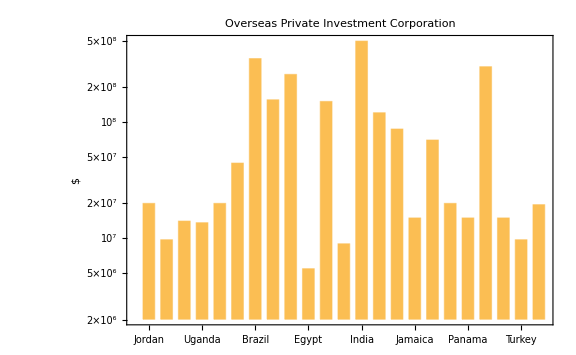

```mathematica
histPlotFin[New11,ToString[textlistMoney11]]
```

#### --- --- --- 2

```mathematica
textlistMoney12=Style[listMoney1[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New12=listMoney1[[2]]//Values
```

{}

```mathematica
Length[New12]
```

0

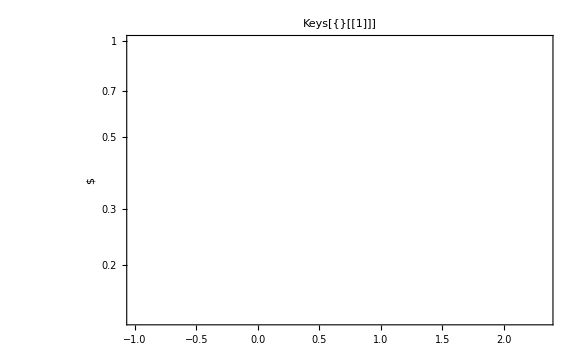

```mathematica
histPlotFin[New12,ToString[textlistMoney12]]
```

#### --- --- --- 3

```mathematica
textlistMoney13=Style[listMoney1[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New13=listMoney1[[3]]//Values
```

{{Armenia,488 291.00 $},{Ethiopia,77 201.00 $},{Georgia,738 570.00 $},{Namibia,458 307.00 $},{Uganda,1.000437e6 $},{Liberia,2 188.00 $},{Guatemala,148 714.00 $},{Mexico,323 831.00 $},{Peru,1.081918e6 $},{Albania,542 421.00 $},{Benin,931 307.00 $},{Cambodia,46 189.00 $},{Cameroon,1.355891e6 $},{Colombia,135 742.00 $},{Ghana,1.397098e6 $},{Guinea,6 158.00 $},{Jamaica,219.00 $},{Kosovo,62 219.00 $},{Kyrgyzstan,320 237.00 $},{Macedonia,995 219.00 $},{Madagascar,580 924.00 $},{Malawi,1 397.00 $},{Mali,359 450.00 $},{Moldova,986 687.00 $},{Nepal,1.60887e6 $},{Nicaragua,678 981.00 $},{Panama,1.068929e6 $},{Paraguay,2.310485e6 $},{Rwanda,1 609.00 $},{Senegal,3.190278e6 $},{Tanzania,139 977.00 $},{Togo,50 082.00 $},{Ukraine,772 598.00 $},{Zambia,1.395886e6 $}}

```mathematica
Length[New13]
```

34

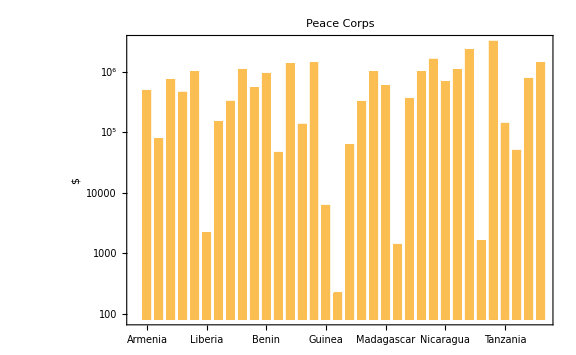

```mathematica
histPlotFin[New13,ToString[textlistMoney13]]
```

#### --- --- --- 4

```mathematica
textlistMoney14=Style[listMoney1[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New14=listMoney1[[4]]//Values
```

{{Jordan,3.0277335835999995e8 $},{Armenia,3.1095829800000004e6 $},{China,1.3e6 $},{Ethiopia,4.4639296879999995e7 $},{Georgia,1.498417201e7 $},{Kenya,4.9292370379999995e7 $},{Somalia,4.02e7 $},{Uganda,4.005722839e7 $},{Liberia,4.088812019e7 $},{Niger,1.161283706e7 $},{Guatemala,3.235284467e7 $},{Honduras,1.1885474190000001e7 $},{Mexico,150 000.00 $},{Peru,413 320.71 $},{Afghanistan,2.402814401e8 $},{Albania,3.03186475e6 $},{Azerbaijan,1.7749998e6 $},{Bangladesh,6.091500739999999e7 $},{Belarus,969 000.00 $},{Burundi,2.63826814e6 $},{Cambodia,4.91380328e6 $},{Djibouti,2.2e6 $},{Egypt,5.364720783e7 $},{Ghana,6.466257592999999e7 $},{Guinea,2.347e6 $},{Haiti,5.396934811e7 $},{India,1.098426103e7 $},{Indonesia,2.10633012e6 $},{Jamaica,1.1367216099999999e6 $},{Kosovo,1.9699587590000004e7 $},{Kyrgyzstan,1.069470049e7 $},{Laos,1.09990263e6 $},{Lebanon,1.180253416e7 $},{Macedonia,5.63041772e6 $},{Madagascar,5.105570609999999e6 $},{Malawi,4.507520605e7 $},{Mali,1.9861333880000003e7 $},{Moldova,6.38168365e6 $},{Mongolia,1.e6 $},{Morocco,6.203068e6 $},{Mozambique,3.101975835e7 $},{Nepal,3.3674619e7 $},{Nicaragua,877 991.95 $},{Nigeria,3.6138293739999995e7 $},{Pakistan,1.1630492046e8 $},{Paraguay,2.30014e6 $},{Philippines,1.01646571e7 $},{Rwanda,1.62602764e7 $},{Senegal,2.756593003e7 $},{Serbia,1.75962124e6 $},{Sudan,379 208.21 $},{Tajikistan,6.02363206e6 $},{Tanzania,4.834308706e7 $},{Tunisia,1.2947057e7 $},{Turkmenistan,843 000.00 $},{Ukraine,2.87310815e7 $},{Uzbekistan,554 000.00 $},{Vietnam,2.3733314299999997e6 $},{Yemen,87 503.65 $},{Zambia,1.448976447e7 $},{Zimbabwe,6.87043721e6 $}}

```mathematica
Length[New14]
```

61

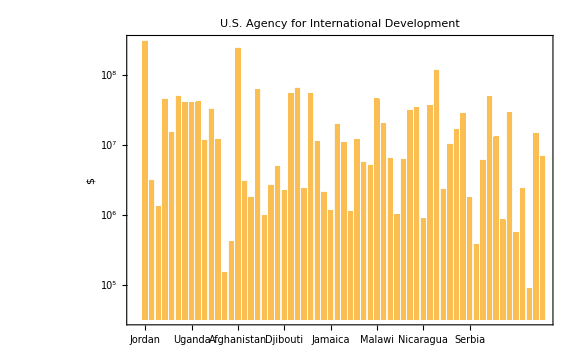

```mathematica
histPlotFin[New14,ToString[textlistMoney14]]
```

#### --- --- --- 5

```mathematica
textlistMoney15=Style[listMoney1[[5]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New15=listMoney1[[5]]//Values
```

{}

```mathematica
Length[New15]
```

0

```mathematica
histPlotFin[New15,ToString[textlistMoney15]]
```

-Graphics-

#### --- --- --- 6

```mathematica
textlistMoney16=Style[listMoney1[[6]][[1]]//Keys,FontColor->Red]
```

U.S. Department of the Treasury

```mathematica
New16=listMoney1[[6]]//Values
```

{{Jordan,15 971.80 $},{Angola,223 005.13 $},{Ethiopia,26 965.50 $},{Uganda,644 236.92 $},{Liberia,91 199.29 $},{Niger,274 137.59 $},{Honduras,298 453.65 $},{Peru,268 964.70 $},{Afghanistan,18 585.95 $},{Cambodia,679 127.04 $},{Colombia,165 938.75 $},{Djibouti,87 532.00 $},{Ghana,90 737.04 $},{Haiti,40 745.72 $},{India,50 811.25 $},{Indonesia,35 176.00 $},{Malawi,80 850.88 $},{Mongolia,946 779.26 $},{Nigeria,30 267.90 $},{Paraguay,712 807.29 $},{Philippines,810 978.20 $},{Rwanda,208 594.95 $},{Senegal,80 213.59 $},{Tanzania,888 033.79 $},{Vietnam,298 303.22 $},{Zambia,395 873.45 $}}

```mathematica
Length[New16]
```

26

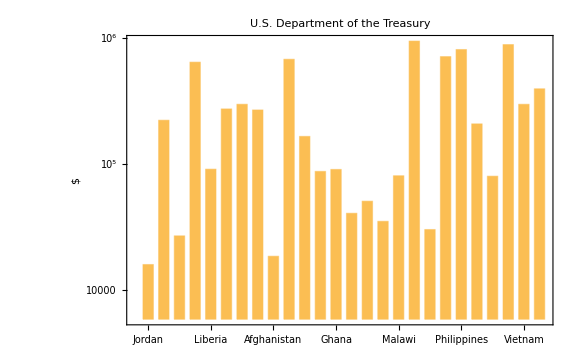

```mathematica
histPlotFin[New16,ToString[textlistMoney16]]
```

#### --- --- --- 7

```mathematica
textlistMoney17=Style[listMoney1[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New17=listMoney1[[7]]//Values
```

{{Ecuador,54 655.00 $},{Guatemala,127 072.00 $},{Honduras,213 675.00 $},{Mexico,109 812.00 $},{Belize,49 680.00 $},{Bolivia,109 940.00 $},{Brazil,377 994.00 $},{Haiti,128 000.00 $},{Nicaragua,31 724.00 $},{Paraguay,260 270.00 $}}

```mathematica
Length[New17]
```

10

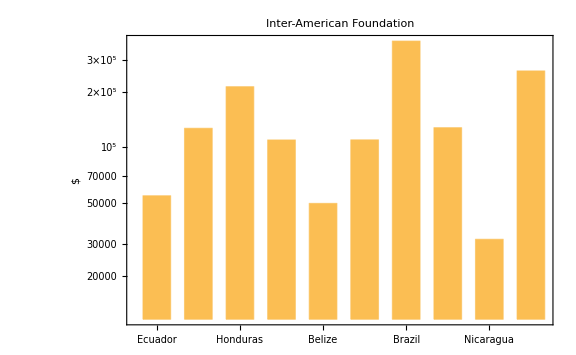

```mathematica
histPlotFin[New17,ToString[textlistMoney17]]
```

#### --- --- --- 8

```mathematica
textlistMoney18=Style[listMoney1[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New18=listMoney1[[8]]//Values
```

{}

```mathematica
Length[New18]
```

0

```mathematica
histPlotFin[New18,ToString[textlistMoney18]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney19=Style[listMoney1[[9]][[1]]//Keys,FontColor->Red]
```

U.S. African Development Foundation

```mathematica
New19=listMoney1[[9]]//Values
```

{{Ethiopia,655 000.00 $},{Kenya,1.30936701e6 $},{Somalia,975 408.00 $},{Uganda,2.112695e6 $},{Liberia,1.606926e6 $},{Niger,608 603.30 $},{Benin,1.18953003e6 $},{Burundi,754 274.99 $},{Chad,45 000.00 $},{Djibouti,25 000.00 $},{Ghana,414 187.34 $},{Guinea,273 749.03 $},{Madagascar,50 000.00 $},{Malawi,828 995.02 $},{Mali,821 977.99 $},{Mauritania,593 401.98 $},{Mauritius,25 000.00 $},{Nigeria,2.49794198e6 $},{Rwanda,1.45786202e6 $},{Senegal,740 139.13 $},{Tanzania,980 506.97 $},{Zambia,1.11498101e6 $},{Zimbabwe,1.493725e6 $}}

```mathematica
Length[New19]
```

23

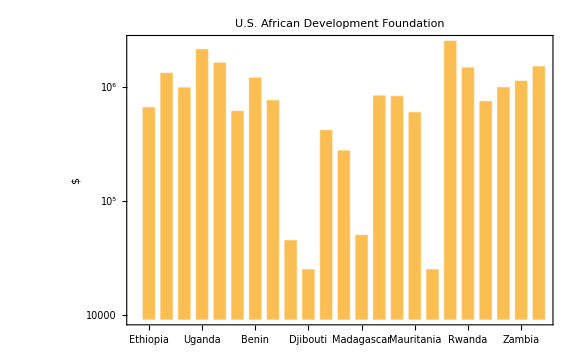

```mathematica
histPlotFin[New19,ToString[textlistMoney19]]
```

#### --- --- --- 10

```mathematica
textlistMoney110=Style[listMoney1[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New110=listMoney1[[10]]//Values
```

{}

```mathematica
Length[New110]
```

0

```mathematica
histPlotFin[New110,ToString[textlistMoney110]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney111=Style[listMoney1[[11]][[1]]//Keys,FontColor->Red]
```

Department of Labor

```mathematica
New111=listMoney1[[11]]//Values
```

{{Peru,1.e6 $},{Ghana,4.5e6 $},{Malaysia,1.e6 $},{Paraguay,6.e6 $},{Turkey,4.87e6 $}}

```mathematica
Length[New111]
```

5

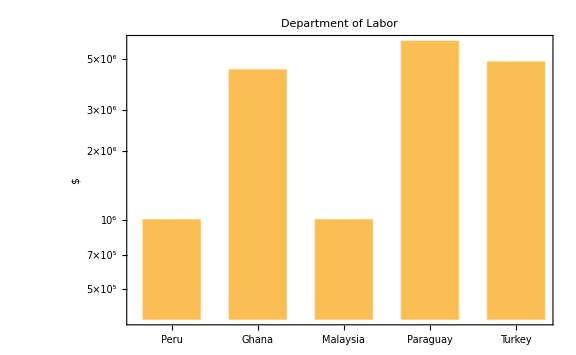

```mathematica
histPlotFin[New111,ToString[textlistMoney111]]
```

#### --- --- --- 12

```mathematica
textlistMoney112=Style[listMoney1[[12]][[1]]//Keys,FontColor->Red]
```

U.S. Department of Agriculture

```mathematica
New112=listMoney1[[12]]//Values
```

{{Liberia,929 623.57 $},{Honduras,1.488e8 $},{Bangladesh,465 912.00 $},{Cambodia,157 754.70 $},{Laos,448 635.14 $},{Nepal,237 171.14 $}}

```mathematica
Length[New112]
```

6

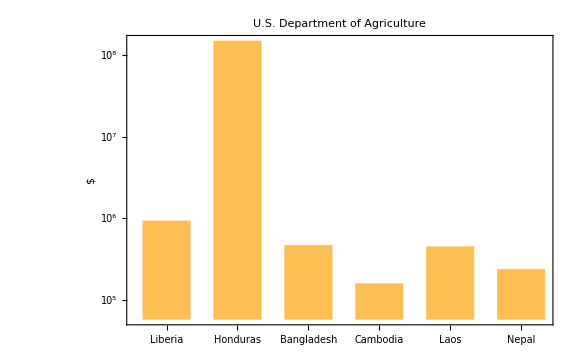

```mathematica
histPlotFin[New112,ToString[textlistMoney112]]
```

#### --- --- --- 13

```mathematica
textlistMoney113=Style[listMoney1[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation},{},{Department of Labor,Department of Labor,Department of Labor,Department of Labor,Department of Labor},{U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture}}

```mathematica
New113=listMoney1[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Jordan,2.e7 $},Overseas Private Investment Corporation→{Armenia,9.75e6 $},Overseas Private Investment Corporation→{Kenya,1.41e7 $},Overseas Private Investment Corporation→{Uganda,1.365e7 $},Overseas Private Investment Corporation→{Liberia,2.e7 $},Overseas Private Investment Corporation→{Mexico,4.4375e7 $},Overseas Private Investment Corporation→{Brazil,3.5e8 $},Overseas Private Investment Corporation→{Cambodia,1.55e8 $},Overseas Private Investment Corporation→{Colombia,2.56e8 $},Overseas Private Investment Corporation→{Egypt,5.5e6 $},Overseas Private Investment Corporation→{Guinea,1.5e8 $},Overseas Private Investment Corporation→{Haiti,9.e6 $},Overseas Private Investment Corporation→{India,4.94619295e8 $},Overseas Private Investment Corporation→{Indonesia,1.2e8 $},Overseas Private Investment Corporation→{Iraq,8.7e7 $},Overseas Private Investment Corporation→{Jamaica,1.5e7 $},Overseas Private Investment Corporation→{Nigeria,7.e7 $},Overseas Private Investment Corporation→{Pakistan,2.e7 $},Overseas Private Investment Corporation→{Panama,1.5e7 $},Overseas Private Investment Corporation→{Senegal,2.981e8 $},Overseas Private Investment Corporation→{Tanzania,1.5e7 $},Overseas Private Investment Corporation→{Turkey,9.75e6 $},Overseas Private Investment Corporation→{Zimbabwe,1.95e7 $}},{},{Peace Corps→{Armenia,488 291.00 $},Peace Corps→{Ethiopia,77 201.00 $},Peace Corps→{Georgia,738 570.00 $},Peace Corps→{Namibia,458 307.00 $},Peace Corps→{Uganda,1.000437e6 $},Peace Corps→{Liberia,2 188.00 $},Peace Corps→{Guatemala,148 714.00 $},Peace Corps→{Mexico,323 831.00 $},Peace Corps→{Peru,1.081918e6 $},Peace Corps→{Albania,542 421.00 $},Peace Corps→{Benin,931 307.00 $},Peace Corps→{Cambodia,46 189.00 $},Peace Corps→{Cameroon,1.355891e6 $},Peace Corps→{Colombia,135 742.00 $},Peace Corps→{Ghana,1.397098e6 $},Peace Corps→{Guinea,6 158.00 $},Peace Corps→{Jamaica,219.00 $},Peace Corps→{Kosovo,62 219.00 $},Peace Corps→{Kyrgyzstan,320 237.00 $},Peace Corps→{Macedonia,995 219.00 $},Peace Corps→{Madagascar,580 924.00 $},Peace Corps→{Malawi,1 397.00 $},Peace Corps→{Mali,359 450.00 $},Peace Corps→{Moldova,986 687.00 $},Peace Corps→{Nepal,1.60887e6 $},Peace Corps→{Nicaragua,678 981.00 $},Peace Corps→{Panama,1.068929e6 $},Peace Corps→{Paraguay,2.310485e6 $},Peace Corps→{Rwanda,1 609.00 $},Peace Corps→{Senegal,3.190278e6 $},Peace Corps→{Tanzania,139 977.00 $},Peace Corps→{Togo,50 082.00 $},Peace Corps→{Ukraine,772 598.00 $},Peace Corps→{Zambia,1.395886e6 $}},{U.S. Agency for International Development→{Jordan,3.0277335835999995e8 $},U.S. Agency for International Development→{Armenia,3.1095829800000004e6 $},U.S. Agency for International Development→{China,1.3e6 $},U.S. Agency for International Development→{Ethiopia,4.4639296879999995e7 $},U.S. Agency for International Development→{Georgia,1.498417201e7 $},U.S. Agency for International Development→{Kenya,4.9292370379999995e7 $},U.S. Agency for International Development→{Somalia,4.02e7 $},U.S. Agency for International Development→{Uganda,4.005722839e7 $},U.S. Agency for International Development→{Liberia,4.088812019e7 $},U.S. Agency for International Development→{Niger,1.161283706e7 $},U.S. Agency for International Development→{Guatemala,3.235284467e7 $},U.S. Agency for International Development→{Honduras,1.1885474190000001e7 $},U.S. Agency for International Development→{Mexico,150 000.00 $},U.S. Agency for International Development→{Peru,413 320.71 $},U.S. Agency for International Development→{Afghanistan,2.402814401e8 $},U.S. Agency for International Development→{Albania,3.03186475e6 $},U.S. Agency for International Development→{Azerbaijan,1.7749998e6 $},U.S. Agency for International Development→{Bangladesh,6.091500739999999e7 $},U.S. Agency for International Development→{Belarus,969 000.00 $},U.S. Agency for International Development→{Burundi,2.63826814e6 $},U.S. Agency for International Development→{Cambodia,4.91380328e6 $},U.S. Agency for International Development→{Djibouti,2.2e6 $},U.S. Agency for International Development→{Egypt,5.364720783e7 $},U.S. Agency for International Development→{Ghana,6.466257592999999e7 $},U.S. Agency for International Development→{Guinea,2.347e6 $},U.S. Agency for International Development→{Haiti,5.396934811e7 $},U.S. Agency for International Development→{India,1.098426103e7 $},U.S. Agency for International Development→{Indonesia,2.10633012e6 $},U.S. Agency for International Development→{Jamaica,1.1367216099999999e6 $},U.S. Agency for International Development→{Kosovo,1.9699587590000004e7 $},U.S. Agency for International Development→{Kyrgyzstan,1.069470049e7 $},U.S. Agency for International Development→{Laos,1.09990263e6 $},U.S. Agency for International Development→{Lebanon,1.180253416e7 $},U.S. Agency for International Development→{Macedonia,5.63041772e6 $},U.S. Agency for International Development→{Madagascar,5.105570609999999e6 $},U.S. Agency for International Development→{Malawi,4.507520605e7 $},U.S. Agency for International Development→{Mali,1.9861333880000003e7 $},U.S. Agency for International Development→{Moldova,6.38168365e6 $},U.S. Agency for International Development→{Mongolia,1.e6 $},U.S. Agency for International Development→{Morocco,6.203068e6 $},U.S. Agency for International Development→{Mozambique,3.101975835e7 $},U.S. Agency for International Development→{Nepal,3.3674619e7 $},U.S. Agency for International Development→{Nicaragua,877 991.95 $},U.S. Agency for International Development→{Nigeria,3.6138293739999995e7 $},U.S. Agency for International Development→{Pakistan,1.1630492046e8 $},U.S. Agency for International Development→{Paraguay,2.30014e6 $},U.S. Agency for International Development→{Philippines,1.01646571e7 $},U.S. Agency for International Development→{Rwanda,1.62602764e7 $},U.S. Agency for International Development→{Senegal,2.756593003e7 $},U.S. Agency for International Development→{Serbia,1.75962124e6 $},U.S. Agency for International Development→{Sudan,379 208.21 $},U.S. Agency for International Development→{Tajikistan,6.02363206e6 $},U.S. Agency for International Development→{Tanzania,4.834308706e7 $},U.S. Agency for International Development→{Tunisia,1.2947057e7 $},U.S. Agency for International Development→{Turkmenistan,843 000.00 $},U.S. Agency for International Development→{Ukraine,2.87310815e7 $},U.S. Agency for International Development→{Uzbekistan,554 000.00 $},U.S. Agency for International Development→{Vietnam,2.3733314299999997e6 $},U.S. Agency for International Development→{Yemen,87 503.65 $},U.S. Agency for International Development→{Zambia,1.448976447e7 $},U.S. Agency for International Development→{Zimbabwe,6.87043721e6 $}},{},{U.S. Department of the Treasury→{Jordan,15 971.80 $},U.S. Department of the Treasury→{Angola,223 005.13 $},U.S. Department of the Treasury→{Ethiopia,26 965.50 $},U.S. Department of the Treasury→{Uganda,644 236.92 $},U.S. Department of the Treasury→{Liberia,91 199.29 $},U.S. Department of the Treasury→{Niger,274 137.59 $},U.S. Department of the Treasury→{Honduras,298 453.65 $},U.S. Department of the Treasury→{Peru,268 964.70 $},U.S. Department of the Treasury→{Afghanistan,18 585.95 $},U.S. Department of the Treasury→{Cambodia,679 127.04 $},U.S. Department of the Treasury→{Colombia,165 938.75 $},U.S. Department of the Treasury→{Djibouti,87 532.00 $},U.S. Department of the Treasury→{Ghana,90 737.04 $},U.S. Department of the Treasury→{Haiti,40 745.72 $},U.S. Department of the Treasury→{India,50 811.25 $},U.S. Department of the Treasury→{Indonesia,35 176.00 $},U.S. Department of the Treasury→{Malawi,80 850.88 $},U.S. Department of the Treasury→{Mongolia,946 779.26 $},U.S. Department of the Treasury→{Nigeria,30 267.90 $},U.S. Department of the Treasury→{Paraguay,712 807.29 $},U.S. Department of the Treasury→{Philippines,810 978.20 $},U.S. Department of the Treasury→{Rwanda,208 594.95 $},U.S. Department of the Treasury→{Senegal,80 213.59 $},U.S. Department of the Treasury→{Tanzania,888 033.79 $},U.S. Department of the Treasury→{Vietnam,298 303.22 $},U.S. Department of the Treasury→{Zambia,395 873.45 $}},{Inter-American Foundation→{Ecuador,54 655.00 $},Inter-American Foundation→{Guatemala,127 072.00 $},Inter-American Foundation→{Honduras,213 675.00 $},Inter-American Foundation→{Mexico,109 812.00 $},Inter-American Foundation→{Belize,49 680.00 $},Inter-American Foundation→{Bolivia,109 940.00 $},Inter-American Foundation→{Brazil,377 994.00 $},Inter-American Foundation→{Haiti,128 000.00 $},Inter-American Foundation→{Nicaragua,31 724.00 $},Inter-American Foundation→{Paraguay,260 270.00 $}},{},{U.S. African Development Foundation→{Ethiopia,655 000.00 $},U.S. African Development Foundation→{Kenya,1.30936701e6 $},U.S. African Development Foundation→{Somalia,975 408.00 $},U.S. African Development Foundation→{Uganda,2.112695e6 $},U.S. African Development Foundation→{Liberia,1.606926e6 $},U.S. African Development Foundation→{Niger,608 603.30 $},U.S. African Development Foundation→{Benin,1.18953003e6 $},U.S. African Development Foundation→{Burundi,754 274.99 $},U.S. African Development Foundation→{Chad,45 000.00 $},U.S. African Development Foundation→{Djibouti,25 000.00 $},U.S. African Development Foundation→{Ghana,414 187.34 $},U.S. African Development Foundation→{Guinea,273 749.03 $},U.S. African Development Foundation→{Madagascar,50 000.00 $},U.S. African Development Foundation→{Malawi,828 995.02 $},U.S. African Development Foundation→{Mali,821 977.99 $},U.S. African Development Foundation→{Mauritania,593 401.98 $},U.S. African Development Foundation→{Mauritius,25 000.00 $},U.S. African Development Foundation→{Nigeria,2.49794198e6 $},U.S. African Development Foundation→{Rwanda,1.45786202e6 $},U.S. African Development Foundation→{Senegal,740 139.13 $},U.S. African Development Foundation→{Tanzania,980 506.97 $},U.S. African Development Foundation→{Zambia,1.11498101e6 $},U.S. African Development Foundation→{Zimbabwe,1.493725e6 $}},{},{Department of Labor→{Peru,1.e6 $},Department of Labor→{Ghana,4.5e6 $},Department of Labor→{Malaysia,1.e6 $},Department of Labor→{Paraguay,6.e6 $},Department of Labor→{Turkey,4.87e6 $}},{U.S. Department of Agriculture→{Liberia,929 623.57 $},U.S. Department of Agriculture→{Honduras,1.488e8 $},U.S. Department of Agriculture→{Bangladesh,465 912.00 $},U.S. Department of Agriculture→{Cambodia,157 754.70 $},U.S. Department of Agriculture→{Laos,448 635.14 $},U.S. Department of Agriculture→{Nepal,237 171.14 $}}}⟦13⟧]

```mathematica
Length[New113]
```

1

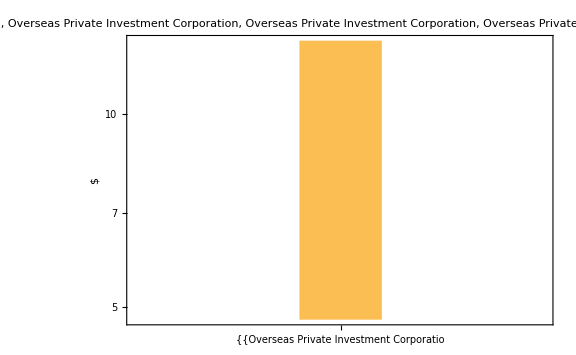

```mathematica
histPlotFin[New113,ToString[textlistMoney113]]
```

#### --- --- --- 14

```mathematica
textlistMoney114=Style[listMoney1[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation,Overseas Private Investment Corporation},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation},{},{Department of Labor,Department of Labor,Department of Labor,Department of Labor,Department of Labor},{U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture,U.S. Department of Agriculture}}

```mathematica
New114=listMoney1[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Jordan,2.e7 $},Overseas Private Investment Corporation→{Armenia,9.75e6 $},Overseas Private Investment Corporation→{Kenya,1.41e7 $},Overseas Private Investment Corporation→{Uganda,1.365e7 $},Overseas Private Investment Corporation→{Liberia,2.e7 $},Overseas Private Investment Corporation→{Mexico,4.4375e7 $},Overseas Private Investment Corporation→{Brazil,3.5e8 $},Overseas Private Investment Corporation→{Cambodia,1.55e8 $},Overseas Private Investment Corporation→{Colombia,2.56e8 $},Overseas Private Investment Corporation→{Egypt,5.5e6 $},Overseas Private Investment Corporation→{Guinea,1.5e8 $},Overseas Private Investment Corporation→{Haiti,9.e6 $},Overseas Private Investment Corporation→{India,4.94619295e8 $},Overseas Private Investment Corporation→{Indonesia,1.2e8 $},Overseas Private Investment Corporation→{Iraq,8.7e7 $},Overseas Private Investment Corporation→{Jamaica,1.5e7 $},Overseas Private Investment Corporation→{Nigeria,7.e7 $},Overseas Private Investment Corporation→{Pakistan,2.e7 $},Overseas Private Investment Corporation→{Panama,1.5e7 $},Overseas Private Investment Corporation→{Senegal,2.981e8 $},Overseas Private Investment Corporation→{Tanzania,1.5e7 $},Overseas Private Investment Corporation→{Turkey,9.75e6 $},Overseas Private Investment Corporation→{Zimbabwe,1.95e7 $}},{},{Peace Corps→{Armenia,488 291.00 $},Peace Corps→{Ethiopia,77 201.00 $},Peace Corps→{Georgia,738 570.00 $},Peace Corps→{Namibia,458 307.00 $},Peace Corps→{Uganda,1.000437e6 $},Peace Corps→{Liberia,2 188.00 $},Peace Corps→{Guatemala,148 714.00 $},Peace Corps→{Mexico,323 831.00 $},Peace Corps→{Peru,1.081918e6 $},Peace Corps→{Albania,542 421.00 $},Peace Corps→{Benin,931 307.00 $},Peace Corps→{Cambodia,46 189.00 $},Peace Corps→{Cameroon,1.355891e6 $},Peace Corps→{Colombia,135 742.00 $},Peace Corps→{Ghana,1.397098e6 $},Peace Corps→{Guinea,6 158.00 $},Peace Corps→{Jamaica,219.00 $},Peace Corps→{Kosovo,62 219.00 $},Peace Corps→{Kyrgyzstan,320 237.00 $},Peace Corps→{Macedonia,995 219.00 $},Peace Corps→{Madagascar,580 924.00 $},Peace Corps→{Malawi,1 397.00 $},Peace Corps→{Mali,359 450.00 $},Peace Corps→{Moldova,986 687.00 $},Peace Corps→{Nepal,1.60887e6 $},Peace Corps→{Nicaragua,678 981.00 $},Peace Corps→{Panama,1.068929e6 $},Peace Corps→{Paraguay,2.310485e6 $},Peace Corps→{Rwanda,1 609.00 $},Peace Corps→{Senegal,3.190278e6 $},Peace Corps→{Tanzania,139 977.00 $},Peace Corps→{Togo,50 082.00 $},Peace Corps→{Ukraine,772 598.00 $},Peace Corps→{Zambia,1.395886e6 $}},{U.S. Agency for International Development→{Jordan,3.0277335835999995e8 $},U.S. Agency for International Development→{Armenia,3.1095829800000004e6 $},U.S. Agency for International Development→{China,1.3e6 $},U.S. Agency for International Development→{Ethiopia,4.4639296879999995e7 $},U.S. Agency for International Development→{Georgia,1.498417201e7 $},U.S. Agency for International Development→{Kenya,4.9292370379999995e7 $},U.S. Agency for International Development→{Somalia,4.02e7 $},U.S. Agency for International Development→{Uganda,4.005722839e7 $},U.S. Agency for International Development→{Liberia,4.088812019e7 $},U.S. Agency for International Development→{Niger,1.161283706e7 $},U.S. Agency for International Development→{Guatemala,3.235284467e7 $},U.S. Agency for International Development→{Honduras,1.1885474190000001e7 $},U.S. Agency for International Development→{Mexico,150 000.00 $},U.S. Agency for International Development→{Peru,413 320.71 $},U.S. Agency for International Development→{Afghanistan,2.402814401e8 $},U.S. Agency for International Development→{Albania,3.03186475e6 $},U.S. Agency for International Development→{Azerbaijan,1.7749998e6 $},U.S. Agency for International Development→{Bangladesh,6.091500739999999e7 $},U.S. Agency for International Development→{Belarus,969 000.00 $},U.S. Agency for International Development→{Burundi,2.63826814e6 $},U.S. Agency for International Development→{Cambodia,4.91380328e6 $},U.S. Agency for International Development→{Djibouti,2.2e6 $},U.S. Agency for International Development→{Egypt,5.364720783e7 $},U.S. Agency for International Development→{Ghana,6.466257592999999e7 $},U.S. Agency for International Development→{Guinea,2.347e6 $},U.S. Agency for International Development→{Haiti,5.396934811e7 $},U.S. Agency for International Development→{India,1.098426103e7 $},U.S. Agency for International Development→{Indonesia,2.10633012e6 $},U.S. Agency for International Development→{Jamaica,1.1367216099999999e6 $},U.S. Agency for International Development→{Kosovo,1.9699587590000004e7 $},U.S. Agency for International Development→{Kyrgyzstan,1.069470049e7 $},U.S. Agency for International Development→{Laos,1.09990263e6 $},U.S. Agency for International Development→{Lebanon,1.180253416e7 $},U.S. Agency for International Development→{Macedonia,5.63041772e6 $},U.S. Agency for International Development→{Madagascar,5.105570609999999e6 $},U.S. Agency for International Development→{Malawi,4.507520605e7 $},U.S. Agency for International Development→{Mali,1.9861333880000003e7 $},U.S. Agency for International Development→{Moldova,6.38168365e6 $},U.S. Agency for International Development→{Mongolia,1.e6 $},U.S. Agency for International Development→{Morocco,6.203068e6 $},U.S. Agency for International Development→{Mozambique,3.101975835e7 $},U.S. Agency for International Development→{Nepal,3.3674619e7 $},U.S. Agency for International Development→{Nicaragua,877 991.95 $},U.S. Agency for International Development→{Nigeria,3.6138293739999995e7 $},U.S. Agency for International Development→{Pakistan,1.1630492046e8 $},U.S. Agency for International Development→{Paraguay,2.30014e6 $},U.S. Agency for International Development→{Philippines,1.01646571e7 $},U.S. Agency for International Development→{Rwanda,1.62602764e7 $},U.S. Agency for International Development→{Senegal,2.756593003e7 $},U.S. Agency for International Development→{Serbia,1.75962124e6 $},U.S. Agency for International Development→{Sudan,379 208.21 $},U.S. Agency for International Development→{Tajikistan,6.02363206e6 $},U.S. Agency for International Development→{Tanzania,4.834308706e7 $},U.S. Agency for International Development→{Tunisia,1.2947057e7 $},U.S. Agency for International Development→{Turkmenistan,843 000.00 $},U.S. Agency for International Development→{Ukraine,2.87310815e7 $},U.S. Agency for International Development→{Uzbekistan,554 000.00 $},U.S. Agency for International Development→{Vietnam,2.3733314299999997e6 $},U.S. Agency for International Development→{Yemen,87 503.65 $},U.S. Agency for International Development→{Zambia,1.448976447e7 $},U.S. Agency for International Development→{Zimbabwe,6.87043721e6 $}},{},{U.S. Department of the Treasury→{Jordan,15 971.80 $},U.S. Department of the Treasury→{Angola,223 005.13 $},U.S. Department of the Treasury→{Ethiopia,26 965.50 $},U.S. Department of the Treasury→{Uganda,644 236.92 $},U.S. Department of the Treasury→{Liberia,91 199.29 $},U.S. Department of the Treasury→{Niger,274 137.59 $},U.S. Department of the Treasury→{Honduras,298 453.65 $},U.S. Department of the Treasury→{Peru,268 964.70 $},U.S. Department of the Treasury→{Afghanistan,18 585.95 $},U.S. Department of the Treasury→{Cambodia,679 127.04 $},U.S. Department of the Treasury→{Colombia,165 938.75 $},U.S. Department of the Treasury→{Djibouti,87 532.00 $},U.S. Department of the Treasury→{Ghana,90 737.04 $},U.S. Department of the Treasury→{Haiti,40 745.72 $},U.S. Department of the Treasury→{India,50 811.25 $},U.S. Department of the Treasury→{Indonesia,35 176.00 $},U.S. Department of the Treasury→{Malawi,80 850.88 $},U.S. Department of the Treasury→{Mongolia,946 779.26 $},U.S. Department of the Treasury→{Nigeria,30 267.90 $},U.S. Department of the Treasury→{Paraguay,712 807.29 $},U.S. Department of the Treasury→{Philippines,810 978.20 $},U.S. Department of the Treasury→{Rwanda,208 594.95 $},U.S. Department of the Treasury→{Senegal,80 213.59 $},U.S. Department of the Treasury→{Tanzania,888 033.79 $},U.S. Department of the Treasury→{Vietnam,298 303.22 $},U.S. Department of the Treasury→{Zambia,395 873.45 $}},{Inter-American Foundation→{Ecuador,54 655.00 $},Inter-American Foundation→{Guatemala,127 072.00 $},Inter-American Foundation→{Honduras,213 675.00 $},Inter-American Foundation→{Mexico,109 812.00 $},Inter-American Foundation→{Belize,49 680.00 $},Inter-American Foundation→{Bolivia,109 940.00 $},Inter-American Foundation→{Brazil,377 994.00 $},Inter-American Foundation→{Haiti,128 000.00 $},Inter-American Foundation→{Nicaragua,31 724.00 $},Inter-American Foundation→{Paraguay,260 270.00 $}},{},{U.S. African Development Foundation→{Ethiopia,655 000.00 $},U.S. African Development Foundation→{Kenya,1.30936701e6 $},U.S. African Development Foundation→{Somalia,975 408.00 $},U.S. African Development Foundation→{Uganda,2.112695e6 $},U.S. African Development Foundation→{Liberia,1.606926e6 $},U.S. African Development Foundation→{Niger,608 603.30 $},U.S. African Development Foundation→{Benin,1.18953003e6 $},U.S. African Development Foundation→{Burundi,754 274.99 $},U.S. African Development Foundation→{Chad,45 000.00 $},U.S. African Development Foundation→{Djibouti,25 000.00 $},U.S. African Development Foundation→{Ghana,414 187.34 $},U.S. African Development Foundation→{Guinea,273 749.03 $},U.S. African Development Foundation→{Madagascar,50 000.00 $},U.S. African Development Foundation→{Malawi,828 995.02 $},U.S. African Development Foundation→{Mali,821 977.99 $},U.S. African Development Foundation→{Mauritania,593 401.98 $},U.S. African Development Foundation→{Mauritius,25 000.00 $},U.S. African Development Foundation→{Nigeria,2.49794198e6 $},U.S. African Development Foundation→{Rwanda,1.45786202e6 $},U.S. African Development Foundation→{Senegal,740 139.13 $},U.S. African Development Foundation→{Tanzania,980 506.97 $},U.S. African Development Foundation→{Zambia,1.11498101e6 $},U.S. African Development Foundation→{Zimbabwe,1.493725e6 $}},{},{Department of Labor→{Peru,1.e6 $},Department of Labor→{Ghana,4.5e6 $},Department of Labor→{Malaysia,1.e6 $},Department of Labor→{Paraguay,6.e6 $},Department of Labor→{Turkey,4.87e6 $}},{U.S. Department of Agriculture→{Liberia,929 623.57 $},U.S. Department of Agriculture→{Honduras,1.488e8 $},U.S. Department of Agriculture→{Bangladesh,465 912.00 $},U.S. Department of Agriculture→{Cambodia,157 754.70 $},U.S. Department of Agriculture→{Laos,448 635.14 $},U.S. Department of Agriculture→{Nepal,237 171.14 $}}}⟦14⟧]

```mathematica
Length[New114]
```

1

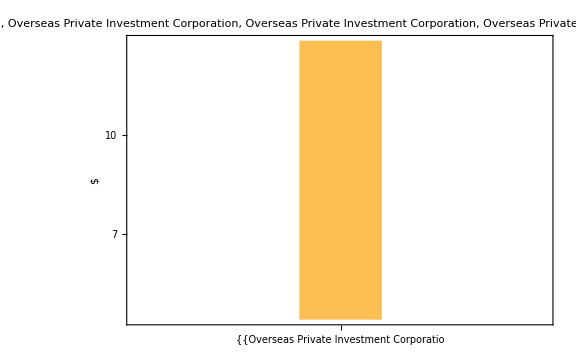

```mathematica
histPlotFin[New114,ToString[textlistMoney114]]
```

### listamountTOTNew[[2]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[2]]],FontColor->Red,Large]
```

Peace and Security

```mathematica
listMoney2=Map[Cases[Values[listamountTOTNewOhne0[[2]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney2//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney2[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→62,3→0,4→43,5→16,6→5,7→0,8→0,9→0,10→9,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney21=Style[listMoney2[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New21=listMoney2[[1]]//Values;
```

```mathematica
Length[New21]
```

0

```mathematica
histPlotFin[New21,ToString[textlistMoney21]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney22=Style[listMoney2[[2]][[1]]//Keys,FontColor->Red]
```

Department of Defense

```mathematica
New22=listMoney2[[2]]//Values
```

{{Jordan,1.5235e7 $},{Armenia,141 000.00 $},{Croatia,112 287.00 $},{Ethiopia,3 000.00 $},{Georgia,186 809.00 $},{Kenya,316 000.00 $},{Bulgaria,100 000.00 $},{Liberia,35 000.00 $},{Guatemala,2.8914e7 $},{Honduras,1.197e7 $},{Mexico,58 979.00 $},{Peru,1.5521e7 $},{Afghanistan,1.193e8 $},{Albania,225 000.00 $},{Azerbaijan,49 000.00 $},{Bahrain,558 000.00 $},{Bangladesh,208 000.00 $},{Barbados,438 000.00 $},{Belize,3.64e6 $},{Benin,1.337e6 $},{Cambodia,1.236e6 $},{Cameroon,2.646e6 $},{Colombia,7.193e7 $},{Comoros,5 000.00 $},{Cyprus,70 000.00 $},{Egypt,540 000.00 $},{Gabon,181 000.00 $},{Ghana,2.183e6 $},{Guinea,200 000.00 $},{India,94 616.00 $},{Iraq,200 000.00 $},{Jamaica,1.127e6 $},{Kazakhstan,1.3202e7 $},{Kosovo,125 000.00 $},{Kuwait,3 000.00 $},{Lebanon,1.7562e7 $},{Macedonia,350 000.00 $},{Maldives,147 000.00 $},{Mauritania,235 000.00 $},{Mauritius,4 000.00 $},{Moldova,2.827e6 $},{Nicaragua,2.373e6 $},{Nigeria,3.972e6 $},{Oman,339 000.00 $},{Pakistan,1.1819e7 $},{Palau,19 000.00 $},{Panama,8.078e6 $},{Philippines,2.0669e7 $},{Qatar,62 000.00 $},{Senegal,7.478e6 $},{Serbia,22 134.00 $},{Seychelles,26 000.00 $},{Tajikistan,1.1453e7 $},{Tanzania,246 000.00 $},{Thailand,3.027e6 $},{Togo,293 000.00 $},{Tunisia,2.4331e7 $},{Turkey,100 000.00 $},{Turkmenistan,81 000.00 $},{Ukraine,50 000.00 $},{Uzbekistan,1.1233e7 $},{Vietnam,1.136625e7 $}}

```mathematica
Length[New22]
```

62

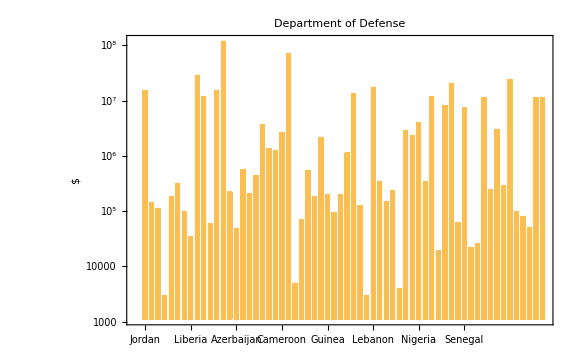

```mathematica
histPlotFin[New22,ToString[textlistMoney22]]
```

#### --- --- --- 3

```mathematica
textlistMoney23=Style[listMoney2[[3]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New23=listMoney2[[3]]//Values
```

{}

```mathematica
Length[New23]
```

0

```mathematica
histPlotFin[New23,ToString[textlistMoney23]]
```

-Graphics-

#### --- --- --- 4

```mathematica
textlistMoney24=Style[listMoney2[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New24=listMoney2[[4]]//Values
```

{{Ethiopia,1.943656e6 $},{Georgia,1.789e6 $},{Kenya,7.939286840000001e6 $},{Libya,1.3556e7 $},{Somalia,8.140158122e7 $},{Niger,6.507695e6 $},{Guatemala,1.48702062e6 $},{Honduras,100 000.00 $},{Peru,1.900996856e7 $},{Afghanistan,8.872870756e7 $},{Azerbaijan,200 000.00 $},{Bangladesh,89 012.38 $},{Belarus,241 000.00 $},{Burundi,1.9605238900000001e6 $},{Cameroon,4.16129699e6 $},{Chad,700 000.00 $},{Colombia,1.0470554505e8 $},{Guinea,2.0219406800000002e6 $},{Guyana,300 000.00 $},{Haiti,62 260.48 $},{Iraq,8.965979054e7 $},{Kazakhstan,225 000.00 $},{Kosovo,5.36867773e6 $},{Kyrgyzstan,217 036.88 $},{Lebanon,8.22408365e6 $},{Macedonia,7.01290699e6 $},{Mali,5.40812748e6 $},{Mauritania,329 282.96 $},{Morocco,1.146653e6 $},{Nepal,3.18572407e6 $},{Nigeria,5.347575658e7 $},{Pakistan,5.4770761e7 $},{Philippines,1.80650963e6 $},{Rwanda,1.09291198e6 $},{Senegal,1.08734386e6 $},{Serbia,2.e6 $},{Sudan,2.73558266e6 $},{Syria,9.432352036e7 $},{Thailand,1.0275e6 $},{Turkmenistan,99 000.00 $},{Ukraine,2.426109434e7 $},{Uzbekistan,325 108.62 $},{Zimbabwe,2.75634e6 $}}

```mathematica
Length[New24]
```

43

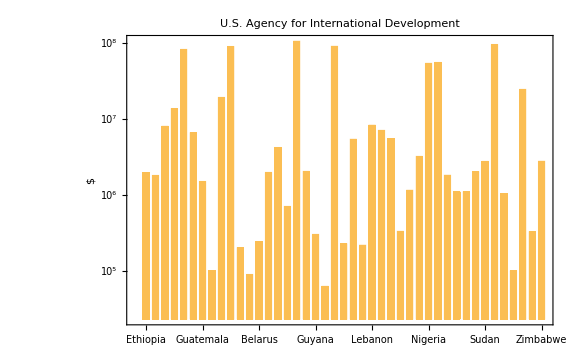

```mathematica
histPlotFin[New24,ToString[textlistMoney24]]
```

#### --- --- --- 5

```mathematica
textlistMoney25=Style[listMoney2[[5]][[1]]//Keys,FontColor->Red]
```

U.S. Department of State

```mathematica
New25=listMoney2[[5]]//Values
```

{{Armenia,57 468.94 $},{Somalia,248 813.38 $},{Liberia,2.2583474700000007e6 $},{Guatemala,1.74211261e6 $},{Honduras,798 200.26 $},{Mexico,452 061.70 $},{Afghanistan,1.29113501e6 $},{Belize,1.14820354e6 $},{Colombia,7.385825789999999e6 $},{Indonesia,2 959.00 $},{Jamaica,203 495.00 $},{Lebanon,2.7967738499999996e6 $},{Pakistan,1.025047291e7 $},{Panama,374 168.27 $},{Tunisia,359 421.40 $},{Ukraine,219 161.94 $}}

```mathematica
Length[New25]
```

16

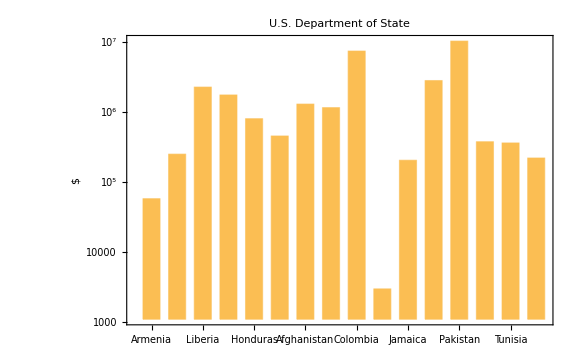

```mathematica
histPlotFin[New25,ToString[textlistMoney25]]
```

#### --- --- --- 6

```mathematica
textlistMoney26=Style[listMoney2[[6]][[1]]//Keys,FontColor->Red]
```

U.S. Department of the Treasury

```mathematica
New26=listMoney2[[6]]//Values
```

{{Liberia,101 725.09 $},{Honduras,2 507.15 $},{Peru,184 186.18 $},{Cambodia,110 866.74 $},{Ghana,30 015.58 $}}

```mathematica
Length[New26]
```

5

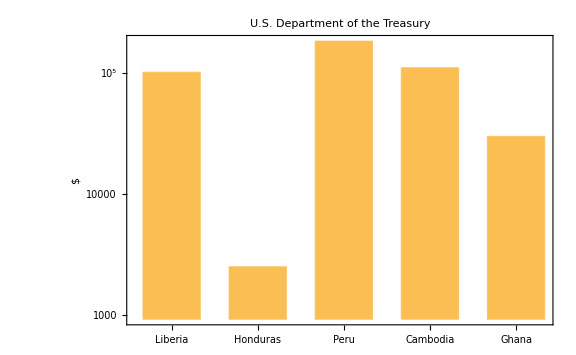

```mathematica
histPlotFin[New26,ToString[textlistMoney26]]
```

#### --- --- --- 7

```mathematica
textlistMoney27=Style[listMoney2[[7]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New27=listMoney2[[7]]//Values
```

{}

```mathematica
Length[New27]
```

0

```mathematica
histPlotFin[New27,ToString[textlistMoney27]]
```

-Graphics-

#### --- --- --- 8

```mathematica
textlistMoney28=Style[listMoney2[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New28=listMoney2[[8]]//Values
```

{}

```mathematica
Length[New28]
```

0

```mathematica
histPlotFin[New28,ToString[textlistMoney28]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney29=Style[listMoney2[[9]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New29=listMoney2[[9]]//Values
```

{}

```mathematica
Length[New29]
```

0

```mathematica
histPlotFin[New29,ToString[textlistMoney29]]
```

-Graphics-

#### --- --- --- 10

```mathematica
textlistMoney210=Style[listMoney2[[10]][[1]]//Keys,FontColor->Red]
```

Department of Justice

```mathematica
New210=listMoney2[[10]]//Values
```

{{Mexico,123 090.00 $},{Peru,16 420.00 $},{Bangladesh,27 554.18 $},{Botswana,1 430.41 $},{Hungary,7 018.50 $},{Kyrgyzstan,143.00 $},{Tajikistan,43 970.34 $},{Thailand,71 618.21 $},{Turkey,209 559.32 $}}

```mathematica
Length[New210]
```

9

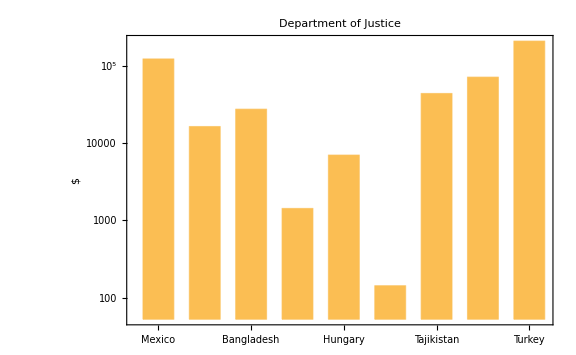

```mathematica
histPlotFin[New210,ToString[textlistMoney210]]
```

#### --- --- --- 11

```mathematica
textlistMoney211=Style[listMoney2[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New211=listMoney2[[11]]//Values
```

{}

```mathematica
Length[New211]
```

0

```mathematica
histPlotFin[New211,ToString[textlistMoney211]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney212=Style[listMoney2[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New212=listMoney2[[12]]//Values
```

{}

```mathematica
Length[New212]
```

0

```mathematica
histPlotFin[New212,ToString[textlistMoney212]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney213=Style[listMoney2[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of {{},«10»,{}} does not exist.

{{},{Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{},{},{},{Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice},{},{}}

```mathematica
New213=listMoney2[[13]]//Values
```

Part::partw: Part 13 of {{},«10»,{}} does not exist.

Values::invrl: The argument {{},«10»,{}}⟦13⟧ is not a valid Association or a list of rules.

Values[{{},{Department of Defense→{Jordan,1.5235e7 $},Department of Defense→{Armenia,141 000.00 $},Department of Defense→{Croatia,112 287.00 $},Department of Defense→{Ethiopia,3 000.00 $},Department of Defense→{Georgia,186 809.00 $},Department of Defense→{Kenya,316 000.00 $},Department of Defense→{Bulgaria,100 000.00 $},Department of Defense→{Liberia,35 000.00 $},Department of Defense→{Guatemala,2.8914e7 $},Department of Defense→{Honduras,1.197e7 $},Department of Defense→{Mexico,58 979.00 $},Department of Defense→{Peru,1.5521e7 $},Department of Defense→{Afghanistan,1.193e8 $},Department of Defense→{Albania,225 000.00 $},Department of Defense→{Azerbaijan,49 000.00 $},Department of Defense→{Bahrain,558 000.00 $},Department of Defense→{Bangladesh,208 000.00 $},Department of Defense→{Barbados,438 000.00 $},Department of Defense→{Belize,3.64e6 $},Department of Defense→{Benin,1.337e6 $},Department of Defense→{Cambodia,1.236e6 $},Department of Defense→{Cameroon,2.646e6 $},Department of Defense→{Colombia,7.193e7 $},Department of Defense→{Comoros,5 000.00 $},Department of Defense→{Cyprus,70 000.00 $},Department of Defense→{Egypt,540 000.00 $},Department of Defense→{Gabon,181 000.00 $},Department of Defense→{Ghana,2.183e6 $},Department of Defense→{Guinea,200 000.00 $},Department of Defense→{India,94 616.00 $},Department of Defense→{Iraq,200 000.00 $},Department of Defense→{Jamaica,1.127e6 $},Department of Defense→{Kazakhstan,1.3202e7 $},Department of Defense→{Kosovo,125 000.00 $},Department of Defense→{Kuwait,3 000.00 $},Department of Defense→{Lebanon,1.7562e7 $},Department of Defense→{Macedonia,350 000.00 $},Department of Defense→{Maldives,147 000.00 $},Department of Defense→{Mauritania,235 000.00 $},Department of Defense→{Mauritius,4 000.00 $},Department of Defense→{Moldova,2.827e6 $},Department of Defense→{Nicaragua,2.373e6 $},Department of Defense→{Nigeria,3.972e6 $},Department of Defense→{Oman,339 000.00 $},Department of Defense→{Pakistan,1.1819e7 $},Department of Defense→{Palau,19 000.00 $},Department of Defense→{Panama,8.078e6 $},Department of Defense→{Philippines,2.0669e7 $},Department of Defense→{Qatar,62 000.00 $},Department of Defense→{Senegal,7.478e6 $},Department of Defense→{Serbia,22 134.00 $},Department of Defense→{Seychelles,26 000.00 $},Department of Defense→{Tajikistan,1.1453e7 $},Department of Defense→{Tanzania,246 000.00 $},Department of Defense→{Thailand,3.027e6 $},Department of Defense→{Togo,293 000.00 $},Department of Defense→{Tunisia,2.4331e7 $},Department of Defense→{Turkey,100 000.00 $},Department of Defense→{Turkmenistan,81 000.00 $},Department of Defense→{Ukraine,50 000.00 $},Department of Defense→{Uzbekistan,1.1233e7 $},Department of Defense→{Vietnam,1.136625e7 $}},{},{U.S. Agency for International Development→{Ethiopia,1.943656e6 $},U.S. Agency for International Development→{Georgia,1.789e6 $},U.S. Agency for International Development→{Kenya,7.939286840000001e6 $},U.S. Agency for International Development→{Libya,1.3556e7 $},U.S. Agency for International Development→{Somalia,8.140158122e7 $},U.S. Agency for International Development→{Niger,6.507695e6 $},U.S. Agency for International Development→{Guatemala,1.48702062e6 $},U.S. Agency for International Development→{Honduras,100 000.00 $},U.S. Agency for International Development→{Peru,1.900996856e7 $},U.S. Agency for International Development→{Afghanistan,8.872870756e7 $},U.S. Agency for International Development→{Azerbaijan,200 000.00 $},U.S. Agency for International Development→{Bangladesh,89 012.38 $},U.S. Agency for International Development→{Belarus,241 000.00 $},U.S. Agency for International Development→{Burundi,1.9605238900000001e6 $},U.S. Agency for International Development→{Cameroon,4.16129699e6 $},U.S. Agency for International Development→{Chad,700 000.00 $},U.S. Agency for International Development→{Colombia,1.0470554505e8 $},U.S. Agency for International Development→{Guinea,2.0219406800000002e6 $},U.S. Agency for International Development→{Guyana,300 000.00 $},U.S. Agency for International Development→{Haiti,62 260.48 $},U.S. Agency for International Development→{Iraq,8.965979054e7 $},U.S. Agency for International Development→{Kazakhstan,225 000.00 $},U.S. Agency for International Development→{Kosovo,5.36867773e6 $},U.S. Agency for International Development→{Kyrgyzstan,217 036.88 $},U.S. Agency for International Development→{Lebanon,8.22408365e6 $},U.S. Agency for International Development→{Macedonia,7.01290699e6 $},U.S. Agency for International Development→{Mali,5.40812748e6 $},U.S. Agency for International Development→{Mauritania,329 282.96 $},U.S. Agency for International Development→{Morocco,1.146653e6 $},U.S. Agency for International Development→{Nepal,3.18572407e6 $},U.S. Agency for International Development→{Nigeria,5.347575658e7 $},U.S. Agency for International Development→{Pakistan,5.4770761e7 $},U.S. Agency for International Development→{Philippines,1.80650963e6 $},U.S. Agency for International Development→{Rwanda,1.09291198e6 $},U.S. Agency for International Development→{Senegal,1.08734386e6 $},U.S. Agency for International Development→{Serbia,2.e6 $},U.S. Agency for International Development→{Sudan,2.73558266e6 $},U.S. Agency for International Development→{Syria,9.432352036e7 $},U.S. Agency for International Development→{Thailand,1.0275e6 $},U.S. Agency for International Development→{Turkmenistan,99 000.00 $},U.S. Agency for International Development→{Ukraine,2.426109434e7 $},U.S. Agency for International Development→{Uzbekistan,325 108.62 $},U.S. Agency for International Development→{Zimbabwe,2.75634e6 $}},{U.S. Department of State→{Armenia,57 468.94 $},U.S. Department of State→{Somalia,248 813.38 $},U.S. Department of State→{Liberia,2.2583474700000007e6 $},U.S. Department of State→{Guatemala,1.74211261e6 $},U.S. Department of State→{Honduras,798 200.26 $},U.S. Department of State→{Mexico,452 061.70 $},U.S. Department of State→{Afghanistan,1.29113501e6 $},U.S. Department of State→{Belize,1.14820354e6 $},U.S. Department of State→{Colombia,7.385825789999999e6 $},U.S. Department of State→{Indonesia,2 959.00 $},U.S. Department of State→{Jamaica,203 495.00 $},U.S. Department of State→{Lebanon,2.7967738499999996e6 $},U.S. Department of State→{Pakistan,1.025047291e7 $},U.S. Department of State→{Panama,374 168.27 $},U.S. Department of State→{Tunisia,359 421.40 $},U.S. Department of State→{Ukraine,219 161.94 $}},{U.S. Department of the Treasury→{Liberia,101 725.09 $},U.S. Department of the Treasury→{Honduras,2 507.15 $},U.S. Department of the Treasury→{Peru,184 186.18 $},U.S. Department of the Treasury→{Cambodia,110 866.74 $},U.S. Department of the Treasury→{Ghana,30 015.58 $}},{},{},{},{Department of Justice→{Mexico,123 090.00 $},Department of Justice→{Peru,16 420.00 $},Department of Justice→{Bangladesh,27 554.18 $},Department of Justice→{Botswana,1 430.41 $},Department of Justice→{Hungary,7 018.50 $},Department of Justice→{Kyrgyzstan,143.00 $},Department of Justice→{Tajikistan,43 970.34 $},Department of Justice→{Thailand,71 618.21 $},Department of Justice→{Turkey,209 559.32 $}},{},{}}⟦13⟧]

```mathematica
Length[New213]
```

1

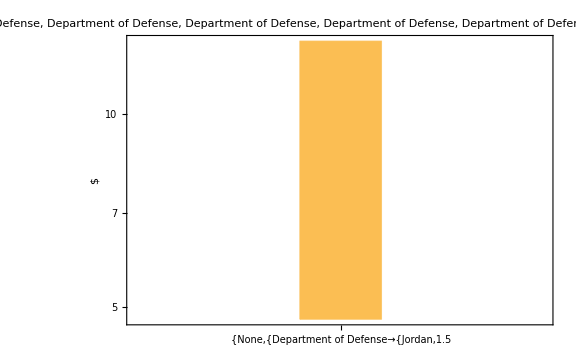

```mathematica
histPlotFin[New213,ToString[textlistMoney213]]
```

#### --- --- --- 14

```mathematica
textlistMoney214=Style[listMoney2[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of {{},«10»,{}} does not exist.

{{},{Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{},{},{},{Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice,Department of Justice},{},{}}

```mathematica
New214=listMoney2[[14]]//Values
```

Part::partw: Part 14 of {{},«10»,{}} does not exist.

Values::invrl: The argument {{},«10»,{}}⟦14⟧ is not a valid Association or a list of rules.

Values[{{},{Department of Defense→{Jordan,1.5235e7 $},Department of Defense→{Armenia,141 000.00 $},Department of Defense→{Croatia,112 287.00 $},Department of Defense→{Ethiopia,3 000.00 $},Department of Defense→{Georgia,186 809.00 $},Department of Defense→{Kenya,316 000.00 $},Department of Defense→{Bulgaria,100 000.00 $},Department of Defense→{Liberia,35 000.00 $},Department of Defense→{Guatemala,2.8914e7 $},Department of Defense→{Honduras,1.197e7 $},Department of Defense→{Mexico,58 979.00 $},Department of Defense→{Peru,1.5521e7 $},Department of Defense→{Afghanistan,1.193e8 $},Department of Defense→{Albania,225 000.00 $},Department of Defense→{Azerbaijan,49 000.00 $},Department of Defense→{Bahrain,558 000.00 $},Department of Defense→{Bangladesh,208 000.00 $},Department of Defense→{Barbados,438 000.00 $},Department of Defense→{Belize,3.64e6 $},Department of Defense→{Benin,1.337e6 $},Department of Defense→{Cambodia,1.236e6 $},Department of Defense→{Cameroon,2.646e6 $},Department of Defense→{Colombia,7.193e7 $},Department of Defense→{Comoros,5 000.00 $},Department of Defense→{Cyprus,70 000.00 $},Department of Defense→{Egypt,540 000.00 $},Department of Defense→{Gabon,181 000.00 $},Department of Defense→{Ghana,2.183e6 $},Department of Defense→{Guinea,200 000.00 $},Department of Defense→{India,94 616.00 $},Department of Defense→{Iraq,200 000.00 $},Department of Defense→{Jamaica,1.127e6 $},Department of Defense→{Kazakhstan,1.3202e7 $},Department of Defense→{Kosovo,125 000.00 $},Department of Defense→{Kuwait,3 000.00 $},Department of Defense→{Lebanon,1.7562e7 $},Department of Defense→{Macedonia,350 000.00 $},Department of Defense→{Maldives,147 000.00 $},Department of Defense→{Mauritania,235 000.00 $},Department of Defense→{Mauritius,4 000.00 $},Department of Defense→{Moldova,2.827e6 $},Department of Defense→{Nicaragua,2.373e6 $},Department of Defense→{Nigeria,3.972e6 $},Department of Defense→{Oman,339 000.00 $},Department of Defense→{Pakistan,1.1819e7 $},Department of Defense→{Palau,19 000.00 $},Department of Defense→{Panama,8.078e6 $},Department of Defense→{Philippines,2.0669e7 $},Department of Defense→{Qatar,62 000.00 $},Department of Defense→{Senegal,7.478e6 $},Department of Defense→{Serbia,22 134.00 $},Department of Defense→{Seychelles,26 000.00 $},Department of Defense→{Tajikistan,1.1453e7 $},Department of Defense→{Tanzania,246 000.00 $},Department of Defense→{Thailand,3.027e6 $},Department of Defense→{Togo,293 000.00 $},Department of Defense→{Tunisia,2.4331e7 $},Department of Defense→{Turkey,100 000.00 $},Department of Defense→{Turkmenistan,81 000.00 $},Department of Defense→{Ukraine,50 000.00 $},Department of Defense→{Uzbekistan,1.1233e7 $},Department of Defense→{Vietnam,1.136625e7 $}},{},{U.S. Agency for International Development→{Ethiopia,1.943656e6 $},U.S. Agency for International Development→{Georgia,1.789e6 $},U.S. Agency for International Development→{Kenya,7.939286840000001e6 $},U.S. Agency for International Development→{Libya,1.3556e7 $},U.S. Agency for International Development→{Somalia,8.140158122e7 $},U.S. Agency for International Development→{Niger,6.507695e6 $},U.S. Agency for International Development→{Guatemala,1.48702062e6 $},U.S. Agency for International Development→{Honduras,100 000.00 $},U.S. Agency for International Development→{Peru,1.900996856e7 $},U.S. Agency for International Development→{Afghanistan,8.872870756e7 $},U.S. Agency for International Development→{Azerbaijan,200 000.00 $},U.S. Agency for International Development→{Bangladesh,89 012.38 $},U.S. Agency for International Development→{Belarus,241 000.00 $},U.S. Agency for International Development→{Burundi,1.9605238900000001e6 $},U.S. Agency for International Development→{Cameroon,4.16129699e6 $},U.S. Agency for International Development→{Chad,700 000.00 $},U.S. Agency for International Development→{Colombia,1.0470554505e8 $},U.S. Agency for International Development→{Guinea,2.0219406800000002e6 $},U.S. Agency for International Development→{Guyana,300 000.00 $},U.S. Agency for International Development→{Haiti,62 260.48 $},U.S. Agency for International Development→{Iraq,8.965979054e7 $},U.S. Agency for International Development→{Kazakhstan,225 000.00 $},U.S. Agency for International Development→{Kosovo,5.36867773e6 $},U.S. Agency for International Development→{Kyrgyzstan,217 036.88 $},U.S. Agency for International Development→{Lebanon,8.22408365e6 $},U.S. Agency for International Development→{Macedonia,7.01290699e6 $},U.S. Agency for International Development→{Mali,5.40812748e6 $},U.S. Agency for International Development→{Mauritania,329 282.96 $},U.S. Agency for International Development→{Morocco,1.146653e6 $},U.S. Agency for International Development→{Nepal,3.18572407e6 $},U.S. Agency for International Development→{Nigeria,5.347575658e7 $},U.S. Agency for International Development→{Pakistan,5.4770761e7 $},U.S. Agency for International Development→{Philippines,1.80650963e6 $},U.S. Agency for International Development→{Rwanda,1.09291198e6 $},U.S. Agency for International Development→{Senegal,1.08734386e6 $},U.S. Agency for International Development→{Serbia,2.e6 $},U.S. Agency for International Development→{Sudan,2.73558266e6 $},U.S. Agency for International Development→{Syria,9.432352036e7 $},U.S. Agency for International Development→{Thailand,1.0275e6 $},U.S. Agency for International Development→{Turkmenistan,99 000.00 $},U.S. Agency for International Development→{Ukraine,2.426109434e7 $},U.S. Agency for International Development→{Uzbekistan,325 108.62 $},U.S. Agency for International Development→{Zimbabwe,2.75634e6 $}},{U.S. Department of State→{Armenia,57 468.94 $},U.S. Department of State→{Somalia,248 813.38 $},U.S. Department of State→{Liberia,2.2583474700000007e6 $},U.S. Department of State→{Guatemala,1.74211261e6 $},U.S. Department of State→{Honduras,798 200.26 $},U.S. Department of State→{Mexico,452 061.70 $},U.S. Department of State→{Afghanistan,1.29113501e6 $},U.S. Department of State→{Belize,1.14820354e6 $},U.S. Department of State→{Colombia,7.385825789999999e6 $},U.S. Department of State→{Indonesia,2 959.00 $},U.S. Department of State→{Jamaica,203 495.00 $},U.S. Department of State→{Lebanon,2.7967738499999996e6 $},U.S. Department of State→{Pakistan,1.025047291e7 $},U.S. Department of State→{Panama,374 168.27 $},U.S. Department of State→{Tunisia,359 421.40 $},U.S. Department of State→{Ukraine,219 161.94 $}},{U.S. Department of the Treasury→{Liberia,101 725.09 $},U.S. Department of the Treasury→{Honduras,2 507.15 $},U.S. Department of the Treasury→{Peru,184 186.18 $},U.S. Department of the Treasury→{Cambodia,110 866.74 $},U.S. Department of the Treasury→{Ghana,30 015.58 $}},{},{},{},{Department of Justice→{Mexico,123 090.00 $},Department of Justice→{Peru,16 420.00 $},Department of Justice→{Bangladesh,27 554.18 $},Department of Justice→{Botswana,1 430.41 $},Department of Justice→{Hungary,7 018.50 $},Department of Justice→{Kyrgyzstan,143.00 $},Department of Justice→{Tajikistan,43 970.34 $},Department of Justice→{Thailand,71 618.21 $},Department of Justice→{Turkey,209 559.32 $}},{},{}}⟦14⟧]

```mathematica
Length[New214]
```

1

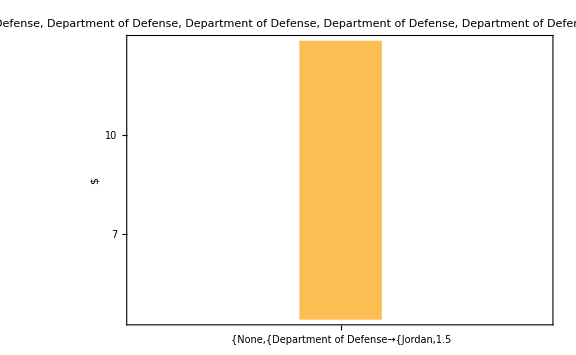

```mathematica
histPlotFin[New214,ToString[textlistMoney214]]
```

### listamountTOTNew[[3]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[3]]],FontColor->Red,Large]
```

Program Management

```mathematica
listMoney3=Map[Cases[Values[listamountTOTNewOhne0[[3]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney3//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney3[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→0,3→3,4→77,5→3,6→9,7→0,8→0,9→16,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney31=Style[listMoney3[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New31=listMoney3[[1]]//Values;
```

```mathematica
Length[New31]
```

0

```mathematica
histPlotFin[New31,ToString[textlistMoney31]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney32=Style[listMoney3[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New32=listMoney3[[2]]//Values
```

{}

```mathematica
Length[New32]
```

0

```mathematica
histPlotFin[New32,ToString[textlistMoney32]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney33=Style[listMoney3[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New33=listMoney3[[3]]//Values
```

{{Jordan,264 436.00 $},{Kenya,1.053738e6 $},{Romania,4.00 $}}

```mathematica
Length[New33]
```

3

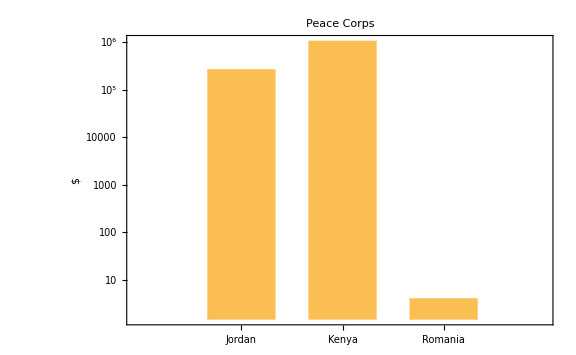

```mathematica
histPlotFin[New33,ToString[textlistMoney33]]
```

#### --- --- --- 4

```mathematica
textlistMoney34=Style[listMoney3[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New34=listMoney3[[4]]//Values
```

{{Jordan,1.004700979e7 $},{Angola,3.49930643e6 $},{Armenia,683 874.26 $},{Ethiopia,1.557969907e7 $},{Georgia,3.1474443699999996e6 $},{Kenya,1.182232768e7 $},{Libya,1.06450391e6 $},{Somalia,1.6401657660000002e7 $},{Uganda,1.2851949000000002e7 $},{Liberia,1.324125226e7 $},{Niger,730 394.12 $},{Venezuela,943 182.35 $},{Cuba,81 533.58 $},{Guatemala,7.469528640000001e6 $},{Honduras,1.3154059550000003e7 $},{Mexico,2.98286745e6 $},{Peru,6.22201625e6 $},{Afghanistan,5.917760775e7 $},{Albania,767 263.38 $},{Azerbaijan,1.4608661500000001e6 $},{Bangladesh,1.2503996749999998e7 $},{Belarus,251 464.30 $},{Benin,2.00523992e6 $},{Botswana,94 149.12 $},{Brazil,483 217.39 $},{Brunei,27 015.00 $},{Burundi,965 763.58 $},{Cambodia,6.296964369999999e6 $},{Cameroon,870 098.88 $},{Chad,168 457.67 $},{Colombia,1.2048301889999999e7 $},{Djibouti,606 643.89 $},{Ghana,1.1815852520000003e7 $},{Guinea,2.52673777e6 $},{Guyana,480 817.34 $},{Haiti,1.6569077950000001e7 $},{Hungary,902 851.18 $},{India,9.21651205e6 $},{Indonesia,1.306363326e7 $},{Jamaica,1.86717024e6 $},{Kazakhstan,484 630.95 $},{Kosovo,2.9156770200000005e6 $},{Kyrgyzstan,2.57555675e6 $},{Laos,244 956.96 $},{Lebanon,6.77210527e6 $},{Macedonia,2.0040435499999998e6 $},{Madagascar,3.42634859e6 $},{Malawi,1.6693399290000001e7 $},{Maldives,22 884.78 $},{Mali,7.171838040000001e6 $},{Moldova,1.0049578999999999e6 $},{Mongolia,3 011.13 $},{Morocco,1.2785360799999998e6 $},{Mozambique,6.865255430000001e6 $},{Nepal,8.88407694e6 $},{Nicaragua,1.95496283e6 $},{Nigeria,2.4905856839999996e7 $},{Pakistan,2.5335803700000003e7 $},{Paraguay,876 194.94 $},{Philippines,7.692691390000001e6 $},{Rwanda,8.819020360000001e6 $},{Senegal,7.31183478e6 $},{Serbia,723 617.36 $},{Sudan,2.19114266e6 $},{Syria,4.17768849e6 $},{Tajikistan,2.31807141e6 $},{Tanzania,1.169088128e7 $},{Thailand,956 881.21 $},{Tunisia,418 122.67 $},{Turkey,327 049.43 $},{Turkmenistan,168 602.30 $},{Ukraine,3.9299790500000003e6 $},{Uzbekistan,624 703.24 $},{Vietnam,4.77962513e6 $},{Yemen,1.67198281e6 $},{Zambia,3.1003446999999997e6 $},{Zimbabwe,8.41439967e6 $}}

```mathematica
Length[New34]
```

77

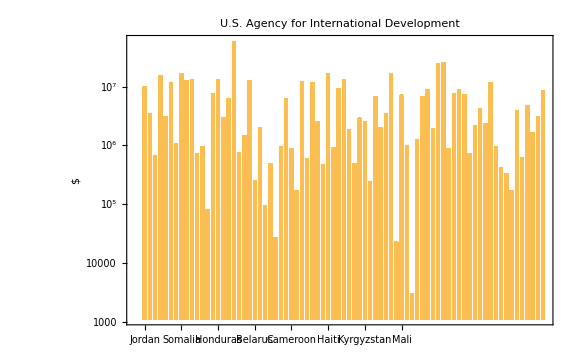

```mathematica
histPlotFin[New34,ToString[textlistMoney34]]
```

#### --- --- --- 5

```mathematica
textlistMoney35=Style[listMoney3[[5]][[1]]//Keys,FontColor->Red]
```

U.S. Department of State

```mathematica
New35=listMoney3[[5]]//Values
```

{{Honduras,198 724.30 $},{Nigeria,9 211.18 $},{Panama,71 093.50 $}}

```mathematica
Length[New35]
```

3

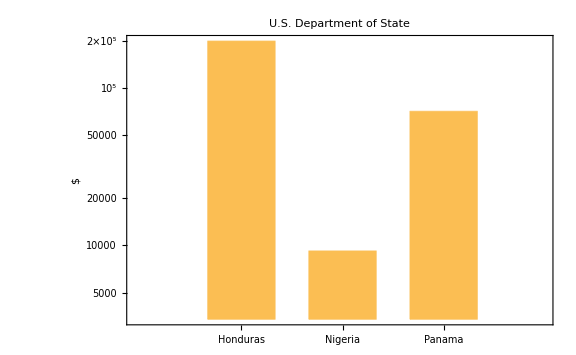

```mathematica
histPlotFin[New35,ToString[textlistMoney35]]
```

#### --- --- --- 6

```mathematica
textlistMoney36=Style[listMoney3[[6]][[1]]//Keys,FontColor->Red]
```

U.S. Department of the Treasury

```mathematica
New36=listMoney3[[6]]//Values
```

{{Ethiopia,110 690.42 $},{Liberia,32 125.84 $},{Peru,171 673.10 $},{Afghanistan,14 585.83 $},{Colombia,88 527.55 $},{India,32 000.00 $},{Indonesia,138 475.35 $},{Malawi,55 082.47 $},{Tanzania,9 157.43 $}}

```mathematica
Length[New36]
```

9

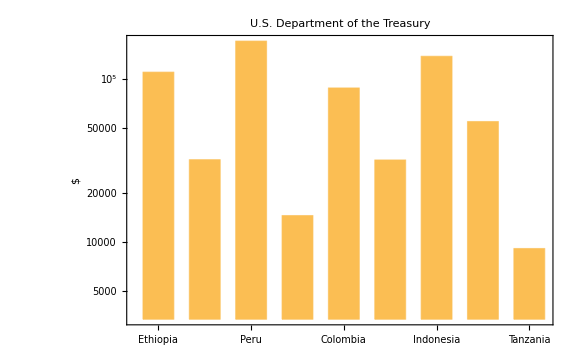

```mathematica
histPlotFin[New36,ToString[textlistMoney36]]
```

#### --- --- --- 7

```mathematica
textlistMoney37=Style[listMoney3[[7]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New37=listMoney3[[7]]//Values
```

{}

```mathematica
Length[New37]
```

0

```mathematica
histPlotFin[New37,ToString[textlistMoney37]]
```

-Graphics-

#### --- --- --- 8

```mathematica
textlistMoney38=Style[listMoney3[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New38=listMoney3[[8]]//Values
```

{}

```mathematica
Length[New38]
```

0

```mathematica
histPlotFin[New38,ToString[textlistMoney38]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney39=Style[listMoney3[[9]][[1]]//Keys,FontColor->Red]
```

U.S. African Development Foundation

```mathematica
New39=listMoney3[[9]]//Values
```

{{Ethiopia,112 563.07 $},{Kenya,465 128.38 $},{Somalia,490 000.00 $},{Niger,234 001.98 $},{Benin,290 750.01 $},{Burundi,210 947.99 $},{Ghana,267 556.00 $},{Malawi,270 000.00 $},{Mali,931 392.00 $},{Mauritania,502 000.00 $},{Nigeria,879 888.00 $},{Rwanda,289 693.00 $},{Senegal,253 743.02 $},{Tanzania,566 401.09 $},{Zambia,237 568.97 $},{Zimbabwe,315 000.00 $}}

```mathematica
Length[New39]
```

16

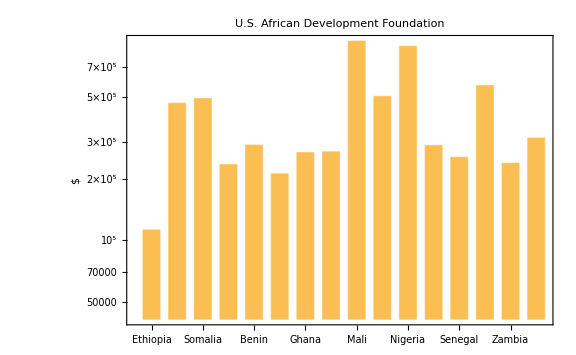

```mathematica
histPlotFin[New39,ToString[textlistMoney39]]
```

#### --- --- --- 10

```mathematica
textlistMoney310=Style[listMoney3[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New310=listMoney3[[10]]//Values
```

{}

```mathematica
Length[New310]
```

0

```mathematica
histPlotFin[New310,ToString[textlistMoney310]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney311=Style[listMoney3[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New311=listMoney3[[11]]//Values
```

{}

```mathematica
Length[New311]
```

0

```mathematica
histPlotFin[New311,ToString[textlistMoney311]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney312=Style[listMoney3[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New312=listMoney3[[12]]//Values
```

{}

```mathematica
Length[New312]
```

0

```mathematica
histPlotFin[New312,ToString[textlistMoney312]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney313=Style[listMoney3[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{},{},{U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation},{},{},{}}

```mathematica
New313=listMoney3[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument «1» is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Jordan,264 436.00 $},Peace Corps→{Kenya,1.053738e6 $},Peace Corps→{Romania,4.00 $}},{U.S. Agency for International Development→{Jordan,1.004700979e7 $},U.S. Agency for International Development→{Angola,3.49930643e6 $},U.S. Agency for International Development→{Armenia,683 874.26 $},U.S. Agency for International Development→{Ethiopia,1.557969907e7 $},U.S. Agency for International Development→{Georgia,3.1474443699999996e6 $},U.S. Agency for International Development→{Kenya,1.182232768e7 $},U.S. Agency for International Development→{Libya,1.06450391e6 $},U.S. Agency for International Development→{Somalia,1.6401657660000002e7 $},U.S. Agency for International Development→{Uganda,1.2851949000000002e7 $},U.S. Agency for International Development→{Liberia,1.324125226e7 $},U.S. Agency for International Development→{Niger,730 394.12 $},U.S. Agency for International Development→{Venezuela,943 182.35 $},U.S. Agency for International Development→{Cuba,81 533.58 $},U.S. Agency for International Development→{Guatemala,7.469528640000001e6 $},U.S. Agency for International Development→{Honduras,1.3154059550000003e7 $},U.S. Agency for International Development→{Mexico,2.98286745e6 $},U.S. Agency for International Development→{Peru,6.22201625e6 $},U.S. Agency for International Development→{Afghanistan,5.917760775e7 $},U.S. Agency for International Development→{Albania,767 263.38 $},U.S. Agency for International Development→{Azerbaijan,1.4608661500000001e6 $},U.S. Agency for International Development→{Bangladesh,1.2503996749999998e7 $},U.S. Agency for International Development→{Belarus,251 464.30 $},U.S. Agency for International Development→{Benin,2.00523992e6 $},U.S. Agency for International Development→{Botswana,94 149.12 $},U.S. Agency for International Development→{Brazil,483 217.39 $},U.S. Agency for International Development→{Brunei,27 015.00 $},U.S. Agency for International Development→{Burundi,965 763.58 $},U.S. Agency for International Development→{Cambodia,6.296964369999999e6 $},U.S. Agency for International Development→{Cameroon,870 098.88 $},U.S. Agency for International Development→{Chad,168 457.67 $},U.S. Agency for International Development→{Colombia,1.2048301889999999e7 $},U.S. Agency for International Development→{Djibouti,606 643.89 $},U.S. Agency for International Development→{Ghana,1.1815852520000003e7 $},U.S. Agency for International Development→{Guinea,2.52673777e6 $},U.S. Agency for International Development→{Guyana,480 817.34 $},U.S. Agency for International Development→{Haiti,1.6569077950000001e7 $},U.S. Agency for International Development→{Hungary,902 851.18 $},U.S. Agency for International Development→{India,9.21651205e6 $},U.S. Agency for International Development→{Indonesia,1.306363326e7 $},U.S. Agency for International Development→{Jamaica,1.86717024e6 $},U.S. Agency for International Development→{Kazakhstan,484 630.95 $},U.S. Agency for International Development→{Kosovo,2.9156770200000005e6 $},U.S. Agency for International Development→{Kyrgyzstan,2.57555675e6 $},U.S. Agency for International Development→{Laos,244 956.96 $},U.S. Agency for International Development→{Lebanon,6.77210527e6 $},U.S. Agency for International Development→{Macedonia,2.0040435499999998e6 $},U.S. Agency for International Development→{Madagascar,3.42634859e6 $},U.S. Agency for International Development→{Malawi,1.6693399290000001e7 $},U.S. Agency for International Development→{Maldives,22 884.78 $},U.S. Agency for International Development→{Mali,7.171838040000001e6 $},U.S. Agency for International Development→{Moldova,1.0049578999999999e6 $},U.S. Agency for International Development→{Mongolia,3 011.13 $},U.S. Agency for International Development→{Morocco,1.2785360799999998e6 $},U.S. Agency for International Development→{Mozambique,6.865255430000001e6 $},U.S. Agency for International Development→{Nepal,8.88407694e6 $},U.S. Agency for International Development→{Nicaragua,1.95496283e6 $},U.S. Agency for International Development→{Nigeria,2.4905856839999996e7 $},U.S. Agency for International Development→{Pakistan,2.5335803700000003e7 $},U.S. Agency for International Development→{Paraguay,876 194.94 $},U.S. Agency for International Development→{Philippines,7.692691390000001e6 $},U.S. Agency for International Development→{Rwanda,8.819020360000001e6 $},U.S. Agency for International Development→{Senegal,7.31183478e6 $},U.S. Agency for International Development→{Serbia,723 617.36 $},U.S. Agency for International Development→{Sudan,2.19114266e6 $},U.S. Agency for International Development→{Syria,4.17768849e6 $},U.S. Agency for International Development→{Tajikistan,2.31807141e6 $},U.S. Agency for International Development→{Tanzania,1.169088128e7 $},U.S. Agency for International Development→{Thailand,956 881.21 $},U.S. Agency for International Development→{Tunisia,418 122.67 $},U.S. Agency for International Development→{Turkey,327 049.43 $},U.S. Agency for International Development→{Turkmenistan,168 602.30 $},U.S. Agency for International Development→{Ukraine,3.9299790500000003e6 $},U.S. Agency for International Development→{Uzbekistan,624 703.24 $},U.S. Agency for International Development→{Vietnam,4.77962513e6 $},U.S. Agency for International Development→{Yemen,1.67198281e6 $},U.S. Agency for International Development→{Zambia,3.1003446999999997e6 $},U.S. Agency for International Development→{Zimbabwe,8.41439967e6 $}},{U.S. Department of State→{Honduras,198 724.30 $},U.S. Department of State→{Nigeria,9 211.18 $},U.S. Department of State→{Panama,71 093.50 $}},{U.S. Department of the Treasury→{Ethiopia,110 690.42 $},U.S. Department of the Treasury→{Liberia,32 125.84 $},U.S. Department of the Treasury→{Peru,171 673.10 $},U.S. Department of the Treasury→{Afghanistan,14 585.83 $},U.S. Department of the Treasury→{Colombia,88 527.55 $},U.S. Department of the Treasury→{India,32 000.00 $},U.S. Department of the Treasury→{Indonesia,138 475.35 $},U.S. Department of the Treasury→{Malawi,55 082.47 $},U.S. Department of the Treasury→{Tanzania,9 157.43 $}},{},{},{U.S. African Development Foundation→{Ethiopia,112 563.07 $},U.S. African Development Foundation→{Kenya,465 128.38 $},U.S. African Development Foundation→{Somalia,490 000.00 $},U.S. African Development Foundation→{Niger,234 001.98 $},U.S. African Development Foundation→{Benin,290 750.01 $},U.S. African Development Foundation→{Burundi,210 947.99 $},U.S. African Development Foundation→{Ghana,267 556.00 $},U.S. African Development Foundation→{Malawi,270 000.00 $},U.S. African Development Foundation→{Mali,931 392.00 $},U.S. African Development Foundation→{Mauritania,502 000.00 $},U.S. African Development Foundation→{Nigeria,879 888.00 $},U.S. African Development Foundation→{Rwanda,289 693.00 $},U.S. African Development Foundation→{Senegal,253 743.02 $},U.S. African Development Foundation→{Tanzania,566 401.09 $},U.S. African Development Foundation→{Zambia,237 568.97 $},U.S. African Development Foundation→{Zimbabwe,315 000.00 $}},{},{},{}}⟦13⟧]

```mathematica
Length[New313]
```

1

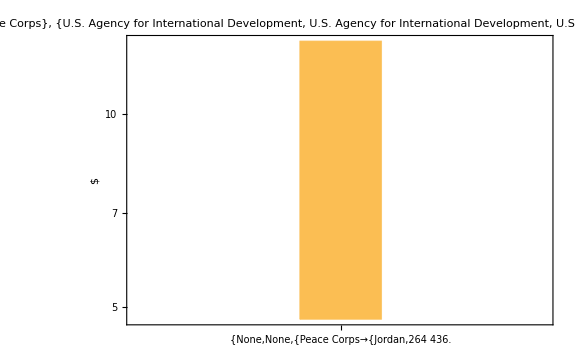

```mathematica
histPlotFin[New313,ToString[textlistMoney313]]
```

#### --- --- --- 14

```mathematica
textlistMoney314=Style[listMoney3[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State},{U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury,U.S. Department of the Treasury},{},{},{U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation,U.S. African Development Foundation},{},{},{}}

```mathematica
New314=listMoney3[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument «1» is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Jordan,264 436.00 $},Peace Corps→{Kenya,1.053738e6 $},Peace Corps→{Romania,4.00 $}},{U.S. Agency for International Development→{Jordan,1.004700979e7 $},U.S. Agency for International Development→{Angola,3.49930643e6 $},U.S. Agency for International Development→{Armenia,683 874.26 $},U.S. Agency for International Development→{Ethiopia,1.557969907e7 $},U.S. Agency for International Development→{Georgia,3.1474443699999996e6 $},U.S. Agency for International Development→{Kenya,1.182232768e7 $},U.S. Agency for International Development→{Libya,1.06450391e6 $},U.S. Agency for International Development→{Somalia,1.6401657660000002e7 $},U.S. Agency for International Development→{Uganda,1.2851949000000002e7 $},U.S. Agency for International Development→{Liberia,1.324125226e7 $},U.S. Agency for International Development→{Niger,730 394.12 $},U.S. Agency for International Development→{Venezuela,943 182.35 $},U.S. Agency for International Development→{Cuba,81 533.58 $},U.S. Agency for International Development→{Guatemala,7.469528640000001e6 $},U.S. Agency for International Development→{Honduras,1.3154059550000003e7 $},U.S. Agency for International Development→{Mexico,2.98286745e6 $},U.S. Agency for International Development→{Peru,6.22201625e6 $},U.S. Agency for International Development→{Afghanistan,5.917760775e7 $},U.S. Agency for International Development→{Albania,767 263.38 $},U.S. Agency for International Development→{Azerbaijan,1.4608661500000001e6 $},U.S. Agency for International Development→{Bangladesh,1.2503996749999998e7 $},U.S. Agency for International Development→{Belarus,251 464.30 $},U.S. Agency for International Development→{Benin,2.00523992e6 $},U.S. Agency for International Development→{Botswana,94 149.12 $},U.S. Agency for International Development→{Brazil,483 217.39 $},U.S. Agency for International Development→{Brunei,27 015.00 $},U.S. Agency for International Development→{Burundi,965 763.58 $},U.S. Agency for International Development→{Cambodia,6.296964369999999e6 $},U.S. Agency for International Development→{Cameroon,870 098.88 $},U.S. Agency for International Development→{Chad,168 457.67 $},U.S. Agency for International Development→{Colombia,1.2048301889999999e7 $},U.S. Agency for International Development→{Djibouti,606 643.89 $},U.S. Agency for International Development→{Ghana,1.1815852520000003e7 $},U.S. Agency for International Development→{Guinea,2.52673777e6 $},U.S. Agency for International Development→{Guyana,480 817.34 $},U.S. Agency for International Development→{Haiti,1.6569077950000001e7 $},U.S. Agency for International Development→{Hungary,902 851.18 $},U.S. Agency for International Development→{India,9.21651205e6 $},U.S. Agency for International Development→{Indonesia,1.306363326e7 $},U.S. Agency for International Development→{Jamaica,1.86717024e6 $},U.S. Agency for International Development→{Kazakhstan,484 630.95 $},U.S. Agency for International Development→{Kosovo,2.9156770200000005e6 $},U.S. Agency for International Development→{Kyrgyzstan,2.57555675e6 $},U.S. Agency for International Development→{Laos,244 956.96 $},U.S. Agency for International Development→{Lebanon,6.77210527e6 $},U.S. Agency for International Development→{Macedonia,2.0040435499999998e6 $},U.S. Agency for International Development→{Madagascar,3.42634859e6 $},U.S. Agency for International Development→{Malawi,1.6693399290000001e7 $},U.S. Agency for International Development→{Maldives,22 884.78 $},U.S. Agency for International Development→{Mali,7.171838040000001e6 $},U.S. Agency for International Development→{Moldova,1.0049578999999999e6 $},U.S. Agency for International Development→{Mongolia,3 011.13 $},U.S. Agency for International Development→{Morocco,1.2785360799999998e6 $},U.S. Agency for International Development→{Mozambique,6.865255430000001e6 $},U.S. Agency for International Development→{Nepal,8.88407694e6 $},U.S. Agency for International Development→{Nicaragua,1.95496283e6 $},U.S. Agency for International Development→{Nigeria,2.4905856839999996e7 $},U.S. Agency for International Development→{Pakistan,2.5335803700000003e7 $},U.S. Agency for International Development→{Paraguay,876 194.94 $},U.S. Agency for International Development→{Philippines,7.692691390000001e6 $},U.S. Agency for International Development→{Rwanda,8.819020360000001e6 $},U.S. Agency for International Development→{Senegal,7.31183478e6 $},U.S. Agency for International Development→{Serbia,723 617.36 $},U.S. Agency for International Development→{Sudan,2.19114266e6 $},U.S. Agency for International Development→{Syria,4.17768849e6 $},U.S. Agency for International Development→{Tajikistan,2.31807141e6 $},U.S. Agency for International Development→{Tanzania,1.169088128e7 $},U.S. Agency for International Development→{Thailand,956 881.21 $},U.S. Agency for International Development→{Tunisia,418 122.67 $},U.S. Agency for International Development→{Turkey,327 049.43 $},U.S. Agency for International Development→{Turkmenistan,168 602.30 $},U.S. Agency for International Development→{Ukraine,3.9299790500000003e6 $},U.S. Agency for International Development→{Uzbekistan,624 703.24 $},U.S. Agency for International Development→{Vietnam,4.77962513e6 $},U.S. Agency for International Development→{Yemen,1.67198281e6 $},U.S. Agency for International Development→{Zambia,3.1003446999999997e6 $},U.S. Agency for International Development→{Zimbabwe,8.41439967e6 $}},{U.S. Department of State→{Honduras,198 724.30 $},U.S. Department of State→{Nigeria,9 211.18 $},U.S. Department of State→{Panama,71 093.50 $}},{U.S. Department of the Treasury→{Ethiopia,110 690.42 $},U.S. Department of the Treasury→{Liberia,32 125.84 $},U.S. Department of the Treasury→{Peru,171 673.10 $},U.S. Department of the Treasury→{Afghanistan,14 585.83 $},U.S. Department of the Treasury→{Colombia,88 527.55 $},U.S. Department of the Treasury→{India,32 000.00 $},U.S. Department of the Treasury→{Indonesia,138 475.35 $},U.S. Department of the Treasury→{Malawi,55 082.47 $},U.S. Department of the Treasury→{Tanzania,9 157.43 $}},{},{},{U.S. African Development Foundation→{Ethiopia,112 563.07 $},U.S. African Development Foundation→{Kenya,465 128.38 $},U.S. African Development Foundation→{Somalia,490 000.00 $},U.S. African Development Foundation→{Niger,234 001.98 $},U.S. African Development Foundation→{Benin,290 750.01 $},U.S. African Development Foundation→{Burundi,210 947.99 $},U.S. African Development Foundation→{Ghana,267 556.00 $},U.S. African Development Foundation→{Malawi,270 000.00 $},U.S. African Development Foundation→{Mali,931 392.00 $},U.S. African Development Foundation→{Mauritania,502 000.00 $},U.S. African Development Foundation→{Nigeria,879 888.00 $},U.S. African Development Foundation→{Rwanda,289 693.00 $},U.S. African Development Foundation→{Senegal,253 743.02 $},U.S. African Development Foundation→{Tanzania,566 401.09 $},U.S. African Development Foundation→{Zambia,237 568.97 $},U.S. African Development Foundation→{Zimbabwe,315 000.00 $}},{},{},{}}⟦14⟧]

```mathematica
Length[New314]
```

1

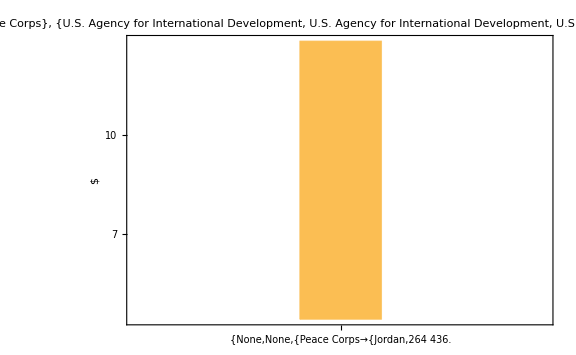

```mathematica
histPlotFin[New314,ToString[textlistMoney314]]
```

### listamountTOTNew[[4]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[4]]],FontColor->Red,Large]
```

Multi-sector

```mathematica
listMoney4=Map[Cases[Values[listamountTOTNewOhne0[[4]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney4//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney4[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→0,3→36,4→0,5→12,6→0,7→1,8→0,9→0,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney41=Style[listMoney4[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New41=listMoney4[[1]]//Values;
```

```mathematica
Length[New41]
```

0

```mathematica
histPlotFin[New41,ToString[textlistMoney41]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney42=Style[listMoney4[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New42=listMoney4[[2]]//Values
```

{}

```mathematica
Length[New42]
```

0

```mathematica
histPlotFin[New42,ToString[textlistMoney42]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney43=Style[listMoney4[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New43=listMoney4[[3]]//Values
```

{{Jordan,9 502.00 $},{Armenia,72 148.00 $},{Ethiopia,8 036.00 $},{Georgia,142 242.00 $},{Uganda,58 037.00 $},{Guatemala,56 668.00 $},{Mexico,67 006.00 $},{Peru,111 240.00 $},{Albania,26 863.00 $},{Benin,54 727.00 $},{Cambodia,73 000.00 $},{Colombia,52 714.00 $},{Fiji,85 413.00 $},{Ghana,79 719.00 $},{Guyana,42 596.00 $},{Jamaica,7 548.00 $},{Kosovo,35 533.00 $},{Kyrgyzstan,46 690.00 $},{Macedonia,22 752.00 $},{Madagascar,38 523.00 $},{Malawi,28 455.00 $},{Moldova,81 544.00 $},{Mongolia,1 735.00 $},{Morocco,48 049.00 $},{Mozambique,8 424.00 $},{Nepal,18 128.00 $},{Nicaragua,40 593.00 $},{Philippines,40 896.00 $},{Rwanda,142 861.00 $},{Samoa,8 786.00 $},{Senegal,14 594.00 $},{Tanzania,38 991.00 $},{Tonga,51 542.00 $},{Ukraine,205 605.00 $},{Vanuatu,141 436.00 $},{Zambia,184 442.00 $}}

```mathematica
Length[New43]
```

36

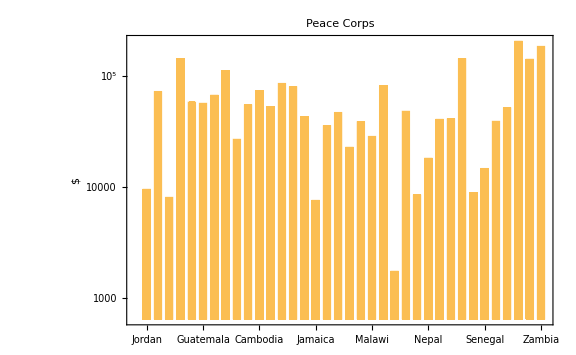

```mathematica
histPlotFin[New43,ToString[textlistMoney43]]
```

#### --- --- --- 4

```mathematica
textlistMoney44=Style[listMoney4[[4]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New44=listMoney4[[4]]//Values
```

{}

```mathematica
Length[New44]
```

0

```mathematica
histPlotFin[New44,ToString[textlistMoney44]]
```

-Graphics-

#### --- --- --- 5

```mathematica
textlistMoney45=Style[listMoney4[[5]][[1]]//Keys,FontColor->Red]
```

U.S. Department of State

```mathematica
New45=listMoney4[[5]]//Values
```

{{Georgia,8 998.75 $},{Kenya,1.28019973e6 $},{Honduras,524 711.36 $},{Peru,88 457.60 $},{Afghanistan,121 228.80 $},{Barbados,189 325.48 $},{Benin,23 966.32 $},{Colombia,6.30340742e6 $},{Ghana,81 434.76 $},{Haiti,48 950.00 $},{Moldova,4 500.00 $},{Morocco,56 912.23 $}}

```mathematica
Length[New45]
```

12

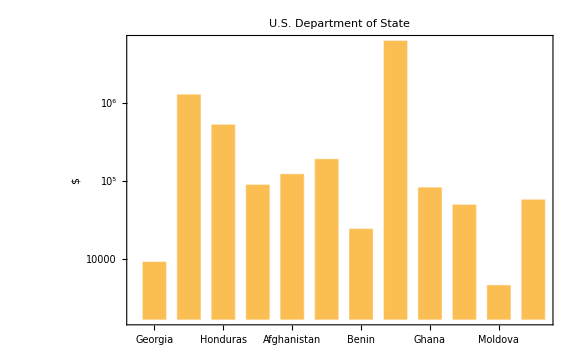

```mathematica
histPlotFin[New45,ToString[textlistMoney45]]
```

#### --- --- --- 6

```mathematica
textlistMoney46=Style[listMoney4[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New46=listMoney4[[6]]//Values
```

{}

```mathematica
Length[New46]
```

0

```mathematica
histPlotFin[New46,ToString[textlistMoney46]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney47=Style[listMoney4[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New47=listMoney4[[7]]//Values
```

{{Nicaragua,151 448.00 $}}

```mathematica
Length[New47]
```

1

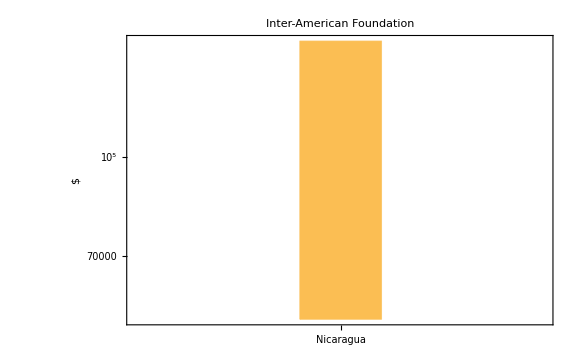

```mathematica
histPlotFin[New47,ToString[textlistMoney47]]
```

#### --- --- --- 8

```mathematica
textlistMoney48=Style[listMoney4[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New48=listMoney4[[8]]//Values
```

{}

```mathematica
Length[New48]
```

0

```mathematica
histPlotFin[New48,ToString[textlistMoney48]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney49=Style[listMoney4[[9]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New49=listMoney4[[9]]//Values
```

{}

```mathematica
Length[New49]
```

0

```mathematica
histPlotFin[New49,ToString[textlistMoney49]]
```

-Graphics-

#### --- --- --- 10

```mathematica
textlistMoney410=Style[listMoney4[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New410=listMoney4[[10]]//Values
```

{}

```mathematica
Length[New410]
```

0

```mathematica
histPlotFin[New410,ToString[textlistMoney410]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney411=Style[listMoney4[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New411=listMoney4[[11]]//Values
```

{}

```mathematica
Length[New411]
```

0

```mathematica
histPlotFin[New411,ToString[textlistMoney411]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney412=Style[listMoney4[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New412=listMoney4[[12]]//Values
```

{}

```mathematica
Length[New412]
```

0

```mathematica
histPlotFin[New412,ToString[textlistMoney412]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney413=Style[listMoney4[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation},{},{},{},{},{}}

```mathematica
New413=listMoney4[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument {{},{},«8»,{},{}}⟦13⟧ is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Jordan,9 502.00 $},Peace Corps→{Armenia,72 148.00 $},Peace Corps→{Ethiopia,8 036.00 $},Peace Corps→{Georgia,142 242.00 $},Peace Corps→{Uganda,58 037.00 $},Peace Corps→{Guatemala,56 668.00 $},Peace Corps→{Mexico,67 006.00 $},Peace Corps→{Peru,111 240.00 $},Peace Corps→{Albania,26 863.00 $},Peace Corps→{Benin,54 727.00 $},Peace Corps→{Cambodia,73 000.00 $},Peace Corps→{Colombia,52 714.00 $},Peace Corps→{Fiji,85 413.00 $},Peace Corps→{Ghana,79 719.00 $},Peace Corps→{Guyana,42 596.00 $},Peace Corps→{Jamaica,7 548.00 $},Peace Corps→{Kosovo,35 533.00 $},Peace Corps→{Kyrgyzstan,46 690.00 $},Peace Corps→{Macedonia,22 752.00 $},Peace Corps→{Madagascar,38 523.00 $},Peace Corps→{Malawi,28 455.00 $},Peace Corps→{Moldova,81 544.00 $},Peace Corps→{Mongolia,1 735.00 $},Peace Corps→{Morocco,48 049.00 $},Peace Corps→{Mozambique,8 424.00 $},Peace Corps→{Nepal,18 128.00 $},Peace Corps→{Nicaragua,40 593.00 $},Peace Corps→{Philippines,40 896.00 $},Peace Corps→{Rwanda,142 861.00 $},Peace Corps→{Samoa,8 786.00 $},Peace Corps→{Senegal,14 594.00 $},Peace Corps→{Tanzania,38 991.00 $},Peace Corps→{Tonga,51 542.00 $},Peace Corps→{Ukraine,205 605.00 $},Peace Corps→{Vanuatu,141 436.00 $},Peace Corps→{Zambia,184 442.00 $}},{},{U.S. Department of State→{Georgia,8 998.75 $},U.S. Department of State→{Kenya,1.28019973e6 $},U.S. Department of State→{Honduras,524 711.36 $},U.S. Department of State→{Peru,88 457.60 $},U.S. Department of State→{Afghanistan,121 228.80 $},U.S. Department of State→{Barbados,189 325.48 $},U.S. Department of State→{Benin,23 966.32 $},U.S. Department of State→{Colombia,6.30340742e6 $},U.S. Department of State→{Ghana,81 434.76 $},U.S. Department of State→{Haiti,48 950.00 $},U.S. Department of State→{Moldova,4 500.00 $},U.S. Department of State→{Morocco,56 912.23 $}},{},{Inter-American Foundation→{Nicaragua,151 448.00 $}},{},{},{},{},{}}⟦13⟧]

```mathematica
Length[New413]
```

1

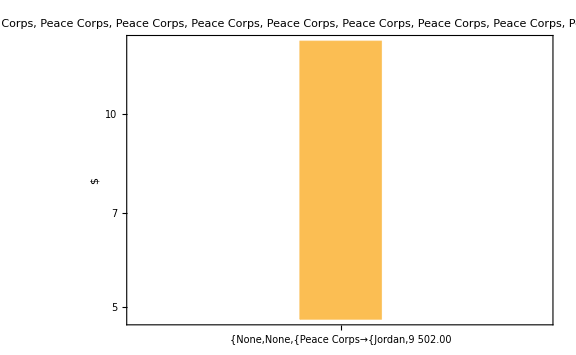

```mathematica
histPlotFin[New413,ToString[textlistMoney413]]
```

#### --- --- --- 14

```mathematica
textlistMoney414=Style[listMoney4[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation},{},{},{},{},{}}

```mathematica
New414=listMoney4[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument {{},{},«8»,{},{}}⟦14⟧ is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Jordan,9 502.00 $},Peace Corps→{Armenia,72 148.00 $},Peace Corps→{Ethiopia,8 036.00 $},Peace Corps→{Georgia,142 242.00 $},Peace Corps→{Uganda,58 037.00 $},Peace Corps→{Guatemala,56 668.00 $},Peace Corps→{Mexico,67 006.00 $},Peace Corps→{Peru,111 240.00 $},Peace Corps→{Albania,26 863.00 $},Peace Corps→{Benin,54 727.00 $},Peace Corps→{Cambodia,73 000.00 $},Peace Corps→{Colombia,52 714.00 $},Peace Corps→{Fiji,85 413.00 $},Peace Corps→{Ghana,79 719.00 $},Peace Corps→{Guyana,42 596.00 $},Peace Corps→{Jamaica,7 548.00 $},Peace Corps→{Kosovo,35 533.00 $},Peace Corps→{Kyrgyzstan,46 690.00 $},Peace Corps→{Macedonia,22 752.00 $},Peace Corps→{Madagascar,38 523.00 $},Peace Corps→{Malawi,28 455.00 $},Peace Corps→{Moldova,81 544.00 $},Peace Corps→{Mongolia,1 735.00 $},Peace Corps→{Morocco,48 049.00 $},Peace Corps→{Mozambique,8 424.00 $},Peace Corps→{Nepal,18 128.00 $},Peace Corps→{Nicaragua,40 593.00 $},Peace Corps→{Philippines,40 896.00 $},Peace Corps→{Rwanda,142 861.00 $},Peace Corps→{Samoa,8 786.00 $},Peace Corps→{Senegal,14 594.00 $},Peace Corps→{Tanzania,38 991.00 $},Peace Corps→{Tonga,51 542.00 $},Peace Corps→{Ukraine,205 605.00 $},Peace Corps→{Vanuatu,141 436.00 $},Peace Corps→{Zambia,184 442.00 $}},{},{U.S. Department of State→{Georgia,8 998.75 $},U.S. Department of State→{Kenya,1.28019973e6 $},U.S. Department of State→{Honduras,524 711.36 $},U.S. Department of State→{Peru,88 457.60 $},U.S. Department of State→{Afghanistan,121 228.80 $},U.S. Department of State→{Barbados,189 325.48 $},U.S. Department of State→{Benin,23 966.32 $},U.S. Department of State→{Colombia,6.30340742e6 $},U.S. Department of State→{Ghana,81 434.76 $},U.S. Department of State→{Haiti,48 950.00 $},U.S. Department of State→{Moldova,4 500.00 $},U.S. Department of State→{Morocco,56 912.23 $}},{},{Inter-American Foundation→{Nicaragua,151 448.00 $}},{},{},{},{},{}}⟦14⟧]

```mathematica
Length[New414]
```

1

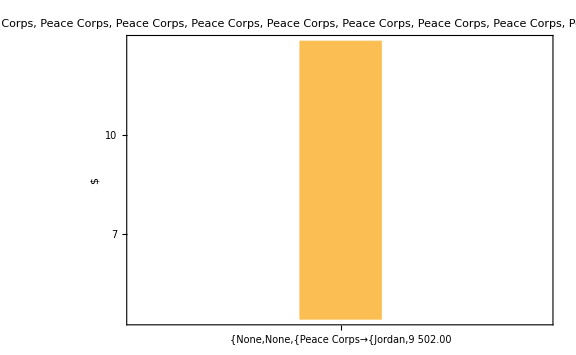

```mathematica
histPlotFin[New414,ToString[textlistMoney414]]
```

### listamountTOTNew[[5]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[5]]],FontColor->Red,Large]
```

Education and Social Services

```mathematica
listMoney5=Map[Cases[Values[listamountTOTNewOhne0[[5]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney5//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney5[[#]]]&,Range[Length[aGENCY]]]
```

{1→1,2→0,3→50,4→54,5→0,6→0,7→12,8→0,9→2,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney51=Style[listMoney5[[1]][[1]]//Keys,FontColor->Red]
```

Overseas Private Investment Corporation

```mathematica
New51=listMoney5[[1]]//Values;
```

```mathematica
Length[New51]
```

1

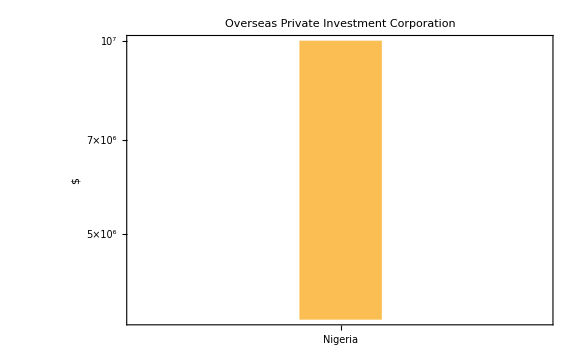

```mathematica
histPlotFin[New51,ToString[textlistMoney51]]
```

#### --- --- --- 2

```mathematica
textlistMoney52=Style[listMoney5[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New52=listMoney5[[2]]//Values
```

{}

```mathematica
Length[New52]
```

0

```mathematica
histPlotFin[New52,ToString[textlistMoney52]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney53=Style[listMoney5[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New53=listMoney5[[3]]//Values
```

{{Jordan,2.00 $},{Armenia,1.340376e6 $},{China,3.157632e6 $},{Ethiopia,2.858948e6 $},{Georgia,1.931089e6 $},{Namibia,2.328893e6 $},{Uganda,1.731059e6 $},{Liberia,2.82036e6 $},{Ecuador,2.683619e6 $},{Guatemala,877 457.00 $},{Mexico,387 907.00 $},{Peru,1.165982e6 $},{Albania,842 103.00 $},{Benin,924 940.00 $},{Botswana,597 372.00 $},{Cambodia,1.181526e6 $},{Cameroon,1.401563e6 $},{Colombia,2.168481e6 $},{Comoros,877 789.00 $},{Fiji,1.061636e6 $},{Ghana,1.192705e6 $},{Guinea,1.038736e6 $},{Guyana,1.310358e6 $},{Indonesia,2.676273e6 $},{Jamaica,1.148976e6 $},{Kosovo,1.119949e6 $},{Kyrgyzstan,1.104273e6 $},{Lesotho,1.721807e6 $},{Macedonia,1.236795e6 $},{Madagascar,1.172262e6 $},{Malawi,1.36633e6 $},{Mali,280 818.00 $},{Moldova,514 553.00 $},{Mongolia,2.417666e6 $},{Morocco,4.0406e6 $},{Mozambique,4.098759e6 $},{Nicaragua,685 925.00 $},{Panama,1.243498e6 $},{Philippines,2.72206e6 $},{Rwanda,1.891049e6 $},{Samoa,1.018679e6 $},{Senegal,80 832.00 $},{Swaziland,1.333537e6 $},{Tanzania,2.912345e6 $},{Thailand,3.173861e6 $},{Togo,1.005063e6 $},{Tonga,1.046009e6 $},{Ukraine,2.550208e6 $},{Vanuatu,1.421894e6 $},{Zambia,36 403.00 $}}

```mathematica
Length[New53]
```

50

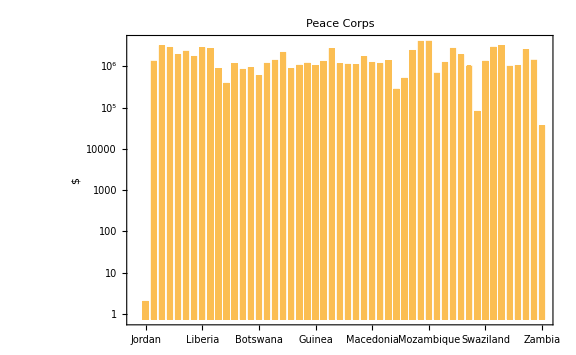

```mathematica
histPlotFin[New53,ToString[textlistMoney53]]
```

#### --- --- --- 4

```mathematica
textlistMoney54=Style[listMoney5[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New54=listMoney5[[4]]//Values
```

{{Jordan,7.194973738999999e7 $},{Armenia,3.93898852e6 $},{China,1.119e6 $},{Ethiopia,4.734255409e7 $},{Georgia,1.01768724e6 $},{Kenya,2.4443627339999996e7 $},{Somalia,3.75845e6 $},{Uganda,2.05085791e7 $},{Bulgaria,490 000.00 $},{Liberia,1.923697347e7 $},{Slovakia,500 000.00 $},{Niger,1.43657505e6 $},{Guatemala,9.08747693e6 $},{Honduras,6.952796e6 $},{Peru,5.14946678e6 $},{Afghanistan,1.0350766056e8 $},{Bangladesh,3.83587982e6 $},{Benin,2.16481861e6 $},{Bolivia,569 719.80 $},{Cambodia,1.18982899e6 $},{Colombia,2.348375973e7 $},{Egypt,3.392424139e7 $},{Ghana,3.272606828e7 $},{Greece,442 000.00 $},{Guyana,53 082.00 $},{Haiti,1.572949086e7 $},{India,4.6512178100000005e6 $},{Indonesia,2.419035336e7 $},{Kosovo,524 128.72 $},{Kyrgyzstan,4.61242125e6 $},{Laos,498 146.00 $},{Lebanon,3.49778138e7 $},{Macedonia,461 438.11 $},{Malawi,1.3417827370000001e7 $},{Mali,2.381214082e7 $},{Mongolia,220 581.34 $},{Morocco,7.98153e6 $},{Mozambique,3.317730634e7 $},{Nepal,2.085005982e7 $},{Nicaragua,3.0390038600000003e6 $},{Nigeria,6.1922921839999996e7 $},{Pakistan,6.927435853e7 $},{Paraguay,900 000.00 $},{Philippines,2.717869355e7 $},{Rwanda,3.1985602229999997e7 $},{Senegal,4.1637711200000006e6 $},{Tajikistan,3.27e6 $},{Tanzania,1.902999051e7 $},{Turkey,995 000.00 $},{Ukraine,232 930.00 $},{Vietnam,5.47577161e6 $},{Yemen,2.49305e6 $},{Zambia,1.371078836e7 $},{Zimbabwe,2.47847e6 $}}

```mathematica
Length[New54]
```

54

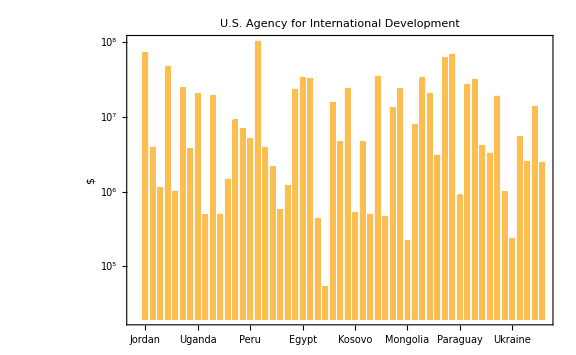

```mathematica
histPlotFin[New54,ToString[textlistMoney54]]
```

#### --- --- --- 5

```mathematica
textlistMoney55=Style[listMoney5[[5]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New55=listMoney5[[5]]//Values
```

{}

```mathematica
Length[New55]
```

0

```mathematica
histPlotFin[New55,ToString[textlistMoney55]]
```

-Graphics-

#### --- --- --- 6

```mathematica
textlistMoney56=Style[listMoney5[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New56=listMoney5[[6]]//Values
```

{}

```mathematica
Length[New56]
```

0

```mathematica
histPlotFin[New56,ToString[textlistMoney56]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney57=Style[listMoney5[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New57=listMoney5[[7]]//Values
```

{{Ecuador,200 000.00 $},{Guatemala,1.03694e6 $},{Honduras,945 275.00 $},{Mexico,195 913.00 $},{Peru,872 975.00 $},{Bolivia,124 375.00 $},{Brazil,211 540.00 $},{Colombia,602 648.16 $},{Haiti,182 500.00 $},{Nicaragua,331 690.00 $},{Paraguay,496 800.00 $},{Uruguay,200 100.00 $}}

```mathematica
Length[New57]
```

12

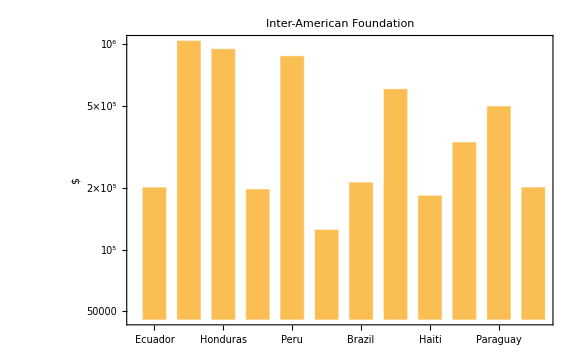

```mathematica
histPlotFin[New57,ToString[textlistMoney57]]
```

#### --- --- --- 8

```mathematica
textlistMoney58=Style[listMoney5[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New58=listMoney5[[8]]//Values
```

{}

```mathematica
Length[New58]
```

0

```mathematica
histPlotFin[New58,ToString[textlistMoney58]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney59=Style[listMoney5[[9]][[1]]//Keys,FontColor->Red]
```

U.S. African Development Foundation

```mathematica
New59=listMoney5[[9]]//Values
```

{{Somalia,1.408048e6 $},{Uganda,276 728.01 $}}

```mathematica
Length[New59]
```

2

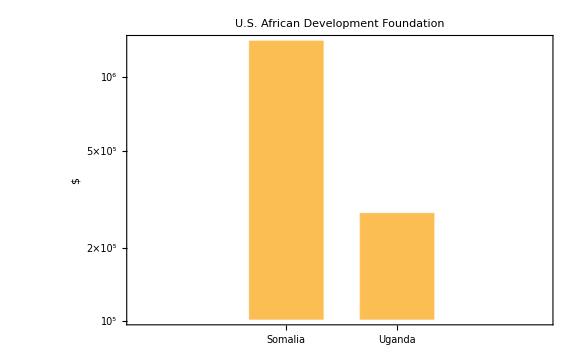

```mathematica
histPlotFin[New59,ToString[textlistMoney59]]
```

#### --- --- --- 10

```mathematica
textlistMoney510=Style[listMoney5[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New510=listMoney5[[10]]//Values
```

{}

```mathematica
Length[New510]
```

0

```mathematica
histPlotFin[New510,ToString[textlistMoney510]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney511=Style[listMoney5[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New511=listMoney5[[11]]//Values
```

{}

```mathematica
Length[New511]
```

0

```mathematica
histPlotFin[New511,ToString[textlistMoney511]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney512=Style[listMoney5[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New512=listMoney5[[12]]//Values
```

{}

```mathematica
Length[New512]
```

0

```mathematica
histPlotFin[New512,ToString[textlistMoney512]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney513=Style[listMoney5[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}} does not exist.

{{Overseas Private Investment Corporation},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{U.S. African Development Foundation,U.S. African Development Foundation},{},{},{}}

```mathematica
New513=listMoney5[[13]]//Values
```

Part::partw: Part 13 of {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}} does not exist.

Values::invrl: The argument {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}}⟦13⟧ is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Nigeria,1.e7 $}},{},{Peace Corps→{Jordan,2.00 $},Peace Corps→{Armenia,1.340376e6 $},Peace Corps→{China,3.157632e6 $},Peace Corps→{Ethiopia,2.858948e6 $},Peace Corps→{Georgia,1.931089e6 $},Peace Corps→{Namibia,2.328893e6 $},Peace Corps→{Uganda,1.731059e6 $},Peace Corps→{Liberia,2.82036e6 $},Peace Corps→{Ecuador,2.683619e6 $},Peace Corps→{Guatemala,877 457.00 $},Peace Corps→{Mexico,387 907.00 $},Peace Corps→{Peru,1.165982e6 $},Peace Corps→{Albania,842 103.00 $},Peace Corps→{Benin,924 940.00 $},Peace Corps→{Botswana,597 372.00 $},Peace Corps→{Cambodia,1.181526e6 $},Peace Corps→{Cameroon,1.401563e6 $},Peace Corps→{Colombia,2.168481e6 $},Peace Corps→{Comoros,877 789.00 $},Peace Corps→{Fiji,1.061636e6 $},Peace Corps→{Ghana,1.192705e6 $},Peace Corps→{Guinea,1.038736e6 $},Peace Corps→{Guyana,1.310358e6 $},Peace Corps→{Indonesia,2.676273e6 $},Peace Corps→{Jamaica,1.148976e6 $},Peace Corps→{Kosovo,1.119949e6 $},Peace Corps→{Kyrgyzstan,1.104273e6 $},Peace Corps→{Lesotho,1.721807e6 $},Peace Corps→{Macedonia,1.236795e6 $},Peace Corps→{Madagascar,1.172262e6 $},Peace Corps→{Malawi,1.36633e6 $},Peace Corps→{Mali,280 818.00 $},Peace Corps→{Moldova,514 553.00 $},Peace Corps→{Mongolia,2.417666e6 $},Peace Corps→{Morocco,4.0406e6 $},Peace Corps→{Mozambique,4.098759e6 $},Peace Corps→{Nicaragua,685 925.00 $},Peace Corps→{Panama,1.243498e6 $},Peace Corps→{Philippines,2.72206e6 $},Peace Corps→{Rwanda,1.891049e6 $},Peace Corps→{Samoa,1.018679e6 $},Peace Corps→{Senegal,80 832.00 $},Peace Corps→{Swaziland,1.333537e6 $},Peace Corps→{Tanzania,2.912345e6 $},Peace Corps→{Thailand,3.173861e6 $},Peace Corps→{Togo,1.005063e6 $},Peace Corps→{Tonga,1.046009e6 $},Peace Corps→{Ukraine,2.550208e6 $},Peace Corps→{Vanuatu,1.421894e6 $},Peace Corps→{Zambia,36 403.00 $}},{U.S. Agency for International Development→{Jordan,7.194973738999999e7 $},U.S. Agency for International Development→{Armenia,3.93898852e6 $},U.S. Agency for International Development→{China,1.119e6 $},U.S. Agency for International Development→{Ethiopia,4.734255409e7 $},U.S. Agency for International Development→{Georgia,1.01768724e6 $},U.S. Agency for International Development→{Kenya,2.4443627339999996e7 $},U.S. Agency for International Development→{Somalia,3.75845e6 $},U.S. Agency for International Development→{Uganda,2.05085791e7 $},U.S. Agency for International Development→{Bulgaria,490 000.00 $},U.S. Agency for International Development→{Liberia,1.923697347e7 $},U.S. Agency for International Development→{Slovakia,500 000.00 $},U.S. Agency for International Development→{Niger,1.43657505e6 $},U.S. Agency for International Development→{Guatemala,9.08747693e6 $},U.S. Agency for International Development→{Honduras,6.952796e6 $},U.S. Agency for International Development→{Peru,5.14946678e6 $},U.S. Agency for International Development→{Afghanistan,1.0350766056e8 $},U.S. Agency for International Development→{Bangladesh,3.83587982e6 $},U.S. Agency for International Development→{Benin,2.16481861e6 $},U.S. Agency for International Development→{Bolivia,569 719.80 $},U.S. Agency for International Development→{Cambodia,1.18982899e6 $},U.S. Agency for International Development→{Colombia,2.348375973e7 $},U.S. Agency for International Development→{Egypt,3.392424139e7 $},U.S. Agency for International Development→{Ghana,3.272606828e7 $},U.S. Agency for International Development→{Greece,442 000.00 $},U.S. Agency for International Development→{Guyana,53 082.00 $},U.S. Agency for International Development→{Haiti,1.572949086e7 $},U.S. Agency for International Development→{India,4.6512178100000005e6 $},U.S. Agency for International Development→{Indonesia,2.419035336e7 $},U.S. Agency for International Development→{Kosovo,524 128.72 $},U.S. Agency for International Development→{Kyrgyzstan,4.61242125e6 $},U.S. Agency for International Development→{Laos,498 146.00 $},U.S. Agency for International Development→{Lebanon,3.49778138e7 $},U.S. Agency for International Development→{Macedonia,461 438.11 $},U.S. Agency for International Development→{Malawi,1.3417827370000001e7 $},U.S. Agency for International Development→{Mali,2.381214082e7 $},U.S. Agency for International Development→{Mongolia,220 581.34 $},U.S. Agency for International Development→{Morocco,7.98153e6 $},U.S. Agency for International Development→{Mozambique,3.317730634e7 $},U.S. Agency for International Development→{Nepal,2.085005982e7 $},U.S. Agency for International Development→{Nicaragua,3.0390038600000003e6 $},U.S. Agency for International Development→{Nigeria,6.1922921839999996e7 $},U.S. Agency for International Development→{Pakistan,6.927435853e7 $},U.S. Agency for International Development→{Paraguay,900 000.00 $},U.S. Agency for International Development→{Philippines,2.717869355e7 $},U.S. Agency for International Development→{Rwanda,3.1985602229999997e7 $},U.S. Agency for International Development→{Senegal,4.1637711200000006e6 $},U.S. Agency for International Development→{Tajikistan,3.27e6 $},U.S. Agency for International Development→{Tanzania,1.902999051e7 $},U.S. Agency for International Development→{Turkey,995 000.00 $},U.S. Agency for International Development→{Ukraine,232 930.00 $},U.S. Agency for International Development→{Vietnam,5.47577161e6 $},U.S. Agency for International Development→{Yemen,2.49305e6 $},U.S. Agency for International Development→{Zambia,1.371078836e7 $},U.S. Agency for International Development→{Zimbabwe,2.47847e6 $}},{},{},{Inter-American Foundation→{Ecuador,200 000.00 $},Inter-American Foundation→{Guatemala,1.03694e6 $},Inter-American Foundation→{Honduras,945 275.00 $},Inter-American Foundation→{Mexico,195 913.00 $},Inter-American Foundation→{Peru,872 975.00 $},Inter-American Foundation→{Bolivia,124 375.00 $},Inter-American Foundation→{Brazil,211 540.00 $},Inter-American Foundation→{Colombia,602 648.16 $},Inter-American Foundation→{Haiti,182 500.00 $},Inter-American Foundation→{Nicaragua,331 690.00 $},Inter-American Foundation→{Paraguay,496 800.00 $},Inter-American Foundation→{Uruguay,200 100.00 $}},{},{U.S. African Development Foundation→{Somalia,1.408048e6 $},U.S. African Development Foundation→{Uganda,276 728.01 $}},{},{},{}}⟦13⟧]

```mathematica
Length[New513]
```

1

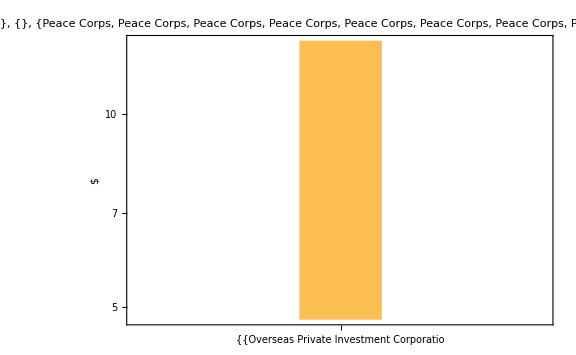

```mathematica
histPlotFin[New513,ToString[textlistMoney513]]
```

#### --- --- --- 14

```mathematica
textlistMoney514=Style[listMoney5[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}} does not exist.

{{Overseas Private Investment Corporation},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{U.S. African Development Foundation,U.S. African Development Foundation},{},{},{}}

```mathematica
New514=listMoney5[[14]]//Values
```

Part::partw: Part 14 of {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}} does not exist.

Values::invrl: The argument {{Overseas Private Investment Corporation→{Nigeria,1.e7}},{},«8»,{},{}}⟦14⟧ is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Nigeria,1.e7 $}},{},{Peace Corps→{Jordan,2.00 $},Peace Corps→{Armenia,1.340376e6 $},Peace Corps→{China,3.157632e6 $},Peace Corps→{Ethiopia,2.858948e6 $},Peace Corps→{Georgia,1.931089e6 $},Peace Corps→{Namibia,2.328893e6 $},Peace Corps→{Uganda,1.731059e6 $},Peace Corps→{Liberia,2.82036e6 $},Peace Corps→{Ecuador,2.683619e6 $},Peace Corps→{Guatemala,877 457.00 $},Peace Corps→{Mexico,387 907.00 $},Peace Corps→{Peru,1.165982e6 $},Peace Corps→{Albania,842 103.00 $},Peace Corps→{Benin,924 940.00 $},Peace Corps→{Botswana,597 372.00 $},Peace Corps→{Cambodia,1.181526e6 $},Peace Corps→{Cameroon,1.401563e6 $},Peace Corps→{Colombia,2.168481e6 $},Peace Corps→{Comoros,877 789.00 $},Peace Corps→{Fiji,1.061636e6 $},Peace Corps→{Ghana,1.192705e6 $},Peace Corps→{Guinea,1.038736e6 $},Peace Corps→{Guyana,1.310358e6 $},Peace Corps→{Indonesia,2.676273e6 $},Peace Corps→{Jamaica,1.148976e6 $},Peace Corps→{Kosovo,1.119949e6 $},Peace Corps→{Kyrgyzstan,1.104273e6 $},Peace Corps→{Lesotho,1.721807e6 $},Peace Corps→{Macedonia,1.236795e6 $},Peace Corps→{Madagascar,1.172262e6 $},Peace Corps→{Malawi,1.36633e6 $},Peace Corps→{Mali,280 818.00 $},Peace Corps→{Moldova,514 553.00 $},Peace Corps→{Mongolia,2.417666e6 $},Peace Corps→{Morocco,4.0406e6 $},Peace Corps→{Mozambique,4.098759e6 $},Peace Corps→{Nicaragua,685 925.00 $},Peace Corps→{Panama,1.243498e6 $},Peace Corps→{Philippines,2.72206e6 $},Peace Corps→{Rwanda,1.891049e6 $},Peace Corps→{Samoa,1.018679e6 $},Peace Corps→{Senegal,80 832.00 $},Peace Corps→{Swaziland,1.333537e6 $},Peace Corps→{Tanzania,2.912345e6 $},Peace Corps→{Thailand,3.173861e6 $},Peace Corps→{Togo,1.005063e6 $},Peace Corps→{Tonga,1.046009e6 $},Peace Corps→{Ukraine,2.550208e6 $},Peace Corps→{Vanuatu,1.421894e6 $},Peace Corps→{Zambia,36 403.00 $}},{U.S. Agency for International Development→{Jordan,7.194973738999999e7 $},U.S. Agency for International Development→{Armenia,3.93898852e6 $},U.S. Agency for International Development→{China,1.119e6 $},U.S. Agency for International Development→{Ethiopia,4.734255409e7 $},U.S. Agency for International Development→{Georgia,1.01768724e6 $},U.S. Agency for International Development→{Kenya,2.4443627339999996e7 $},U.S. Agency for International Development→{Somalia,3.75845e6 $},U.S. Agency for International Development→{Uganda,2.05085791e7 $},U.S. Agency for International Development→{Bulgaria,490 000.00 $},U.S. Agency for International Development→{Liberia,1.923697347e7 $},U.S. Agency for International Development→{Slovakia,500 000.00 $},U.S. Agency for International Development→{Niger,1.43657505e6 $},U.S. Agency for International Development→{Guatemala,9.08747693e6 $},U.S. Agency for International Development→{Honduras,6.952796e6 $},U.S. Agency for International Development→{Peru,5.14946678e6 $},U.S. Agency for International Development→{Afghanistan,1.0350766056e8 $},U.S. Agency for International Development→{Bangladesh,3.83587982e6 $},U.S. Agency for International Development→{Benin,2.16481861e6 $},U.S. Agency for International Development→{Bolivia,569 719.80 $},U.S. Agency for International Development→{Cambodia,1.18982899e6 $},U.S. Agency for International Development→{Colombia,2.348375973e7 $},U.S. Agency for International Development→{Egypt,3.392424139e7 $},U.S. Agency for International Development→{Ghana,3.272606828e7 $},U.S. Agency for International Development→{Greece,442 000.00 $},U.S. Agency for International Development→{Guyana,53 082.00 $},U.S. Agency for International Development→{Haiti,1.572949086e7 $},U.S. Agency for International Development→{India,4.6512178100000005e6 $},U.S. Agency for International Development→{Indonesia,2.419035336e7 $},U.S. Agency for International Development→{Kosovo,524 128.72 $},U.S. Agency for International Development→{Kyrgyzstan,4.61242125e6 $},U.S. Agency for International Development→{Laos,498 146.00 $},U.S. Agency for International Development→{Lebanon,3.49778138e7 $},U.S. Agency for International Development→{Macedonia,461 438.11 $},U.S. Agency for International Development→{Malawi,1.3417827370000001e7 $},U.S. Agency for International Development→{Mali,2.381214082e7 $},U.S. Agency for International Development→{Mongolia,220 581.34 $},U.S. Agency for International Development→{Morocco,7.98153e6 $},U.S. Agency for International Development→{Mozambique,3.317730634e7 $},U.S. Agency for International Development→{Nepal,2.085005982e7 $},U.S. Agency for International Development→{Nicaragua,3.0390038600000003e6 $},U.S. Agency for International Development→{Nigeria,6.1922921839999996e7 $},U.S. Agency for International Development→{Pakistan,6.927435853e7 $},U.S. Agency for International Development→{Paraguay,900 000.00 $},U.S. Agency for International Development→{Philippines,2.717869355e7 $},U.S. Agency for International Development→{Rwanda,3.1985602229999997e7 $},U.S. Agency for International Development→{Senegal,4.1637711200000006e6 $},U.S. Agency for International Development→{Tajikistan,3.27e6 $},U.S. Agency for International Development→{Tanzania,1.902999051e7 $},U.S. Agency for International Development→{Turkey,995 000.00 $},U.S. Agency for International Development→{Ukraine,232 930.00 $},U.S. Agency for International Development→{Vietnam,5.47577161e6 $},U.S. Agency for International Development→{Yemen,2.49305e6 $},U.S. Agency for International Development→{Zambia,1.371078836e7 $},U.S. Agency for International Development→{Zimbabwe,2.47847e6 $}},{},{},{Inter-American Foundation→{Ecuador,200 000.00 $},Inter-American Foundation→{Guatemala,1.03694e6 $},Inter-American Foundation→{Honduras,945 275.00 $},Inter-American Foundation→{Mexico,195 913.00 $},Inter-American Foundation→{Peru,872 975.00 $},Inter-American Foundation→{Bolivia,124 375.00 $},Inter-American Foundation→{Brazil,211 540.00 $},Inter-American Foundation→{Colombia,602 648.16 $},Inter-American Foundation→{Haiti,182 500.00 $},Inter-American Foundation→{Nicaragua,331 690.00 $},Inter-American Foundation→{Paraguay,496 800.00 $},Inter-American Foundation→{Uruguay,200 100.00 $}},{},{U.S. African Development Foundation→{Somalia,1.408048e6 $},U.S. African Development Foundation→{Uganda,276 728.01 $}},{},{},{}}⟦14⟧]

```mathematica
Length[New514]
```

1

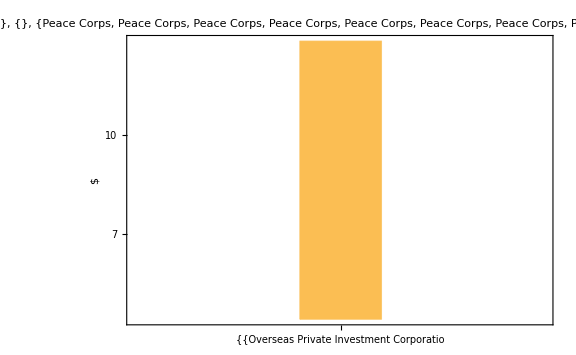

```mathematica
histPlotFin[New514,ToString[textlistMoney514]]
```

### listamountTOTNew[[6]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[6]]],FontColor->Red,Large]
```

Democracy, Human Rights, and Governance

```mathematica
listMoney6=Map[Cases[Values[listamountTOTNewOhne0[[6]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney6//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney6[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→0,3→0,4→63,5→7,6→0,7→5,8→0,9→0,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney61=Style[listMoney6[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New61=listMoney6[[1]]//Values;
```

```mathematica
Length[New61]
```

0

```mathematica
histPlotFin[New61,ToString[textlistMoney61]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney62=Style[listMoney6[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New62=listMoney6[[2]]//Values
```

{}

```mathematica
Length[New62]
```

0

```mathematica
histPlotFin[New62,ToString[textlistMoney62]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney63=Style[listMoney6[[3]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New63=listMoney6[[3]]//Values
```

{}

```mathematica
Length[New63]
```

0

```mathematica
histPlotFin[New63,ToString[textlistMoney63]]
```

-Graphics-

#### --- --- --- 4

```mathematica
textlistMoney64=Style[listMoney6[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New64=listMoney6[[4]]//Values
```

{{Jordan,3.881874604e7 $},{Armenia,2.96539749e6 $},{Ethiopia,90 779.83 $},{Georgia,1.860306473e7 $},{Kenya,1.5294037950000001e7 $},{Libya,1.85e6 $},{Somalia,4.118959476e7 $},{Uganda,5.79448722e6 $},{Liberia,3.555753418e7 $},{Niger,3.7505309299999997e6 $},{Venezuela,3.0936478200000003e6 $},{Cuba,5.72406914e6 $},{Guatemala,4.071416167e7 $},{Honduras,5.720163368e7 $},{Mexico,3.9971313730000004e7 $},{Peru,2.15028687e6 $},{Afghanistan,3.2678577583000004e8 $},{Albania,8.8478326e6 $},{Azerbaijan,5.08904e6 $},{Bangladesh,8.56109296e6 $},{Belarus,5.62399683e6 $},{Burundi,455 811.59 $},{Cambodia,8.95299391e6 $},{Cameroon,35 713.95 $},{Colombia,1.91627563e7 $},{Ghana,7.92521225e6 $},{Guinea,3.46192261e6 $},{Guyana,400 000.00 $},{Haiti,3.081609422e7 $},{Indonesia,8.678984120000001e6 $},{Iraq,1.27e7 $},{Jamaica,6.41354512e6 $},{Kazakhstan,1.44190906e6 $},{Kosovo,8.970067e6 $},{Kyrgyzstan,1.308152176e7 $},{Lebanon,5.62698066e6 $},{Macedonia,6.58583478e6 $},{Malawi,5.387781029999999e6 $},{Mali,5.16379211e6 $},{Moldova,9.063528e6 $},{Mongolia,2.4459135599999996e6 $},{Morocco,1.059017781e7 $},{Mozambique,433 856.88 $},{Nepal,9.73160582e6 $},{Nicaragua,1.09309411e7 $},{Nigeria,1.377515072e7 $},{Pakistan,1.119605003e7 $},{Paraguay,6.379e6 $},{Philippines,6.42041988e6 $},{Rwanda,5.140087e6 $},{Senegal,2.38245074e6 $},{Serbia,4.43094026e6 $},{Sudan,3.36395987e6 $},{Tajikistan,341 381.55 $},{Tanzania,3.e6 $},{Thailand,1.186e6 $},{Turkmenistan,383 000.00 $},{Ukraine,3.4684315980000004e7 $},{Uzbekistan,778 173.12 $},{Vietnam,7.13234365e6 $},{Yemen,3.34493483e6 $},{Zambia,3.08668744e6 $},{Zimbabwe,7.03671824e6 $}}

```mathematica
Length[New64]
```

63

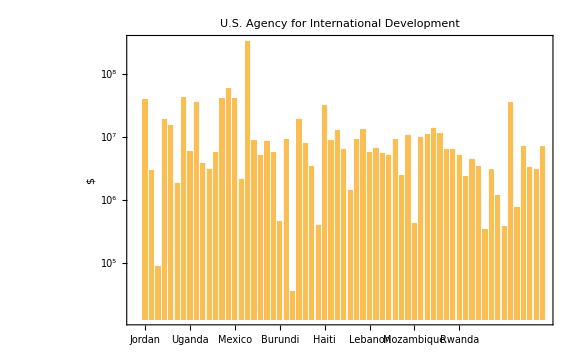

```mathematica
histPlotFin[New64,ToString[textlistMoney64]]
```

#### --- --- --- 5

```mathematica
textlistMoney65=Style[listMoney6[[5]][[1]]//Keys,FontColor->Red]
```

U.S. Department of State

```mathematica
New65=listMoney6[[5]]//Values
```

{{Liberia,1.090549e6 $},{Guatemala,1.55785526e6 $},{Honduras,10 000.00 $},{Mexico,985 784.63 $},{Afghanistan,5.21357149e7 $},{Lebanon,173 792.48 $},{Tunisia,34 708.75 $}}

```mathematica
Length[New65]
```

7

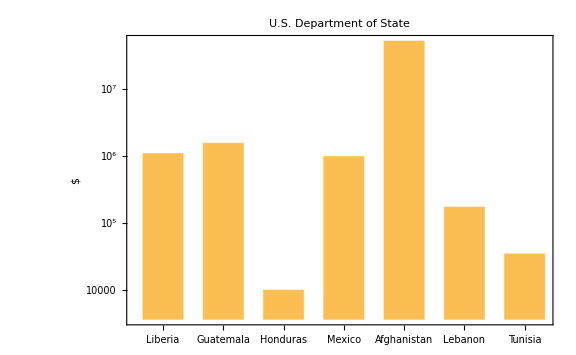

```mathematica
histPlotFin[New65,ToString[textlistMoney65]]
```

#### --- --- --- 6

```mathematica
textlistMoney66=Style[listMoney6[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New66=listMoney6[[6]]//Values
```

{}

```mathematica
Length[New66]
```

0

```mathematica
histPlotFin[New66,ToString[textlistMoney66]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney67=Style[listMoney6[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New67=listMoney6[[7]]//Values
```

{{Mexico,73 936.00 $},{Peru,249 517.00 $},{Bolivia,49 980.00 $},{Brazil,167 830.00 $},{Nicaragua,226 430.00 $}}

```mathematica
Length[New67]
```

5

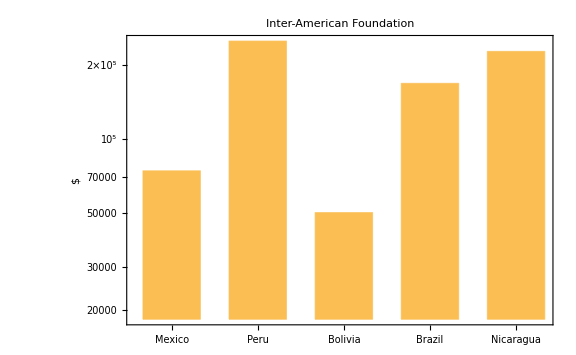

```mathematica
histPlotFin[New67,ToString[textlistMoney67]]
```

#### --- --- --- 8

```mathematica
textlistMoney68=Style[listMoney6[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New68=listMoney6[[8]]//Values
```

{}

```mathematica
Length[New68]
```

0

```mathematica
histPlotFin[New68,ToString[textlistMoney68]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney69=Style[listMoney6[[9]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New69=listMoney6[[9]]//Values
```

{}

```mathematica
Length[New69]
```

0

```mathematica
histPlotFin[New69,ToString[textlistMoney69]]
```

-Graphics-

#### --- --- --- 10

```mathematica
textlistMoney610=Style[listMoney6[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New610=listMoney6[[10]]//Values
```

{}

```mathematica
Length[New610]
```

0

```mathematica
histPlotFin[New610,ToString[textlistMoney610]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney611=Style[listMoney6[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New611=listMoney6[[11]]//Values
```

{}

```mathematica
Length[New611]
```

0

```mathematica
histPlotFin[New611,ToString[textlistMoney611]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney612=Style[listMoney6[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New612=listMoney6[[12]]//Values
```

{}

```mathematica
Length[New612]
```

0

```mathematica
histPlotFin[New612,ToString[textlistMoney612]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney613=Style[listMoney6[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{},{},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{},{},{},{}}

```mathematica
New613=listMoney6[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{},{U.S. Agency for International Development→{Jordan,3.881874604e7 $},U.S. Agency for International Development→{Armenia,2.96539749e6 $},U.S. Agency for International Development→{Ethiopia,90 779.83 $},U.S. Agency for International Development→{Georgia,1.860306473e7 $},U.S. Agency for International Development→{Kenya,1.5294037950000001e7 $},U.S. Agency for International Development→{Libya,1.85e6 $},U.S. Agency for International Development→{Somalia,4.118959476e7 $},U.S. Agency for International Development→{Uganda,5.79448722e6 $},U.S. Agency for International Development→{Liberia,3.555753418e7 $},U.S. Agency for International Development→{Niger,3.7505309299999997e6 $},U.S. Agency for International Development→{Venezuela,3.0936478200000003e6 $},U.S. Agency for International Development→{Cuba,5.72406914e6 $},U.S. Agency for International Development→{Guatemala,4.071416167e7 $},U.S. Agency for International Development→{Honduras,5.720163368e7 $},U.S. Agency for International Development→{Mexico,3.9971313730000004e7 $},U.S. Agency for International Development→{Peru,2.15028687e6 $},U.S. Agency for International Development→{Afghanistan,3.2678577583000004e8 $},U.S. Agency for International Development→{Albania,8.8478326e6 $},U.S. Agency for International Development→{Azerbaijan,5.08904e6 $},U.S. Agency for International Development→{Bangladesh,8.56109296e6 $},U.S. Agency for International Development→{Belarus,5.62399683e6 $},U.S. Agency for International Development→{Burundi,455 811.59 $},U.S. Agency for International Development→{Cambodia,8.95299391e6 $},U.S. Agency for International Development→{Cameroon,35 713.95 $},U.S. Agency for International Development→{Colombia,1.91627563e7 $},U.S. Agency for International Development→{Ghana,7.92521225e6 $},U.S. Agency for International Development→{Guinea,3.46192261e6 $},U.S. Agency for International Development→{Guyana,400 000.00 $},U.S. Agency for International Development→{Haiti,3.081609422e7 $},U.S. Agency for International Development→{Indonesia,8.678984120000001e6 $},U.S. Agency for International Development→{Iraq,1.27e7 $},U.S. Agency for International Development→{Jamaica,6.41354512e6 $},U.S. Agency for International Development→{Kazakhstan,1.44190906e6 $},U.S. Agency for International Development→{Kosovo,8.970067e6 $},U.S. Agency for International Development→{Kyrgyzstan,1.308152176e7 $},U.S. Agency for International Development→{Lebanon,5.62698066e6 $},U.S. Agency for International Development→{Macedonia,6.58583478e6 $},U.S. Agency for International Development→{Malawi,5.387781029999999e6 $},U.S. Agency for International Development→{Mali,5.16379211e6 $},U.S. Agency for International Development→{Moldova,9.063528e6 $},U.S. Agency for International Development→{Mongolia,2.4459135599999996e6 $},U.S. Agency for International Development→{Morocco,1.059017781e7 $},U.S. Agency for International Development→{Mozambique,433 856.88 $},U.S. Agency for International Development→{Nepal,9.73160582e6 $},U.S. Agency for International Development→{Nicaragua,1.09309411e7 $},U.S. Agency for International Development→{Nigeria,1.377515072e7 $},U.S. Agency for International Development→{Pakistan,1.119605003e7 $},U.S. Agency for International Development→{Paraguay,6.379e6 $},U.S. Agency for International Development→{Philippines,6.42041988e6 $},U.S. Agency for International Development→{Rwanda,5.140087e6 $},U.S. Agency for International Development→{Senegal,2.38245074e6 $},U.S. Agency for International Development→{Serbia,4.43094026e6 $},U.S. Agency for International Development→{Sudan,3.36395987e6 $},U.S. Agency for International Development→{Tajikistan,341 381.55 $},U.S. Agency for International Development→{Tanzania,3.e6 $},U.S. Agency for International Development→{Thailand,1.186e6 $},U.S. Agency for International Development→{Turkmenistan,383 000.00 $},U.S. Agency for International Development→{Ukraine,3.4684315980000004e7 $},U.S. Agency for International Development→{Uzbekistan,778 173.12 $},U.S. Agency for International Development→{Vietnam,7.13234365e6 $},U.S. Agency for International Development→{Yemen,3.34493483e6 $},U.S. Agency for International Development→{Zambia,3.08668744e6 $},U.S. Agency for International Development→{Zimbabwe,7.03671824e6 $}},{U.S. Department of State→{Liberia,1.090549e6 $},U.S. Department of State→{Guatemala,1.55785526e6 $},U.S. Department of State→{Honduras,10 000.00 $},U.S. Department of State→{Mexico,985 784.63 $},U.S. Department of State→{Afghanistan,5.21357149e7 $},U.S. Department of State→{Lebanon,173 792.48 $},U.S. Department of State→{Tunisia,34 708.75 $}},{},{Inter-American Foundation→{Mexico,73 936.00 $},Inter-American Foundation→{Peru,249 517.00 $},Inter-American Foundation→{Bolivia,49 980.00 $},Inter-American Foundation→{Brazil,167 830.00 $},Inter-American Foundation→{Nicaragua,226 430.00 $}},{},{},{},{},{}}⟦13⟧]

```mathematica
Length[New613]
```

1

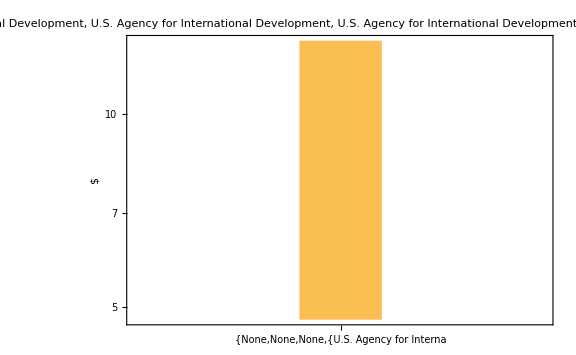

```mathematica
histPlotFin[New613,ToString[textlistMoney613]]
```

#### --- --- --- 14

```mathematica
textlistMoney614=Style[listMoney6[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{},{},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{},{},{},{},{}}

```mathematica
New614=listMoney6[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{},{U.S. Agency for International Development→{Jordan,3.881874604e7 $},U.S. Agency for International Development→{Armenia,2.96539749e6 $},U.S. Agency for International Development→{Ethiopia,90 779.83 $},U.S. Agency for International Development→{Georgia,1.860306473e7 $},U.S. Agency for International Development→{Kenya,1.5294037950000001e7 $},U.S. Agency for International Development→{Libya,1.85e6 $},U.S. Agency for International Development→{Somalia,4.118959476e7 $},U.S. Agency for International Development→{Uganda,5.79448722e6 $},U.S. Agency for International Development→{Liberia,3.555753418e7 $},U.S. Agency for International Development→{Niger,3.7505309299999997e6 $},U.S. Agency for International Development→{Venezuela,3.0936478200000003e6 $},U.S. Agency for International Development→{Cuba,5.72406914e6 $},U.S. Agency for International Development→{Guatemala,4.071416167e7 $},U.S. Agency for International Development→{Honduras,5.720163368e7 $},U.S. Agency for International Development→{Mexico,3.9971313730000004e7 $},U.S. Agency for International Development→{Peru,2.15028687e6 $},U.S. Agency for International Development→{Afghanistan,3.2678577583000004e8 $},U.S. Agency for International Development→{Albania,8.8478326e6 $},U.S. Agency for International Development→{Azerbaijan,5.08904e6 $},U.S. Agency for International Development→{Bangladesh,8.56109296e6 $},U.S. Agency for International Development→{Belarus,5.62399683e6 $},U.S. Agency for International Development→{Burundi,455 811.59 $},U.S. Agency for International Development→{Cambodia,8.95299391e6 $},U.S. Agency for International Development→{Cameroon,35 713.95 $},U.S. Agency for International Development→{Colombia,1.91627563e7 $},U.S. Agency for International Development→{Ghana,7.92521225e6 $},U.S. Agency for International Development→{Guinea,3.46192261e6 $},U.S. Agency for International Development→{Guyana,400 000.00 $},U.S. Agency for International Development→{Haiti,3.081609422e7 $},U.S. Agency for International Development→{Indonesia,8.678984120000001e6 $},U.S. Agency for International Development→{Iraq,1.27e7 $},U.S. Agency for International Development→{Jamaica,6.41354512e6 $},U.S. Agency for International Development→{Kazakhstan,1.44190906e6 $},U.S. Agency for International Development→{Kosovo,8.970067e6 $},U.S. Agency for International Development→{Kyrgyzstan,1.308152176e7 $},U.S. Agency for International Development→{Lebanon,5.62698066e6 $},U.S. Agency for International Development→{Macedonia,6.58583478e6 $},U.S. Agency for International Development→{Malawi,5.387781029999999e6 $},U.S. Agency for International Development→{Mali,5.16379211e6 $},U.S. Agency for International Development→{Moldova,9.063528e6 $},U.S. Agency for International Development→{Mongolia,2.4459135599999996e6 $},U.S. Agency for International Development→{Morocco,1.059017781e7 $},U.S. Agency for International Development→{Mozambique,433 856.88 $},U.S. Agency for International Development→{Nepal,9.73160582e6 $},U.S. Agency for International Development→{Nicaragua,1.09309411e7 $},U.S. Agency for International Development→{Nigeria,1.377515072e7 $},U.S. Agency for International Development→{Pakistan,1.119605003e7 $},U.S. Agency for International Development→{Paraguay,6.379e6 $},U.S. Agency for International Development→{Philippines,6.42041988e6 $},U.S. Agency for International Development→{Rwanda,5.140087e6 $},U.S. Agency for International Development→{Senegal,2.38245074e6 $},U.S. Agency for International Development→{Serbia,4.43094026e6 $},U.S. Agency for International Development→{Sudan,3.36395987e6 $},U.S. Agency for International Development→{Tajikistan,341 381.55 $},U.S. Agency for International Development→{Tanzania,3.e6 $},U.S. Agency for International Development→{Thailand,1.186e6 $},U.S. Agency for International Development→{Turkmenistan,383 000.00 $},U.S. Agency for International Development→{Ukraine,3.4684315980000004e7 $},U.S. Agency for International Development→{Uzbekistan,778 173.12 $},U.S. Agency for International Development→{Vietnam,7.13234365e6 $},U.S. Agency for International Development→{Yemen,3.34493483e6 $},U.S. Agency for International Development→{Zambia,3.08668744e6 $},U.S. Agency for International Development→{Zimbabwe,7.03671824e6 $}},{U.S. Department of State→{Liberia,1.090549e6 $},U.S. Department of State→{Guatemala,1.55785526e6 $},U.S. Department of State→{Honduras,10 000.00 $},U.S. Department of State→{Mexico,985 784.63 $},U.S. Department of State→{Afghanistan,5.21357149e7 $},U.S. Department of State→{Lebanon,173 792.48 $},U.S. Department of State→{Tunisia,34 708.75 $}},{},{Inter-American Foundation→{Mexico,73 936.00 $},Inter-American Foundation→{Peru,249 517.00 $},Inter-American Foundation→{Bolivia,49 980.00 $},Inter-American Foundation→{Brazil,167 830.00 $},Inter-American Foundation→{Nicaragua,226 430.00 $}},{},{},{},{},{}}⟦14⟧]

```mathematica
Length[New614]
```

1

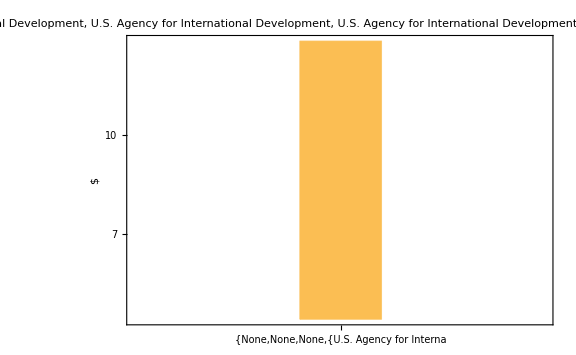

```mathematica
histPlotFin[New614,ToString[textlistMoney614]]
```

### listamountTOTNew[[7]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[7]]],FontColor->Red,Large]
```

Humanitarian Assistance

```mathematica
listMoney7=Map[Cases[Values[listamountTOTNewOhne0[[7]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney7//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney7[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→0,3→0,4→72,5→0,6→0,7→0,8→0,9→0,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney71=Style[listMoney7[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New71=listMoney7[[1]]//Values;
```

```mathematica
Length[New71]
```

0

```mathematica
histPlotFin[New71,ToString[textlistMoney71]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney72=Style[listMoney7[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New72=listMoney7[[2]]//Values
```

{}

```mathematica
Length[New72]
```

0

```mathematica
histPlotFin[New72,ToString[textlistMoney72]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney73=Style[listMoney7[[3]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New73=listMoney7[[3]]//Values
```

{}

```mathematica
Length[New73]
```

0

```mathematica
histPlotFin[New73,ToString[textlistMoney73]]
```

-Graphics-

#### --- --- --- 4

```mathematica
textlistMoney74=Style[listMoney7[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New74=listMoney7[[4]]//Values
```

{{Jordan,129 436.95 $},{Algeria,2.e6 $},{China,1.5e6 $},{Ethiopia,5.0245888216999996e8 $},{Georgia,300 000.00 $},{Kenya,6.073249156e7 $},{Libya,2.14719e6 $},{Somalia,2.3753685821999997e8 $},{Uganda,2.080316533e7 $},{Bulgaria,214 540.00 $},{Chile,975 930.00 $},{Israel,200 000.00 $},{Niger,4.469033401e7 $},{Ecuador,6.27861005e6 $},{Guatemala,1.3813596219999999e7 $},{Honduras,801 459.29 $},{Mexico,3 071.00 $},{Peru,1.514546e6 $},{Afghanistan,4.228889204e7 $},{Bangladesh,8.202984639999999e6 $},{Belize,661.00 $},{Benin,50 000.00 $},{Burundi,1.4595377e7 $},{Cambodia,638 835.28 $},{Cameroon,2.5199158e7 $},{Chad,4.794202999e7 $},{Colombia,6.857157e6 $},{Comoros,218 656.42 $},{Djibouti,128 952.00 $},{Fiji,3.378282e6 $},{Guinea,7.632627070000001e6 $},{Haiti,3.531591993e7 $},{Hungary,5 198.00 $},{Indonesia,1.428529228e7 $},{Iraq,2.5131407260999998e8 $},{Jamaica,261 872.00 $},{Kosovo,50 000.00 $},{Kyrgyzstan,148 257.00 $},{Lesotho,7.941304e6 $},{Macedonia,50 000.00 $},{Madagascar,3.509719617e7 $},{Malawi,8.03462554e7 $},{Malaysia,206 987.00 $},{Mali,4.714153947e7 $},{Mauritania,4.56181602e6 $},{Mongolia,1.299999e6 $},{Mozambique,1.796508255e7 $},{Nepal,3.8079254099999997e6 $},{Nicaragua,258 115.79 $},{Nigeria,1.6942840982e8 $},{Pakistan,5.443168371e7 $},{Palau,234 439.00 $},{Panama,302 702.00 $},{Paraguay,1.25e6 $},{Philippines,1.4727619799999997e6 $},{Rwanda,9.29089104e6 $},{Senegal,1.48149169e6 $},{Sudan,1.8775180154999998e8 $},{Swaziland,5.71975e6 $},{Syria,5.885073040200001e8 $},{Tajikistan,249 351.00 $},{Tanzania,277 156.00 $},{Thailand,845 657.80 $},{Tonga,488 402.00 $},{Turkey,186 435.33 $},{Ukraine,2.1834991e7 $},{Uruguay,50 000.00 $},{Uzbekistan,300 000.00 $},{Vanuatu,2.252897e6 $},{Vietnam,686 689.84 $},{Yemen,2.5597864805e8 $},{Zimbabwe,6.914270215e7 $}}

```mathematica
Length[New74]
```

72

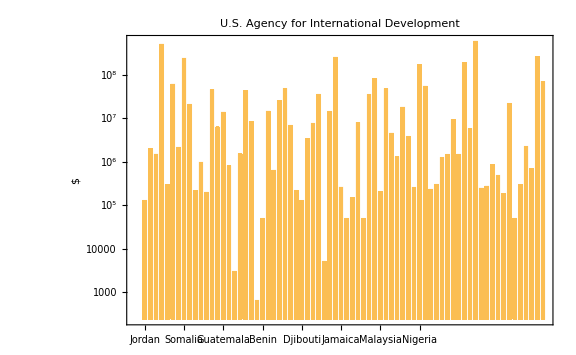

```mathematica
histPlotFin[New74,ToString[textlistMoney74]]
```

#### --- --- --- 5

```mathematica
textlistMoney75=Style[listMoney7[[5]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New75=listMoney7[[5]]//Values
```

{}

```mathematica
Length[New75]
```

0

```mathematica
histPlotFin[New75,ToString[textlistMoney75]]
```

-Graphics-

#### --- --- --- 6

```mathematica
textlistMoney76=Style[listMoney7[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New76=listMoney7[[6]]//Values
```

{}

```mathematica
Length[New76]
```

0

```mathematica
histPlotFin[New76,ToString[textlistMoney76]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney77=Style[listMoney7[[7]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New77=listMoney7[[7]]//Values
```

{}

```mathematica
Length[New77]
```

0

```mathematica
histPlotFin[New77,ToString[textlistMoney77]]
```

-Graphics-

#### --- --- --- 8

```mathematica
textlistMoney78=Style[listMoney7[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New78=listMoney7[[8]]//Values
```

{}

```mathematica
Length[New78]
```

0

```mathematica
histPlotFin[New78,ToString[textlistMoney78]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney79=Style[listMoney7[[9]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New79=listMoney7[[9]]//Values
```

{}

```mathematica
Length[New79]
```

0

```mathematica
histPlotFin[New79,ToString[textlistMoney79]]
```

-Graphics-

#### --- --- --- 10

```mathematica
textlistMoney710=Style[listMoney7[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New710=listMoney7[[10]]//Values
```

{}

```mathematica
Length[New710]
```

0

```mathematica
histPlotFin[New710,ToString[textlistMoney710]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney711=Style[listMoney7[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New711=listMoney7[[11]]//Values
```

{}

```mathematica
Length[New711]
```

0

```mathematica
histPlotFin[New711,ToString[textlistMoney711]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney712=Style[listMoney7[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New712=listMoney7[[12]]//Values
```

{}

```mathematica
Length[New712]
```

0

```mathematica
histPlotFin[New712,ToString[textlistMoney712]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney713=Style[listMoney7[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{},{},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{},{},{},{},{},{}}

```mathematica
New713=listMoney7[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{},{U.S. Agency for International Development→{Jordan,129 436.95 $},U.S. Agency for International Development→{Algeria,2.e6 $},U.S. Agency for International Development→{China,1.5e6 $},U.S. Agency for International Development→{Ethiopia,5.0245888216999996e8 $},U.S. Agency for International Development→{Georgia,300 000.00 $},U.S. Agency for International Development→{Kenya,6.073249156e7 $},U.S. Agency for International Development→{Libya,2.14719e6 $},U.S. Agency for International Development→{Somalia,2.3753685821999997e8 $},U.S. Agency for International Development→{Uganda,2.080316533e7 $},U.S. Agency for International Development→{Bulgaria,214 540.00 $},U.S. Agency for International Development→{Chile,975 930.00 $},U.S. Agency for International Development→{Israel,200 000.00 $},U.S. Agency for International Development→{Niger,4.469033401e7 $},U.S. Agency for International Development→{Ecuador,6.27861005e6 $},U.S. Agency for International Development→{Guatemala,1.3813596219999999e7 $},U.S. Agency for International Development→{Honduras,801 459.29 $},U.S. Agency for International Development→{Mexico,3 071.00 $},U.S. Agency for International Development→{Peru,1.514546e6 $},U.S. Agency for International Development→{Afghanistan,4.228889204e7 $},U.S. Agency for International Development→{Bangladesh,8.202984639999999e6 $},U.S. Agency for International Development→{Belize,661.00 $},U.S. Agency for International Development→{Benin,50 000.00 $},U.S. Agency for International Development→{Burundi,1.4595377e7 $},U.S. Agency for International Development→{Cambodia,638 835.28 $},U.S. Agency for International Development→{Cameroon,2.5199158e7 $},U.S. Agency for International Development→{Chad,4.794202999e7 $},U.S. Agency for International Development→{Colombia,6.857157e6 $},U.S. Agency for International Development→{Comoros,218 656.42 $},U.S. Agency for International Development→{Djibouti,128 952.00 $},U.S. Agency for International Development→{Fiji,3.378282e6 $},U.S. Agency for International Development→{Guinea,7.632627070000001e6 $},U.S. Agency for International Development→{Haiti,3.531591993e7 $},U.S. Agency for International Development→{Hungary,5 198.00 $},U.S. Agency for International Development→{Indonesia,1.428529228e7 $},U.S. Agency for International Development→{Iraq,2.5131407260999998e8 $},U.S. Agency for International Development→{Jamaica,261 872.00 $},U.S. Agency for International Development→{Kosovo,50 000.00 $},U.S. Agency for International Development→{Kyrgyzstan,148 257.00 $},U.S. Agency for International Development→{Lesotho,7.941304e6 $},U.S. Agency for International Development→{Macedonia,50 000.00 $},U.S. Agency for International Development→{Madagascar,3.509719617e7 $},U.S. Agency for International Development→{Malawi,8.03462554e7 $},U.S. Agency for International Development→{Malaysia,206 987.00 $},U.S. Agency for International Development→{Mali,4.714153947e7 $},U.S. Agency for International Development→{Mauritania,4.56181602e6 $},U.S. Agency for International Development→{Mongolia,1.299999e6 $},U.S. Agency for International Development→{Mozambique,1.796508255e7 $},U.S. Agency for International Development→{Nepal,3.8079254099999997e6 $},U.S. Agency for International Development→{Nicaragua,258 115.79 $},U.S. Agency for International Development→{Nigeria,1.6942840982e8 $},U.S. Agency for International Development→{Pakistan,5.443168371e7 $},U.S. Agency for International Development→{Palau,234 439.00 $},U.S. Agency for International Development→{Panama,302 702.00 $},U.S. Agency for International Development→{Paraguay,1.25e6 $},U.S. Agency for International Development→{Philippines,1.4727619799999997e6 $},U.S. Agency for International Development→{Rwanda,9.29089104e6 $},U.S. Agency for International Development→{Senegal,1.48149169e6 $},U.S. Agency for International Development→{Sudan,1.8775180154999998e8 $},U.S. Agency for International Development→{Swaziland,5.71975e6 $},U.S. Agency for International Development→{Syria,5.885073040200001e8 $},U.S. Agency for International Development→{Tajikistan,249 351.00 $},U.S. Agency for International Development→{Tanzania,277 156.00 $},U.S. Agency for International Development→{Thailand,845 657.80 $},U.S. Agency for International Development→{Tonga,488 402.00 $},U.S. Agency for International Development→{Turkey,186 435.33 $},U.S. Agency for International Development→{Ukraine,2.1834991e7 $},U.S. Agency for International Development→{Uruguay,50 000.00 $},U.S. Agency for International Development→{Uzbekistan,300 000.00 $},U.S. Agency for International Development→{Vanuatu,2.252897e6 $},U.S. Agency for International Development→{Vietnam,686 689.84 $},U.S. Agency for International Development→{Yemen,2.5597864805e8 $},U.S. Agency for International Development→{Zimbabwe,6.914270215e7 $}},{},{},{},{},{},{},{},{}}⟦13⟧]

```mathematica
Length[New713]
```

1

```mathematica
histPlotFin[New713,ToString[textlistMoney713]]
```

-Graphics-

#### --- --- --- 14

```mathematica
textlistMoney714=Style[listMoney7[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{},{},{},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{},{},{},{},{},{}}

```mathematica
New714=listMoney7[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{},{U.S. Agency for International Development→{Jordan,129 436.95 $},U.S. Agency for International Development→{Algeria,2.e6 $},U.S. Agency for International Development→{China,1.5e6 $},U.S. Agency for International Development→{Ethiopia,5.0245888216999996e8 $},U.S. Agency for International Development→{Georgia,300 000.00 $},U.S. Agency for International Development→{Kenya,6.073249156e7 $},U.S. Agency for International Development→{Libya,2.14719e6 $},U.S. Agency for International Development→{Somalia,2.3753685821999997e8 $},U.S. Agency for International Development→{Uganda,2.080316533e7 $},U.S. Agency for International Development→{Bulgaria,214 540.00 $},U.S. Agency for International Development→{Chile,975 930.00 $},U.S. Agency for International Development→{Israel,200 000.00 $},U.S. Agency for International Development→{Niger,4.469033401e7 $},U.S. Agency for International Development→{Ecuador,6.27861005e6 $},U.S. Agency for International Development→{Guatemala,1.3813596219999999e7 $},U.S. Agency for International Development→{Honduras,801 459.29 $},U.S. Agency for International Development→{Mexico,3 071.00 $},U.S. Agency for International Development→{Peru,1.514546e6 $},U.S. Agency for International Development→{Afghanistan,4.228889204e7 $},U.S. Agency for International Development→{Bangladesh,8.202984639999999e6 $},U.S. Agency for International Development→{Belize,661.00 $},U.S. Agency for International Development→{Benin,50 000.00 $},U.S. Agency for International Development→{Burundi,1.4595377e7 $},U.S. Agency for International Development→{Cambodia,638 835.28 $},U.S. Agency for International Development→{Cameroon,2.5199158e7 $},U.S. Agency for International Development→{Chad,4.794202999e7 $},U.S. Agency for International Development→{Colombia,6.857157e6 $},U.S. Agency for International Development→{Comoros,218 656.42 $},U.S. Agency for International Development→{Djibouti,128 952.00 $},U.S. Agency for International Development→{Fiji,3.378282e6 $},U.S. Agency for International Development→{Guinea,7.632627070000001e6 $},U.S. Agency for International Development→{Haiti,3.531591993e7 $},U.S. Agency for International Development→{Hungary,5 198.00 $},U.S. Agency for International Development→{Indonesia,1.428529228e7 $},U.S. Agency for International Development→{Iraq,2.5131407260999998e8 $},U.S. Agency for International Development→{Jamaica,261 872.00 $},U.S. Agency for International Development→{Kosovo,50 000.00 $},U.S. Agency for International Development→{Kyrgyzstan,148 257.00 $},U.S. Agency for International Development→{Lesotho,7.941304e6 $},U.S. Agency for International Development→{Macedonia,50 000.00 $},U.S. Agency for International Development→{Madagascar,3.509719617e7 $},U.S. Agency for International Development→{Malawi,8.03462554e7 $},U.S. Agency for International Development→{Malaysia,206 987.00 $},U.S. Agency for International Development→{Mali,4.714153947e7 $},U.S. Agency for International Development→{Mauritania,4.56181602e6 $},U.S. Agency for International Development→{Mongolia,1.299999e6 $},U.S. Agency for International Development→{Mozambique,1.796508255e7 $},U.S. Agency for International Development→{Nepal,3.8079254099999997e6 $},U.S. Agency for International Development→{Nicaragua,258 115.79 $},U.S. Agency for International Development→{Nigeria,1.6942840982e8 $},U.S. Agency for International Development→{Pakistan,5.443168371e7 $},U.S. Agency for International Development→{Palau,234 439.00 $},U.S. Agency for International Development→{Panama,302 702.00 $},U.S. Agency for International Development→{Paraguay,1.25e6 $},U.S. Agency for International Development→{Philippines,1.4727619799999997e6 $},U.S. Agency for International Development→{Rwanda,9.29089104e6 $},U.S. Agency for International Development→{Senegal,1.48149169e6 $},U.S. Agency for International Development→{Sudan,1.8775180154999998e8 $},U.S. Agency for International Development→{Swaziland,5.71975e6 $},U.S. Agency for International Development→{Syria,5.885073040200001e8 $},U.S. Agency for International Development→{Tajikistan,249 351.00 $},U.S. Agency for International Development→{Tanzania,277 156.00 $},U.S. Agency for International Development→{Thailand,845 657.80 $},U.S. Agency for International Development→{Tonga,488 402.00 $},U.S. Agency for International Development→{Turkey,186 435.33 $},U.S. Agency for International Development→{Ukraine,2.1834991e7 $},U.S. Agency for International Development→{Uruguay,50 000.00 $},U.S. Agency for International Development→{Uzbekistan,300 000.00 $},U.S. Agency for International Development→{Vanuatu,2.252897e6 $},U.S. Agency for International Development→{Vietnam,686 689.84 $},U.S. Agency for International Development→{Yemen,2.5597864805e8 $},U.S. Agency for International Development→{Zimbabwe,6.914270215e7 $}},{},{},{},{},{},{},{},{}}⟦14⟧]

```mathematica
Length[New714]
```

1

```mathematica
histPlotFin[New714,ToString[textlistMoney714]]
```

-Graphics-

### listamountTOTNew[[8]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[8]]],FontColor->Red,Large]
```

Health

```mathematica
listMoney8=Map[Cases[Values[listamountTOTNewOhne0[[8]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney8//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney8[[#]]]&,Range[Length[aGENCY]]]
```

{1→1,2→32,3→39,4→65,5→3,6→0,7→1,8→0,9→0,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney81=Style[listMoney8[[1]][[1]]//Keys,FontColor->Red]
```

Overseas Private Investment Corporation

```mathematica
New81=listMoney8[[1]]//Values;
```

```mathematica
Length[New81]
```

1

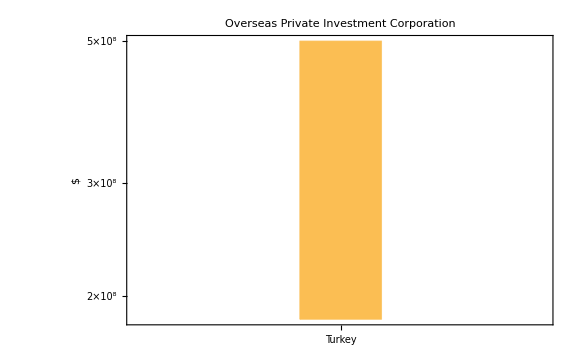

```mathematica
histPlotFin[New81,ToString[textlistMoney81]]
```

#### --- --- --- 2

```mathematica
textlistMoney82=Style[listMoney8[[2]][[1]]//Keys,FontColor->Red]
```

Department of Defense

```mathematica
New82=listMoney8[[2]]//Values
```

{{Angola,1.472527e6 $},{Estonia,220 000.00 $},{Ethiopia,194 506.00 $},{Kenya,2.2057792e7 $},{Uganda,1.1406359e7 $},{Liberia,350 000.00 $},{Niger,370 000.00 $},{Peru,270 000.00 $},{Benin,420 000.00 $},{Burundi,1.26766e6 $},{Cameroon,553 585.00 $},{Chad,420 000.00 $},{Colombia,270 000.00 $},{Comoros,50 000.00 $},{Djibouti,300 000.00 $},{Gabon,110 000.00 $},{Ghana,459 611.00 $},{Guinea,80 000.00 $},{Indonesia,325 000.00 $},{Lesotho,928 598.00 $},{Madagascar,110 000.00 $},{Malawi,1.8e6 $},{Mali,55 000.00 $},{Mozambique,4.487251e6 $},{Nigeria,1.546498e7 $},{Rwanda,1.091497e6 $},{Senegal,300 000.00 $},{Serbia,120 000.00 $},{Swaziland,547 690.00 $},{Tanzania,3.7784235e7 $},{Togo,520 000.00 $},{Zambia,1.338973e7 $}}

```mathematica
Length[New82]
```

32

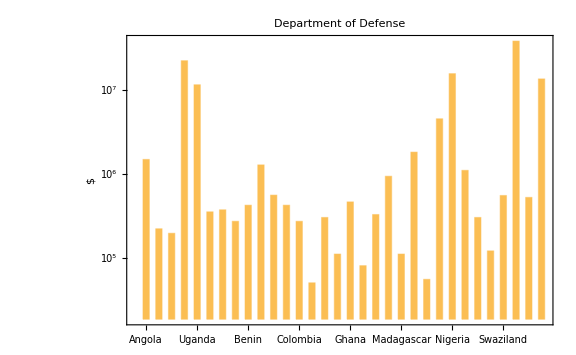

```mathematica
histPlotFin[New82,ToString[textlistMoney82]]
```

#### --- --- --- 3

```mathematica
textlistMoney83=Style[listMoney8[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New83=listMoney8[[3]]//Values
```

{{Ethiopia,1.104311e6 $},{Kenya,614 651.00 $},{Namibia,473 724.00 $},{Uganda,1.618204e6 $},{Liberia,115 100.00 $},{Ecuador,861 559.00 $},{Guatemala,2.641296e6 $},{Peru,2.385265e6 $},{Albania,269 854.00 $},{Belize,1.338067e6 $},{Benin,1.061311e6 $},{Botswana,2.60992e6 $},{Cambodia,986 057.00 $},{Cameroon,1.18378e6 $},{Fiji,670 667.00 $},{Ghana,1.308691e6 $},{Guinea,345 223.00 $},{Guyana,1.079259e6 $},{Kyrgyzstan,357 603.00 $},{Lesotho,612 010.00 $},{Madagascar,770 180.00 $},{Malawi,764 081.00 $},{Mali,460 546.00 $},{Moldova,463 663.00 $},{Mongolia,305 587.00 $},{Mozambique,1.459661e6 $},{Nepal,8 195.00 $},{Nicaragua,786 257.00 $},{Panama,1.082593e6 $},{Paraguay,1.227566e6 $},{Rwanda,867 612.00 $},{Senegal,2.04929e6 $},{Swaziland,764 811.00 $},{Tanzania,1.776064e6 $},{Thailand,3 664.00 $},{Togo,886 628.00 $},{Ukraine,135 214.00 $},{Vanuatu,1.035236e6 $},{Zambia,2.860421e6 $}}

```mathematica
Length[New83]
```

39

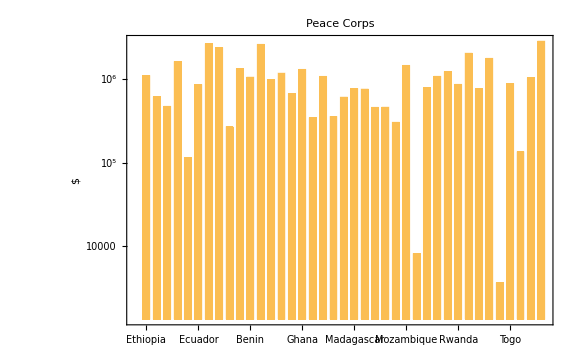

```mathematica
histPlotFin[New83,ToString[textlistMoney83]]
```

#### --- --- --- 4

```mathematica
textlistMoney84=Style[listMoney8[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New84=listMoney8[[4]]//Values
```

{{Jordan,5.28086067e7 $},{Angola,3.969578969e7 $},{Armenia,911 006.79 $},{China,15 397.35 $},{Ethiopia,2.1290656524e8 $},{Kenya,3.0534866723e8 $},{Namibia,1.4976623059999999e7 $},{Somalia,1.4604e6 $},{Uganda,2.145796482e8 $},{Liberia,7.839303824e7 $},{Israel,3.075e6 $},{Niger,1.82896075e6 $},{Guatemala,1.3747226760000002e7 $},{Honduras,1.2675661e6 $},{Mexico,18 271.71 $},{Peru,405 662.79 $},{Afghanistan,5.754225757e7 $},{Azerbaijan,2 059.98 $},{Bangladesh,7.839317756e7 $},{Barbados,4 593.06 $},{Benin,2.0200903369999997e7 $},{Botswana,1.716425637e7 $},{Burundi,3.9731473080000006e7 $},{Cambodia,2.830108201e7 $},{Cameroon,1.2120668120000001e7 $},{Colombia,2 862.06 $},{Djibouti,3.0431385e6 $},{Egypt,1.297176841e7 $},{Ghana,7.309856116000001e7 $},{Guinea,3.623748513e7 $},{Guyana,1.563819e6 $},{Haiti,9.234056999000001e7 $},{India,8.458895911999999e7 $},{Indonesia,5.11314435e7 $},{Jamaica,2.67109683e6 $},{Kyrgyzstan,4.1091400300000003e6 $},{Laos,2.87998925e6 $},{Lebanon,9.41080756e6 $},{Lesotho,4.6419730400000006e7 $},{Lithuania,5 722.66 $},{Madagascar,5.0935409980000004e7 $},{Malawi,1.3735222136999997e8 $},{Mali,6.1624945769999996e7 $},{Mozambique,1.6009699882999998e8 $},{Nepal,4.964566719e7 $},{Nicaragua,1.27268458e6 $},{Nigeria,4.9746282796000004e8 $},{Pakistan,5.9967114940000005e7 $},{Panama,1 728.67 $},{Philippines,3.232279085e7 $},{Poland,6 396.56 $},{Qatar,33 096.68 $},{Rwanda,5.7912575809999995e7 $},{Samoa,433 264.00 $},{Senegal,6.398850336e7 $},{Swaziland,2.96097035e7 $},{Tajikistan,6.26495765e6 $},{Tanzania,1.7237380178e8 $},{Thailand,1.1859426100000003e6 $},{Turkmenistan,150 000.00 $},{Ukraine,2.1589567660000004e7 $},{Uzbekistan,3.54511735e6 $},{Vietnam,1.580021751e7 $},{Zambia,2.0556502476999998e8 $},{Zimbabwe,9.603026676e7 $}}

```mathematica
Length[New84]
```

65

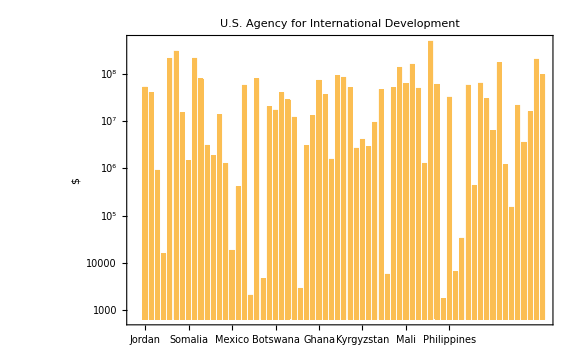

```mathematica
histPlotFin[New84,ToString[textlistMoney84]]
```

#### --- --- --- 5

```mathematica
textlistMoney85=Style[listMoney8[[5]][[1]]//Keys,FontColor->Red]
```

U.S. Department of State

```mathematica
New85=listMoney8[[5]]//Values
```

{{Ethiopia,491 360.00 $},{Mozambique,483 158.55 $},{Tanzania,1.7073810799999998e6 $}}

```mathematica
Length[New85]
```

3

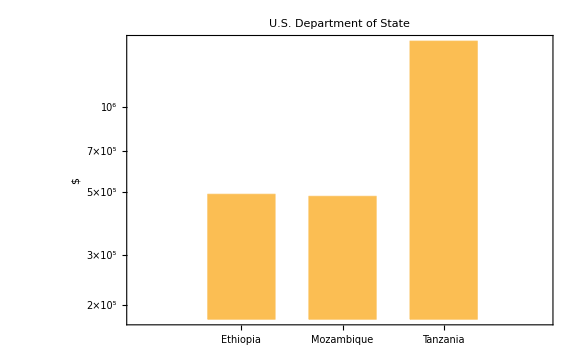

```mathematica
histPlotFin[New85,ToString[textlistMoney85]]
```

#### --- --- --- 6

```mathematica
textlistMoney86=Style[listMoney8[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New86=listMoney8[[6]]//Values
```

{}

```mathematica
Length[New86]
```

0

```mathematica
histPlotFin[New86,ToString[textlistMoney86]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney87=Style[listMoney8[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New87=listMoney8[[7]]//Values
```

{{Haiti,50 000.00 $}}

```mathematica
Length[New87]
```

1

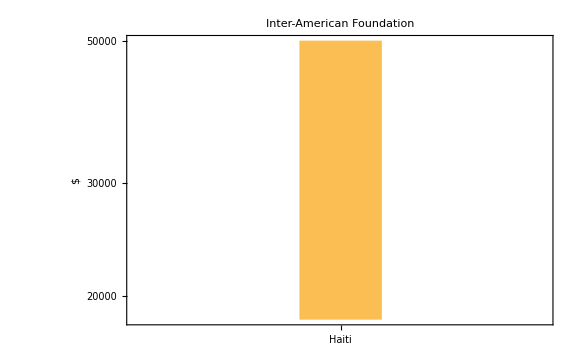

```mathematica
histPlotFin[New87,ToString[textlistMoney87]]
```

#### --- --- --- 8

```mathematica
textlistMoney88=Style[listMoney8[[8]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New88=listMoney8[[8]]//Values
```

{}

```mathematica
Length[New88]
```

0

```mathematica
histPlotFin[New88,ToString[textlistMoney88]]
```

-Graphics-

#### --- --- --- 9

```mathematica
textlistMoney89=Style[listMoney8[[9]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New89=listMoney8[[9]]//Values
```

{}

```mathematica
Length[New89]
```

0

```mathematica
histPlotFin[New89,ToString[textlistMoney89]]
```

-Graphics-

#### --- --- --- 10

```mathematica
textlistMoney810=Style[listMoney8[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New810=listMoney8[[10]]//Values
```

{}

```mathematica
Length[New810]
```

0

```mathematica
histPlotFin[New810,ToString[textlistMoney810]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney811=Style[listMoney8[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New811=listMoney8[[11]]//Values
```

{}

```mathematica
Length[New811]
```

0

```mathematica
histPlotFin[New811,ToString[textlistMoney811]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney812=Style[listMoney8[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New812=listMoney8[[12]]//Values
```

{}

```mathematica
Length[New812]
```

0

```mathematica
histPlotFin[New812,ToString[textlistMoney812]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney813=Style[listMoney8[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}} does not exist.

{{Overseas Private Investment Corporation},{Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation},{},{},{},{},{}}

```mathematica
New813=listMoney8[[13]]//Values
```

Part::partw: Part 13 of {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}} does not exist.

Values::invrl: The argument {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}}⟦13⟧ is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Turkey,5.e8 $}},{Department of Defense→{Angola,1.472527e6 $},Department of Defense→{Estonia,220 000.00 $},Department of Defense→{Ethiopia,194 506.00 $},Department of Defense→{Kenya,2.2057792e7 $},Department of Defense→{Uganda,1.1406359e7 $},Department of Defense→{Liberia,350 000.00 $},Department of Defense→{Niger,370 000.00 $},Department of Defense→{Peru,270 000.00 $},Department of Defense→{Benin,420 000.00 $},Department of Defense→{Burundi,1.26766e6 $},Department of Defense→{Cameroon,553 585.00 $},Department of Defense→{Chad,420 000.00 $},Department of Defense→{Colombia,270 000.00 $},Department of Defense→{Comoros,50 000.00 $},Department of Defense→{Djibouti,300 000.00 $},Department of Defense→{Gabon,110 000.00 $},Department of Defense→{Ghana,459 611.00 $},Department of Defense→{Guinea,80 000.00 $},Department of Defense→{Indonesia,325 000.00 $},Department of Defense→{Lesotho,928 598.00 $},Department of Defense→{Madagascar,110 000.00 $},Department of Defense→{Malawi,1.8e6 $},Department of Defense→{Mali,55 000.00 $},Department of Defense→{Mozambique,4.487251e6 $},Department of Defense→{Nigeria,1.546498e7 $},Department of Defense→{Rwanda,1.091497e6 $},Department of Defense→{Senegal,300 000.00 $},Department of Defense→{Serbia,120 000.00 $},Department of Defense→{Swaziland,547 690.00 $},Department of Defense→{Tanzania,3.7784235e7 $},Department of Defense→{Togo,520 000.00 $},Department of Defense→{Zambia,1.338973e7 $}},{Peace Corps→{Ethiopia,1.104311e6 $},Peace Corps→{Kenya,614 651.00 $},Peace Corps→{Namibia,473 724.00 $},Peace Corps→{Uganda,1.618204e6 $},Peace Corps→{Liberia,115 100.00 $},Peace Corps→{Ecuador,861 559.00 $},Peace Corps→{Guatemala,2.641296e6 $},Peace Corps→{Peru,2.385265e6 $},Peace Corps→{Albania,269 854.00 $},Peace Corps→{Belize,1.338067e6 $},Peace Corps→{Benin,1.061311e6 $},Peace Corps→{Botswana,2.60992e6 $},Peace Corps→{Cambodia,986 057.00 $},Peace Corps→{Cameroon,1.18378e6 $},Peace Corps→{Fiji,670 667.00 $},Peace Corps→{Ghana,1.308691e6 $},Peace Corps→{Guinea,345 223.00 $},Peace Corps→{Guyana,1.079259e6 $},Peace Corps→{Kyrgyzstan,357 603.00 $},Peace Corps→{Lesotho,612 010.00 $},Peace Corps→{Madagascar,770 180.00 $},Peace Corps→{Malawi,764 081.00 $},Peace Corps→{Mali,460 546.00 $},Peace Corps→{Moldova,463 663.00 $},Peace Corps→{Mongolia,305 587.00 $},Peace Corps→{Mozambique,1.459661e6 $},Peace Corps→{Nepal,8 195.00 $},Peace Corps→{Nicaragua,786 257.00 $},Peace Corps→{Panama,1.082593e6 $},Peace Corps→{Paraguay,1.227566e6 $},Peace Corps→{Rwanda,867 612.00 $},Peace Corps→{Senegal,2.04929e6 $},Peace Corps→{Swaziland,764 811.00 $},Peace Corps→{Tanzania,1.776064e6 $},Peace Corps→{Thailand,3 664.00 $},Peace Corps→{Togo,886 628.00 $},Peace Corps→{Ukraine,135 214.00 $},Peace Corps→{Vanuatu,1.035236e6 $},Peace Corps→{Zambia,2.860421e6 $}},{U.S. Agency for International Development→{Jordan,5.28086067e7 $},U.S. Agency for International Development→{Angola,3.969578969e7 $},U.S. Agency for International Development→{Armenia,911 006.79 $},U.S. Agency for International Development→{China,15 397.35 $},U.S. Agency for International Development→{Ethiopia,2.1290656524e8 $},U.S. Agency for International Development→{Kenya,3.0534866723e8 $},U.S. Agency for International Development→{Namibia,1.4976623059999999e7 $},U.S. Agency for International Development→{Somalia,1.4604e6 $},U.S. Agency for International Development→{Uganda,2.145796482e8 $},U.S. Agency for International Development→{Liberia,7.839303824e7 $},U.S. Agency for International Development→{Israel,3.075e6 $},U.S. Agency for International Development→{Niger,1.82896075e6 $},U.S. Agency for International Development→{Guatemala,1.3747226760000002e7 $},U.S. Agency for International Development→{Honduras,1.2675661e6 $},U.S. Agency for International Development→{Mexico,18 271.71 $},U.S. Agency for International Development→{Peru,405 662.79 $},U.S. Agency for International Development→{Afghanistan,5.754225757e7 $},U.S. Agency for International Development→{Azerbaijan,2 059.98 $},U.S. Agency for International Development→{Bangladesh,7.839317756e7 $},U.S. Agency for International Development→{Barbados,4 593.06 $},U.S. Agency for International Development→{Benin,2.0200903369999997e7 $},U.S. Agency for International Development→{Botswana,1.716425637e7 $},U.S. Agency for International Development→{Burundi,3.9731473080000006e7 $},U.S. Agency for International Development→{Cambodia,2.830108201e7 $},U.S. Agency for International Development→{Cameroon,1.2120668120000001e7 $},U.S. Agency for International Development→{Colombia,2 862.06 $},U.S. Agency for International Development→{Djibouti,3.0431385e6 $},U.S. Agency for International Development→{Egypt,1.297176841e7 $},U.S. Agency for International Development→{Ghana,7.309856116000001e7 $},U.S. Agency for International Development→{Guinea,3.623748513e7 $},U.S. Agency for International Development→{Guyana,1.563819e6 $},U.S. Agency for International Development→{Haiti,9.234056999000001e7 $},U.S. Agency for International Development→{India,8.458895911999999e7 $},U.S. Agency for International Development→{Indonesia,5.11314435e7 $},U.S. Agency for International Development→{Jamaica,2.67109683e6 $},U.S. Agency for International Development→{Kyrgyzstan,4.1091400300000003e6 $},U.S. Agency for International Development→{Laos,2.87998925e6 $},U.S. Agency for International Development→{Lebanon,9.41080756e6 $},U.S. Agency for International Development→{Lesotho,4.6419730400000006e7 $},U.S. Agency for International Development→{Lithuania,5 722.66 $},U.S. Agency for International Development→{Madagascar,5.0935409980000004e7 $},U.S. Agency for International Development→{Malawi,1.3735222136999997e8 $},U.S. Agency for International Development→{Mali,6.1624945769999996e7 $},U.S. Agency for International Development→{Mozambique,1.6009699882999998e8 $},U.S. Agency for International Development→{Nepal,4.964566719e7 $},U.S. Agency for International Development→{Nicaragua,1.27268458e6 $},U.S. Agency for International Development→{Nigeria,4.9746282796000004e8 $},U.S. Agency for International Development→{Pakistan,5.9967114940000005e7 $},U.S. Agency for International Development→{Panama,1 728.67 $},U.S. Agency for International Development→{Philippines,3.232279085e7 $},U.S. Agency for International Development→{Poland,6 396.56 $},U.S. Agency for International Development→{Qatar,33 096.68 $},U.S. Agency for International Development→{Rwanda,5.7912575809999995e7 $},U.S. Agency for International Development→{Samoa,433 264.00 $},U.S. Agency for International Development→{Senegal,6.398850336e7 $},U.S. Agency for International Development→{Swaziland,2.96097035e7 $},U.S. Agency for International Development→{Tajikistan,6.26495765e6 $},U.S. Agency for International Development→{Tanzania,1.7237380178e8 $},U.S. Agency for International Development→{Thailand,1.1859426100000003e6 $},U.S. Agency for International Development→{Turkmenistan,150 000.00 $},U.S. Agency for International Development→{Ukraine,2.1589567660000004e7 $},U.S. Agency for International Development→{Uzbekistan,3.54511735e6 $},U.S. Agency for International Development→{Vietnam,1.580021751e7 $},U.S. Agency for International Development→{Zambia,2.0556502476999998e8 $},U.S. Agency for International Development→{Zimbabwe,9.603026676e7 $}},{U.S. Department of State→{Ethiopia,491 360.00 $},U.S. Department of State→{Mozambique,483 158.55 $},U.S. Department of State→{Tanzania,1.7073810799999998e6 $}},{},{Inter-American Foundation→{Haiti,50 000.00 $}},{},{},{},{},{}}⟦13⟧]

```mathematica
Length[New813]
```

1

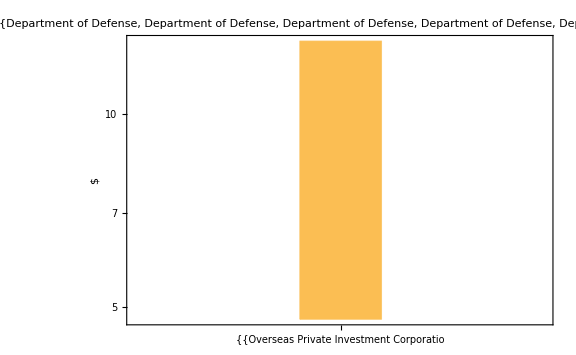

```mathematica
histPlotFin[New813,ToString[textlistMoney813]]
```

#### --- --- --- 14

```mathematica
textlistMoney814=Style[listMoney8[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}} does not exist.

{{Overseas Private Investment Corporation},{Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense,Department of Defense},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{U.S. Department of State,U.S. Department of State,U.S. Department of State},{},{Inter-American Foundation},{},{},{},{},{}}

```mathematica
New814=listMoney8[[14]]//Values
```

Part::partw: Part 14 of {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}} does not exist.

Values::invrl: The argument {{Overseas Private Investment Corporation→{Turkey,5.e8}},«10»,{}}⟦14⟧ is not a valid Association or a list of rules.

Values[{{Overseas Private Investment Corporation→{Turkey,5.e8 $}},{Department of Defense→{Angola,1.472527e6 $},Department of Defense→{Estonia,220 000.00 $},Department of Defense→{Ethiopia,194 506.00 $},Department of Defense→{Kenya,2.2057792e7 $},Department of Defense→{Uganda,1.1406359e7 $},Department of Defense→{Liberia,350 000.00 $},Department of Defense→{Niger,370 000.00 $},Department of Defense→{Peru,270 000.00 $},Department of Defense→{Benin,420 000.00 $},Department of Defense→{Burundi,1.26766e6 $},Department of Defense→{Cameroon,553 585.00 $},Department of Defense→{Chad,420 000.00 $},Department of Defense→{Colombia,270 000.00 $},Department of Defense→{Comoros,50 000.00 $},Department of Defense→{Djibouti,300 000.00 $},Department of Defense→{Gabon,110 000.00 $},Department of Defense→{Ghana,459 611.00 $},Department of Defense→{Guinea,80 000.00 $},Department of Defense→{Indonesia,325 000.00 $},Department of Defense→{Lesotho,928 598.00 $},Department of Defense→{Madagascar,110 000.00 $},Department of Defense→{Malawi,1.8e6 $},Department of Defense→{Mali,55 000.00 $},Department of Defense→{Mozambique,4.487251e6 $},Department of Defense→{Nigeria,1.546498e7 $},Department of Defense→{Rwanda,1.091497e6 $},Department of Defense→{Senegal,300 000.00 $},Department of Defense→{Serbia,120 000.00 $},Department of Defense→{Swaziland,547 690.00 $},Department of Defense→{Tanzania,3.7784235e7 $},Department of Defense→{Togo,520 000.00 $},Department of Defense→{Zambia,1.338973e7 $}},{Peace Corps→{Ethiopia,1.104311e6 $},Peace Corps→{Kenya,614 651.00 $},Peace Corps→{Namibia,473 724.00 $},Peace Corps→{Uganda,1.618204e6 $},Peace Corps→{Liberia,115 100.00 $},Peace Corps→{Ecuador,861 559.00 $},Peace Corps→{Guatemala,2.641296e6 $},Peace Corps→{Peru,2.385265e6 $},Peace Corps→{Albania,269 854.00 $},Peace Corps→{Belize,1.338067e6 $},Peace Corps→{Benin,1.061311e6 $},Peace Corps→{Botswana,2.60992e6 $},Peace Corps→{Cambodia,986 057.00 $},Peace Corps→{Cameroon,1.18378e6 $},Peace Corps→{Fiji,670 667.00 $},Peace Corps→{Ghana,1.308691e6 $},Peace Corps→{Guinea,345 223.00 $},Peace Corps→{Guyana,1.079259e6 $},Peace Corps→{Kyrgyzstan,357 603.00 $},Peace Corps→{Lesotho,612 010.00 $},Peace Corps→{Madagascar,770 180.00 $},Peace Corps→{Malawi,764 081.00 $},Peace Corps→{Mali,460 546.00 $},Peace Corps→{Moldova,463 663.00 $},Peace Corps→{Mongolia,305 587.00 $},Peace Corps→{Mozambique,1.459661e6 $},Peace Corps→{Nepal,8 195.00 $},Peace Corps→{Nicaragua,786 257.00 $},Peace Corps→{Panama,1.082593e6 $},Peace Corps→{Paraguay,1.227566e6 $},Peace Corps→{Rwanda,867 612.00 $},Peace Corps→{Senegal,2.04929e6 $},Peace Corps→{Swaziland,764 811.00 $},Peace Corps→{Tanzania,1.776064e6 $},Peace Corps→{Thailand,3 664.00 $},Peace Corps→{Togo,886 628.00 $},Peace Corps→{Ukraine,135 214.00 $},Peace Corps→{Vanuatu,1.035236e6 $},Peace Corps→{Zambia,2.860421e6 $}},{U.S. Agency for International Development→{Jordan,5.28086067e7 $},U.S. Agency for International Development→{Angola,3.969578969e7 $},U.S. Agency for International Development→{Armenia,911 006.79 $},U.S. Agency for International Development→{China,15 397.35 $},U.S. Agency for International Development→{Ethiopia,2.1290656524e8 $},U.S. Agency for International Development→{Kenya,3.0534866723e8 $},U.S. Agency for International Development→{Namibia,1.4976623059999999e7 $},U.S. Agency for International Development→{Somalia,1.4604e6 $},U.S. Agency for International Development→{Uganda,2.145796482e8 $},U.S. Agency for International Development→{Liberia,7.839303824e7 $},U.S. Agency for International Development→{Israel,3.075e6 $},U.S. Agency for International Development→{Niger,1.82896075e6 $},U.S. Agency for International Development→{Guatemala,1.3747226760000002e7 $},U.S. Agency for International Development→{Honduras,1.2675661e6 $},U.S. Agency for International Development→{Mexico,18 271.71 $},U.S. Agency for International Development→{Peru,405 662.79 $},U.S. Agency for International Development→{Afghanistan,5.754225757e7 $},U.S. Agency for International Development→{Azerbaijan,2 059.98 $},U.S. Agency for International Development→{Bangladesh,7.839317756e7 $},U.S. Agency for International Development→{Barbados,4 593.06 $},U.S. Agency for International Development→{Benin,2.0200903369999997e7 $},U.S. Agency for International Development→{Botswana,1.716425637e7 $},U.S. Agency for International Development→{Burundi,3.9731473080000006e7 $},U.S. Agency for International Development→{Cambodia,2.830108201e7 $},U.S. Agency for International Development→{Cameroon,1.2120668120000001e7 $},U.S. Agency for International Development→{Colombia,2 862.06 $},U.S. Agency for International Development→{Djibouti,3.0431385e6 $},U.S. Agency for International Development→{Egypt,1.297176841e7 $},U.S. Agency for International Development→{Ghana,7.309856116000001e7 $},U.S. Agency for International Development→{Guinea,3.623748513e7 $},U.S. Agency for International Development→{Guyana,1.563819e6 $},U.S. Agency for International Development→{Haiti,9.234056999000001e7 $},U.S. Agency for International Development→{India,8.458895911999999e7 $},U.S. Agency for International Development→{Indonesia,5.11314435e7 $},U.S. Agency for International Development→{Jamaica,2.67109683e6 $},U.S. Agency for International Development→{Kyrgyzstan,4.1091400300000003e6 $},U.S. Agency for International Development→{Laos,2.87998925e6 $},U.S. Agency for International Development→{Lebanon,9.41080756e6 $},U.S. Agency for International Development→{Lesotho,4.6419730400000006e7 $},U.S. Agency for International Development→{Lithuania,5 722.66 $},U.S. Agency for International Development→{Madagascar,5.0935409980000004e7 $},U.S. Agency for International Development→{Malawi,1.3735222136999997e8 $},U.S. Agency for International Development→{Mali,6.1624945769999996e7 $},U.S. Agency for International Development→{Mozambique,1.6009699882999998e8 $},U.S. Agency for International Development→{Nepal,4.964566719e7 $},U.S. Agency for International Development→{Nicaragua,1.27268458e6 $},U.S. Agency for International Development→{Nigeria,4.9746282796000004e8 $},U.S. Agency for International Development→{Pakistan,5.9967114940000005e7 $},U.S. Agency for International Development→{Panama,1 728.67 $},U.S. Agency for International Development→{Philippines,3.232279085e7 $},U.S. Agency for International Development→{Poland,6 396.56 $},U.S. Agency for International Development→{Qatar,33 096.68 $},U.S. Agency for International Development→{Rwanda,5.7912575809999995e7 $},U.S. Agency for International Development→{Samoa,433 264.00 $},U.S. Agency for International Development→{Senegal,6.398850336e7 $},U.S. Agency for International Development→{Swaziland,2.96097035e7 $},U.S. Agency for International Development→{Tajikistan,6.26495765e6 $},U.S. Agency for International Development→{Tanzania,1.7237380178e8 $},U.S. Agency for International Development→{Thailand,1.1859426100000003e6 $},U.S. Agency for International Development→{Turkmenistan,150 000.00 $},U.S. Agency for International Development→{Ukraine,2.1589567660000004e7 $},U.S. Agency for International Development→{Uzbekistan,3.54511735e6 $},U.S. Agency for International Development→{Vietnam,1.580021751e7 $},U.S. Agency for International Development→{Zambia,2.0556502476999998e8 $},U.S. Agency for International Development→{Zimbabwe,9.603026676e7 $}},{U.S. Department of State→{Ethiopia,491 360.00 $},U.S. Department of State→{Mozambique,483 158.55 $},U.S. Department of State→{Tanzania,1.7073810799999998e6 $}},{},{Inter-American Foundation→{Haiti,50 000.00 $}},{},{},{},{},{}}⟦14⟧]

```mathematica
Length[New814]
```

1

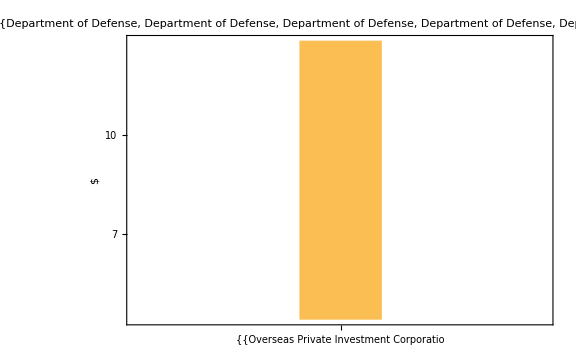

```mathematica
histPlotFin[New814,ToString[textlistMoney814]]
```

### listamountTOTNew[[9]] - category

```mathematica
Style[Keys[listamountTOTNewOhne0[[9]]],FontColor->Red,Large]
```

Environment

```mathematica
listMoney9=Map[Cases[Values[listamountTOTNewOhne0[[9]]],HoldPattern[#->{_String,Quantity[x_/;x>0,"USDollars"]}]]&,aGENCY];
```

```mathematica
listMoney9//InputForm;
```

```mathematica
aGENCY//TableForm
```

Overseas Private Investment Corporation
Department of Defense
Peace Corps
U.S. Agency for International Development
U.S. Department of State
U.S. Department of the Treasury
Inter-American Foundation
Department of Interior
U.S. African Development Foundation
Department of Justice
Department of Labor
U.S. Department of Agriculture

```mathematica
Map[#->Length[listMoney9[[#]]]&,Range[Length[aGENCY]]]
```

{1→0,2→0,3→18,4→39,5→0,6→0,7→3,8→48,9→1,10→0,11→0,12→0}

#### --- --- --- 1

```mathematica
textlistMoney91=Style[listMoney9[[1]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New91=listMoney9[[1]]//Values;
```

```mathematica
Length[New91]
```

0

```mathematica
histPlotFin[New91,ToString[textlistMoney91]]
```

-Graphics-

#### --- --- --- 2

```mathematica
textlistMoney92=Style[listMoney9[[2]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New92=listMoney9[[2]]//Values
```

{}

```mathematica
Length[New92]
```

0

```mathematica
histPlotFin[New92,ToString[textlistMoney92]]
```

-Graphics-

#### --- --- --- 3

```mathematica
textlistMoney93=Style[listMoney9[[3]][[1]]//Keys,FontColor->Red]
```

Peace Corps

```mathematica
New93=listMoney9[[3]]//Values
```

{{Ethiopia,1.288594e6 $},{Ecuador,206 026.00 $},{Mexico,1.193159e6 $},{Peru,1.008298e6 $},{Benin,558 241.00 $},{Cameroon,128 545.00 $},{Guinea,803 427.00 $},{Guyana,48 429.00 $},{Jamaica,1.140213e6 $},{Madagascar,124 148.00 $},{Malawi,1.329982e6 $},{Nicaragua,722 802.00 $},{Panama,1.15605e6 $},{Paraguay,1.085069e6 $},{Philippines,1.116012e6 $},{Senegal,1.077192e6 $},{Togo,897 153.00 $},{Zambia,3.236593e6 $}}

```mathematica
Length[New93]
```

18

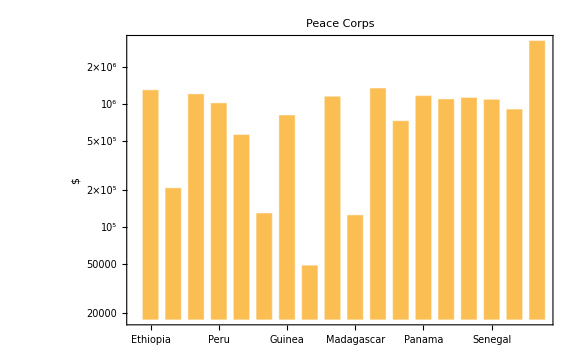

```mathematica
histPlotFin[New93,ToString[textlistMoney93]]
```

#### --- --- --- 4

```mathematica
textlistMoney94=Style[listMoney9[[4]][[1]]//Keys,FontColor->Red]
```

U.S. Agency for International Development

```mathematica
New94=listMoney9[[4]]//Values
```

{{Jordan,1.4955587e6 $},{China,4.1e6 $},{Ethiopia,4.1801496199999996e6 $},{Georgia,2.10223287e6 $},{Kenya,1.745834285e7 $},{Uganda,8.873240370000001e6 $},{Liberia,5.89022731e6 $},{Niger,13 209.81 $},{Guatemala,5.35834637e6 $},{Honduras,7.87383713e6 $},{Mexico,1.1725e7 $},{Peru,1.397225415e7 $},{Afghanistan,4 530.83 $},{Bangladesh,2.505395879e7 $},{Brazil,1.47485216e6 $},{Cambodia,1.002073965e7 $},{Colombia,1.123522366e7 $},{Egypt,1.33394664e6 $},{Ghana,2.e6 $},{Guinea,620 856.84 $},{Haiti,3.0086802199999997e6 $},{India,1.163948732e7 $},{Indonesia,3.5481013269999996e7 $},{Jamaica,2.3969836900000004e6 $},{Kazakhstan,1.96608863e6 $},{Macedonia,2 427.00 $},{Madagascar,585 620.88 $},{Malawi,1.416412794e7 $},{Mali,2.60824598e6 $},{Mozambique,1.152482797e7 $},{Nepal,1.300148743e7 $},{Nicaragua,40 882.81 $},{Philippines,2.246593061e7 $},{Rwanda,729 545.00 $},{Senegal,4.23251255e6 $},{Sudan,1.25e6 $},{Tanzania,8.00564966e6 $},{Vietnam,3.1328197e7 $},{Zambia,1.0643162e7 $}}

```mathematica
Length[New94]
```

39

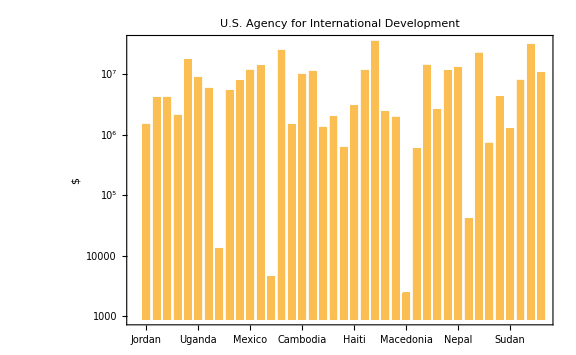

```mathematica
histPlotFin[New94,ToString[textlistMoney94]]
```

#### --- --- --- 5

```mathematica
textlistMoney95=Style[listMoney9[[5]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New95=listMoney9[[5]]//Values
```

{}

```mathematica
Length[New95]
```

0

```mathematica
histPlotFin[New95,ToString[textlistMoney95]]
```

-Graphics-

#### --- --- --- 6

```mathematica
textlistMoney96=Style[listMoney9[[6]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New96=listMoney9[[6]]//Values
```

{}

```mathematica
Length[New96]
```

0

```mathematica
histPlotFin[New96,ToString[textlistMoney96]]
```

-Graphics-

#### --- --- --- 7

```mathematica
textlistMoney97=Style[listMoney9[[7]][[1]]//Keys,FontColor->Red]
```

Inter-American Foundation

```mathematica
New97=listMoney9[[7]]//Values
```

{{Mexico,350 210.00 $},{Colombia,50 000.00 $},{Panama,77 800.00 $}}

```mathematica
Length[New97]
```

3

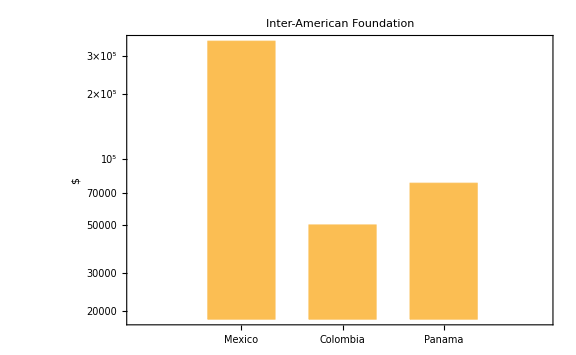

```mathematica
histPlotFin[New97,ToString[textlistMoney97]]
```

#### --- --- --- 8

```mathematica
textlistMoney98=Style[listMoney9[[8]][[1]]//Keys,FontColor->Red]
```

Department of Interior

```mathematica
New98=listMoney9[[8]]//Values
```

{{Argentina,23 945.00 $},{China,298 782.70 $},{Ethiopia,62 243.00 $},{Kenya,899 283.00 $},{Namibia,257 740.00 $},{Russia,279 364.00 $},{Uganda,61 421.00 $},{Liberia,347 198.00 $},{Chile,45 089.00 $},{Portugal,107 600.00 $},{Guatemala,249 390.00 $},{Honduras,92 668.00 $},{Mexico,3.11301388e6 $},{Peru,369 239.00 $},{Bangladesh,42 000.00 $},{Barbados,31 000.00 $},{Belize,314 741.25 $},{Cambodia,511 099.63 $},{Cameroon,4.191638e6 $},{Canada,2.91222859e6 $},{Gabon,2.9981976e7 $},{Ghana,16 400.00 $},{Grenada,68 000.00 $},{India,1.66164575e6 $},{Indonesia,2.081027e6 $},{Kazakhstan,101 774.00 $},{Laos,257 342.00 $},{Madagascar,99 999.00 $},{Malawi,166 055.00 $},{Malaysia,259 527.00 $},{Mali,100 000.00 $},{Mauritania,20 250.00 $},{Mozambique,51 875.00 $},{Nepal,412 039.00 $},{Nicaragua,78 563.00 $},{Nigeria,4.05155954e6 $},{Panama,52 000.00 $},{Paraguay,60 746.00 $},{Rwanda,219 269.00 $},{Senegal,87 656.00 $},{Spain,55 000.00 $},{Sudan,10 000.00 $},{Tanzania,233 392.00 $},{Thailand,518 397.96 $},{Turkey,12 000.00 $},{Vietnam,498 619.00 $},{Zambia,982 770.53 $},{Zimbabwe,220 214.00 $}}

```mathematica
Length[New98]
```

48

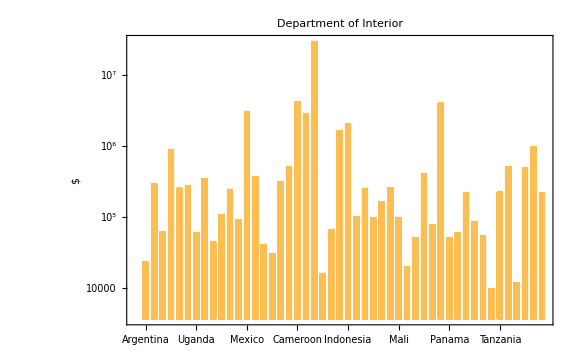

```mathematica
histPlotFin[New98,ToString[textlistMoney98]]
```

#### --- --- --- 9

```mathematica
textlistMoney99=Style[listMoney9[[9]][[1]]//Keys,FontColor->Red]
```

U.S. African Development Foundation

```mathematica
New99=listMoney9[[9]]//Values
```

{{Mauritania,73 775.00 $}}

```mathematica
Length[New99]
```

1

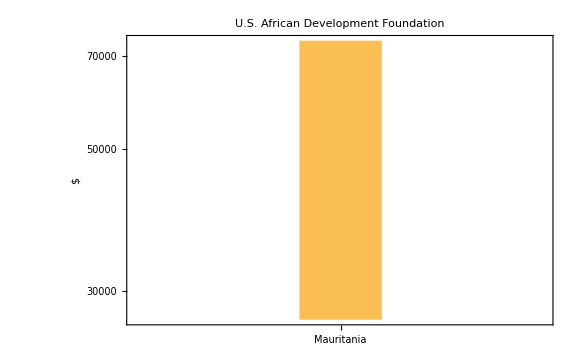

```mathematica
histPlotFin[New99,ToString[textlistMoney99]]
```

#### --- --- --- 10

```mathematica
textlistMoney910=Style[listMoney9[[10]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New910=listMoney9[[10]]//Values
```

{}

```mathematica
Length[New910]
```

0

```mathematica
histPlotFin[New910,ToString[textlistMoney910]]
```

-Graphics-

#### --- --- --- 11

```mathematica
textlistMoney911=Style[listMoney9[[11]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New911=listMoney9[[11]]//Values
```

{}

```mathematica
Length[New911]
```

0

```mathematica
histPlotFin[New911,ToString[textlistMoney911]]
```

-Graphics-

#### --- --- --- 12

```mathematica
textlistMoney912=Style[listMoney9[[12]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 1 of {} does not exist.

Keys::invrl: The argument {}⟦1⟧ is not a valid Association or a list of rules.

Keys[{}⟦1⟧]

```mathematica
New912=listMoney9[[12]]//Values
```

{}

```mathematica
Length[New912]
```

0

```mathematica
histPlotFin[New912,ToString[textlistMoney912]]
```

-Graphics-

#### --- --- --- 13

```mathematica
textlistMoney913=Style[listMoney9[[13]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 13 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior},{U.S. African Development Foundation},{},{},{}}

```mathematica
New913=listMoney9[[13]]//Values
```

Part::partw: Part 13 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Ethiopia,1.288594e6 $},Peace Corps→{Ecuador,206 026.00 $},Peace Corps→{Mexico,1.193159e6 $},Peace Corps→{Peru,1.008298e6 $},Peace Corps→{Benin,558 241.00 $},Peace Corps→{Cameroon,128 545.00 $},Peace Corps→{Guinea,803 427.00 $},Peace Corps→{Guyana,48 429.00 $},Peace Corps→{Jamaica,1.140213e6 $},Peace Corps→{Madagascar,124 148.00 $},Peace Corps→{Malawi,1.329982e6 $},Peace Corps→{Nicaragua,722 802.00 $},Peace Corps→{Panama,1.15605e6 $},Peace Corps→{Paraguay,1.085069e6 $},Peace Corps→{Philippines,1.116012e6 $},Peace Corps→{Senegal,1.077192e6 $},Peace Corps→{Togo,897 153.00 $},Peace Corps→{Zambia,3.236593e6 $}},{U.S. Agency for International Development→{Jordan,1.4955587e6 $},U.S. Agency for International Development→{China,4.1e6 $},U.S. Agency for International Development→{Ethiopia,4.1801496199999996e6 $},U.S. Agency for International Development→{Georgia,2.10223287e6 $},U.S. Agency for International Development→{Kenya,1.745834285e7 $},U.S. Agency for International Development→{Uganda,8.873240370000001e6 $},U.S. Agency for International Development→{Liberia,5.89022731e6 $},U.S. Agency for International Development→{Niger,13 209.81 $},U.S. Agency for International Development→{Guatemala,5.35834637e6 $},U.S. Agency for International Development→{Honduras,7.87383713e6 $},U.S. Agency for International Development→{Mexico,1.1725e7 $},U.S. Agency for International Development→{Peru,1.397225415e7 $},U.S. Agency for International Development→{Afghanistan,4 530.83 $},U.S. Agency for International Development→{Bangladesh,2.505395879e7 $},U.S. Agency for International Development→{Brazil,1.47485216e6 $},U.S. Agency for International Development→{Cambodia,1.002073965e7 $},U.S. Agency for International Development→{Colombia,1.123522366e7 $},U.S. Agency for International Development→{Egypt,1.33394664e6 $},U.S. Agency for International Development→{Ghana,2.e6 $},U.S. Agency for International Development→{Guinea,620 856.84 $},U.S. Agency for International Development→{Haiti,3.0086802199999997e6 $},U.S. Agency for International Development→{India,1.163948732e7 $},U.S. Agency for International Development→{Indonesia,3.5481013269999996e7 $},U.S. Agency for International Development→{Jamaica,2.3969836900000004e6 $},U.S. Agency for International Development→{Kazakhstan,1.96608863e6 $},U.S. Agency for International Development→{Macedonia,2 427.00 $},U.S. Agency for International Development→{Madagascar,585 620.88 $},U.S. Agency for International Development→{Malawi,1.416412794e7 $},U.S. Agency for International Development→{Mali,2.60824598e6 $},U.S. Agency for International Development→{Mozambique,1.152482797e7 $},U.S. Agency for International Development→{Nepal,1.300148743e7 $},U.S. Agency for International Development→{Nicaragua,40 882.81 $},U.S. Agency for International Development→{Philippines,2.246593061e7 $},U.S. Agency for International Development→{Rwanda,729 545.00 $},U.S. Agency for International Development→{Senegal,4.23251255e6 $},U.S. Agency for International Development→{Sudan,1.25e6 $},U.S. Agency for International Development→{Tanzania,8.00564966e6 $},U.S. Agency for International Development→{Vietnam,3.1328197e7 $},U.S. Agency for International Development→{Zambia,1.0643162e7 $}},{},{},{Inter-American Foundation→{Mexico,350 210.00 $},Inter-American Foundation→{Colombia,50 000.00 $},Inter-American Foundation→{Panama,77 800.00 $}},{Department of Interior→{Argentina,23 945.00 $},Department of Interior→{China,298 782.70 $},Department of Interior→{Ethiopia,62 243.00 $},Department of Interior→{Kenya,899 283.00 $},Department of Interior→{Namibia,257 740.00 $},Department of Interior→{Russia,279 364.00 $},Department of Interior→{Uganda,61 421.00 $},Department of Interior→{Liberia,347 198.00 $},Department of Interior→{Chile,45 089.00 $},Department of Interior→{Portugal,107 600.00 $},Department of Interior→{Guatemala,249 390.00 $},Department of Interior→{Honduras,92 668.00 $},Department of Interior→{Mexico,3.11301388e6 $},Department of Interior→{Peru,369 239.00 $},Department of Interior→{Bangladesh,42 000.00 $},Department of Interior→{Barbados,31 000.00 $},Department of Interior→{Belize,314 741.25 $},Department of Interior→{Cambodia,511 099.63 $},Department of Interior→{Cameroon,4.191638e6 $},Department of Interior→{Canada,2.91222859e6 $},Department of Interior→{Gabon,2.9981976e7 $},Department of Interior→{Ghana,16 400.00 $},Department of Interior→{Grenada,68 000.00 $},Department of Interior→{India,1.66164575e6 $},Department of Interior→{Indonesia,2.081027e6 $},Department of Interior→{Kazakhstan,101 774.00 $},Department of Interior→{Laos,257 342.00 $},Department of Interior→{Madagascar,99 999.00 $},Department of Interior→{Malawi,166 055.00 $},Department of Interior→{Malaysia,259 527.00 $},Department of Interior→{Mali,100 000.00 $},Department of Interior→{Mauritania,20 250.00 $},Department of Interior→{Mozambique,51 875.00 $},Department of Interior→{Nepal,412 039.00 $},Department of Interior→{Nicaragua,78 563.00 $},Department of Interior→{Nigeria,4.05155954e6 $},Department of Interior→{Panama,52 000.00 $},Department of Interior→{Paraguay,60 746.00 $},Department of Interior→{Rwanda,219 269.00 $},Department of Interior→{Senegal,87 656.00 $},Department of Interior→{Spain,55 000.00 $},Department of Interior→{Sudan,10 000.00 $},Department of Interior→{Tanzania,233 392.00 $},Department of Interior→{Thailand,518 397.96 $},Department of Interior→{Turkey,12 000.00 $},Department of Interior→{Vietnam,498 619.00 $},Department of Interior→{Zambia,982 770.53 $},Department of Interior→{Zimbabwe,220 214.00 $}},{U.S. African Development Foundation→{Mauritania,73 775.00 $}},{},{},{}}⟦13⟧]

```mathematica
Length[New913]
```

1

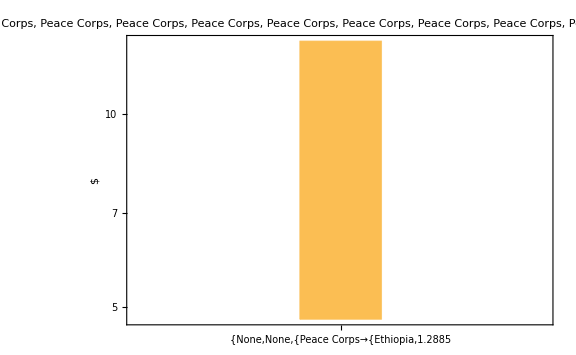

```mathematica
histPlotFin[New913,ToString[textlistMoney913]]
```

#### --- --- --- 14

```mathematica
textlistMoney914=Style[listMoney9[[14]][[1]]//Keys,FontColor->Red]
```

Part::partw: Part 14 of … does not exist.

{{},{},{Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps,Peace Corps},{U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development,U.S. Agency for International Development},{},{},{Inter-American Foundation,Inter-American Foundation,Inter-American Foundation},{Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior,Department of Interior},{U.S. African Development Foundation},{},{},{}}

```mathematica
New914=listMoney9[[14]]//Values
```

Part::partw: Part 14 of … does not exist.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values[{{},{},{Peace Corps→{Ethiopia,1.288594e6 $},Peace Corps→{Ecuador,206 026.00 $},Peace Corps→{Mexico,1.193159e6 $},Peace Corps→{Peru,1.008298e6 $},Peace Corps→{Benin,558 241.00 $},Peace Corps→{Cameroon,128 545.00 $},Peace Corps→{Guinea,803 427.00 $},Peace Corps→{Guyana,48 429.00 $},Peace Corps→{Jamaica,1.140213e6 $},Peace Corps→{Madagascar,124 148.00 $},Peace Corps→{Malawi,1.329982e6 $},Peace Corps→{Nicaragua,722 802.00 $},Peace Corps→{Panama,1.15605e6 $},Peace Corps→{Paraguay,1.085069e6 $},Peace Corps→{Philippines,1.116012e6 $},Peace Corps→{Senegal,1.077192e6 $},Peace Corps→{Togo,897 153.00 $},Peace Corps→{Zambia,3.236593e6 $}},{U.S. Agency for International Development→{Jordan,1.4955587e6 $},U.S. Agency for International Development→{China,4.1e6 $},U.S. Agency for International Development→{Ethiopia,4.1801496199999996e6 $},U.S. Agency for International Development→{Georgia,2.10223287e6 $},U.S. Agency for International Development→{Kenya,1.745834285e7 $},U.S. Agency for International Development→{Uganda,8.873240370000001e6 $},U.S. Agency for International Development→{Liberia,5.89022731e6 $},U.S. Agency for International Development→{Niger,13 209.81 $},U.S. Agency for International Development→{Guatemala,5.35834637e6 $},U.S. Agency for International Development→{Honduras,7.87383713e6 $},U.S. Agency for International Development→{Mexico,1.1725e7 $},U.S. Agency for International Development→{Peru,1.397225415e7 $},U.S. Agency for International Development→{Afghanistan,4 530.83 $},U.S. Agency for International Development→{Bangladesh,2.505395879e7 $},U.S. Agency for International Development→{Brazil,1.47485216e6 $},U.S. Agency for International Development→{Cambodia,1.002073965e7 $},U.S. Agency for International Development→{Colombia,1.123522366e7 $},U.S. Agency for International Development→{Egypt,1.33394664e6 $},U.S. Agency for International Development→{Ghana,2.e6 $},U.S. Agency for International Development→{Guinea,620 856.84 $},U.S. Agency for International Development→{Haiti,3.0086802199999997e6 $},U.S. Agency for International Development→{India,1.163948732e7 $},U.S. Agency for International Development→{Indonesia,3.5481013269999996e7 $},U.S. Agency for International Development→{Jamaica,2.3969836900000004e6 $},U.S. Agency for International Development→{Kazakhstan,1.96608863e6 $},U.S. Agency for International Development→{Macedonia,2 427.00 $},U.S. Agency for International Development→{Madagascar,585 620.88 $},U.S. Agency for International Development→{Malawi,1.416412794e7 $},U.S. Agency for International Development→{Mali,2.60824598e6 $},U.S. Agency for International Development→{Mozambique,1.152482797e7 $},U.S. Agency for International Development→{Nepal,1.300148743e7 $},U.S. Agency for International Development→{Nicaragua,40 882.81 $},U.S. Agency for International Development→{Philippines,2.246593061e7 $},U.S. Agency for International Development→{Rwanda,729 545.00 $},U.S. Agency for International Development→{Senegal,4.23251255e6 $},U.S. Agency for International Development→{Sudan,1.25e6 $},U.S. Agency for International Development→{Tanzania,8.00564966e6 $},U.S. Agency for International Development→{Vietnam,3.1328197e7 $},U.S. Agency for International Development→{Zambia,1.0643162e7 $}},{},{},{Inter-American Foundation→{Mexico,350 210.00 $},Inter-American Foundation→{Colombia,50 000.00 $},Inter-American Foundation→{Panama,77 800.00 $}},{Department of Interior→{Argentina,23 945.00 $},Department of Interior→{China,298 782.70 $},Department of Interior→{Ethiopia,62 243.00 $},Department of Interior→{Kenya,899 283.00 $},Department of Interior→{Namibia,257 740.00 $},Department of Interior→{Russia,279 364.00 $},Department of Interior→{Uganda,61 421.00 $},Department of Interior→{Liberia,347 198.00 $},Department of Interior→{Chile,45 089.00 $},Department of Interior→{Portugal,107 600.00 $},Department of Interior→{Guatemala,249 390.00 $},Department of Interior→{Honduras,92 668.00 $},Department of Interior→{Mexico,3.11301388e6 $},Department of Interior→{Peru,369 239.00 $},Department of Interior→{Bangladesh,42 000.00 $},Department of Interior→{Barbados,31 000.00 $},Department of Interior→{Belize,314 741.25 $},Department of Interior→{Cambodia,511 099.63 $},Department of Interior→{Cameroon,4.191638e6 $},Department of Interior→{Canada,2.91222859e6 $},Department of Interior→{Gabon,2.9981976e7 $},Department of Interior→{Ghana,16 400.00 $},Department of Interior→{Grenada,68 000.00 $},Department of Interior→{India,1.66164575e6 $},Department of Interior→{Indonesia,2.081027e6 $},Department of Interior→{Kazakhstan,101 774.00 $},Department of Interior→{Laos,257 342.00 $},Department of Interior→{Madagascar,99 999.00 $},Department of Interior→{Malawi,166 055.00 $},Department of Interior→{Malaysia,259 527.00 $},Department of Interior→{Mali,100 000.00 $},Department of Interior→{Mauritania,20 250.00 $},Department of Interior→{Mozambique,51 875.00 $},Department of Interior→{Nepal,412 039.00 $},Department of Interior→{Nicaragua,78 563.00 $},Department of Interior→{Nigeria,4.05155954e6 $},Department of Interior→{Panama,52 000.00 $},Department of Interior→{Paraguay,60 746.00 $},Department of Interior→{Rwanda,219 269.00 $},Department of Interior→{Senegal,87 656.00 $},Department of Interior→{Spain,55 000.00 $},Department of Interior→{Sudan,10 000.00 $},Department of Interior→{Tanzania,233 392.00 $},Department of Interior→{Thailand,518 397.96 $},Department of Interior→{Turkey,12 000.00 $},Department of Interior→{Vietnam,498 619.00 $},Department of Interior→{Zambia,982 770.53 $},Department of Interior→{Zimbabwe,220 214.00 $}},{U.S. African Development Foundation→{Mauritania,73 775.00 $}},{},{},{}}⟦14⟧]

```mathematica
Length[New914]
```

1

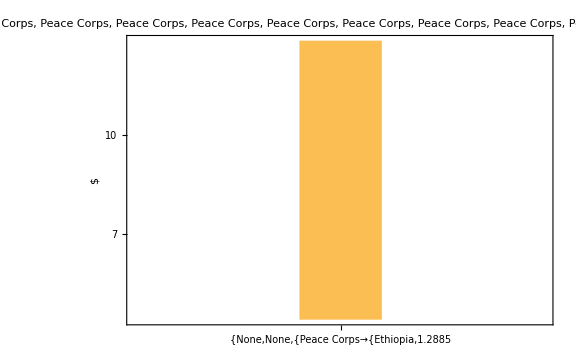

```mathematica
histPlotFin[New914,ToString[textlistMoney914]]
```